# Gametic Selection, Sex-Ratio Bias, and Transitions Between Sex-Determining Systems

## Michael F Scott, Matthew M Osmond, Sarah P Otto

# A. Offspring control (neo-Y, neo-W, or perfect ESD invade XY or ZW)

## Life-cycle

Haploid selection

```mathematica
Subscript[wbarHap, sex_]:=Subscript[wbarHap, sex]=ParallelSum[Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex],{x,{X,Y}},{y,{A,a}},{z,{M,m}}];
Subscript[fHapSel, x_,y_,z_,sex_]:=Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex]/Subscript[wbarHap, sex]
```

Random mating

```mathematica
Subscript[fDip, xM_,yM_,zM_,xP_,yP_,zP_]:=Subscript[fDip, xM,yM,zM,xP,yP,zP]=Subscript[fHapSel, xM,yM,zM,female] Subscript[fHapSel, xP,yP,zP,male]
```

Sex determination

```mathematica
Subscript[fDipSex, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]=Subscript[fDip, xM,yM,zM,xP,yP,zP] Subscript[psex, zM,xP,zP,sex]
```

where a diploid must become male or female

```mathematica
sumsex=Subscript[psex, zM_,xP_,zP_,male]->1-Subscript[psex, zM,xP,zP,female];
```

We assume the invasion of a dominant modifier into an XY system

```mathematica
invXY={
Subscript[psex, M,Y,M,female]->0,(*always male if ESD wildtype and have Y*)
Subscript[psex, M,X,M,female]->1,(*always female ESD wildtype and have X from father*)
Subscript[psex, m,xP_,zP_,female]->k,(*female with probability k if mutation at the ESD*)
Subscript[psex, zM_,xP_,m,female]->k
};
```

Diploid selection

```mathematica
Subscript[wbarDip, sex_]:=Subscript[wbarDip, sex]=ParallelSum[Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}];
Subscript[fDipSel, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex]=Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]/Subscript[wbarDip, sex]
```

Meiosis

```mathematica
Subscript[fHapNext, x_,y_,z_,sex_]:=Subscript[fHapNext, x,y,z,sex]=ParallelSum[Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex] Subscript[pseg, xM,yM,zM,xP,yP,zP,sex,x,y,z],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}]
```

Segregation rules

```mathematica
pseg0={
(*triple homozygote*)
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z1_,sex_,x1_,y1_,z1_]->1
};
pseg1={
(*single heterozygotes*)
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x2_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z1_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z1_,sex_,x1_,y2_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z2_]->1/2
};
pseg2={
(*double heterozygotes*)
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x1_,y1_,z1_]->(1-r)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x2_,y2_,z1_]->(1-r)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x2_,y1_,z1_]->r/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x1_,y2_,z1_]->r/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y1_,z1_]->(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y2_,z2_]->(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y2_,z1_]->R/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y1_,z2_]->R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z1_]->((1-r)(1-R)+r R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z2_]->((1-r)(1-R)+r R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z1_]->(r(1-R)+(1-r)R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z2_]->(r(1-R)+(1-r)R)/2
};
pseg3={
(*triple heterozygote*)
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y1_,z1_]->(1-r)(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y2_,z2_]->(1-r)(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y1_,z1_]->r(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y2_,z2_]->r(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y2_,z1_]->r R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y1_,z2_]->r R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y1_,z2_]->(1-r)R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y2_,z1_]->(1-r)R/2
};
pseg4=Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x_,y_,z_]->0;
```

```mathematica
(*ParallelSum[Subscript[fHapNext, x,y,z,sex]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4,{x,{X,Y}},{y,{A,a}},{z,{M,m}},{sex,{male,female}}]//Factor*)
```

## Resident equilibrium (weak selection)

We begin with no mutations at the modifer locus

```mathematica
subequil={
Subscript[fHap, X,A,M,female]->pXf,
Subscript[fHap, X,a,M,female]->1-pXf,
Subscript[fHap, X,A,M,male]->(1-α)pXm,
Subscript[fHap, X,a,M,male]->(1-α)(1-pXm),
Subscript[fHap, Y,A,M,male]->α pYm,
Subscript[fHap, Y,a,M,male]->α(1-pYm),
Subscript[fHap, x_,y_,m,sex_]->0,
Subscript[fHap, Y,y_,M,female]->0
}/.α->1/2;
```

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following three equations are zero (this takes a minute)

```mathematica
differenceEqs={
Subscript[fHapNext, X,A,M,female]-Subscript[fHap, X,A,M,female],
Subscript[fHapNext, X,A,M,male]-Subscript[fHap, X,A,M,male],
Subscript[fHapNext, Y,A,M,male]-Subscript[fHap, Y,A,M,male]
}/.subequil/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
```

To simplify the analysis we assume weak selection in both haploids and diploids. In addition, we assume selection acts on the VS locus only

```mathematica
weaksel={
Subscript[wHap, A,sex_]->1+Subscript[sHap, sex] ϵ,
Subscript[wHap, a,sex_]->1,
Subscript[wDip, A,A,sex_]->1+ Subscript[sDip, sex] ϵ,
Subscript[wDip, A,a,sex_]->1+Subscript[h, sex] Subscript[sDip, sex] ϵ,
Subscript[wDip, a,A,sex_]->1+Subscript[h, sex] Subscript[sDip, sex] ϵ,
Subscript[wDip, a,a,sex_]->1
};
```

We can write the frequencies as Taylor series

```mathematica
frequenciessub={
pXf->pXf0+pXf1 ϵ,
pXm->pXm0+pXm1 ϵ,
pYm->pYm0+pYm1 ϵ
};
```

Without selection the recursions for the change in the frequencies are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weaksel/.frequenciessub,{ϵ,0,0}]]//Factor
```

{1/2 (-pXf0+pXm0),1/2 (pXf0-pXm0-pXf0 r+pYm0 r),1/2 (pXf0-pYm0) r}

And at equilibrium we have

```mathematica
sol0=Solve[differenceEqs0==0,{pYm0,pXm0}]//Flatten
```

{pYm0→pXf0,pXm0→pXf0}

So, with no selection, the equilibrium frequency of A in each gamete/pollen type is equal (and we call this pA).

Now, looking at only the first order selection terms, the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs1=Collect[Normal[Series[differenceEqs/.weaksel/.frequenciessub/.sol0,{ϵ,0,1}]],ϵ,Factor]/.pXf0->pA//Flatten
```

{1/2 ϵ (-pXf1+pXm1+2 pA^2 sDip_female-2 pA^3 sDip_female+2 pA h_female sDip_female-6 pA^2 h_female sDip_female+4 pA^3 h_female sDip_female+pA sHap_female-pA^2 sHap_female+pA sHap_male-pA^2 sHap_male),1/2 ϵ (pXf1-pXm1-pXf1 r+pYm1 r+pA^2 sDip_male-pA^3 sDip_male+pA h_male sDip_male-3 pA^2 h_male sDip_male+2 pA^3 h_male sDip_male+pA sHap_female-pA^2 sHap_female-pA r sHap_female+pA^2 r sHap_female+pA r sHap_male-pA^2 r sHap_male),1/2 ϵ (pXf1 r-pYm1 r+pA^2 sDip_male-pA^3 sDip_male+pA h_male sDip_male-3 pA^2 h_male sDip_male+2 pA^3 h_male sDip_male+pA r sHap_female-pA^2 r sHap_female+pA sHap_male-pA^2 sHap_male-pA r sHap_male+pA^2 r sHap_male)}

And from these three equations we can solve for the two of the first order differences and the mean frequency of A

```mathematica
realsol=Solve[differenceEqs1==0/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{dpAXmXf,dpAYmXf,pA}]//Factor
```

{{dpAXmXf→0,dpAYmXf→0,pA→0},{dpAXmXf→0,dpAYmXf→0,pA→1},{dpAXmXf→((-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male) (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male) (2 h_female sDip_female sDip_male-2 h_male sDip_female sDip_male-sDip_female sHap_female+2 h_female sDip_female sHap_female+sDip_male sHap_female-2 h_male sDip_male sHap_female-sDip_female sHap_male+2 h_female sDip_female sHap_male+sDip_male sHap_male-2 h_male sDip_male sHap_male))/(-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)^3,dpAYmXf→((-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male) (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male) (h_female sDip_female sDip_male-h_male sDip_female sDip_male-r sDip_female sHap_female+2 r h_female sDip_female sHap_female+sDip_male sHap_female-r sDip_male sHap_female-2 h_male sDip_male sHap_female+2 r h_male sDip_male sHap_female-sDip_female sHap_male+r sDip_female sHap_male+2 h_female sDip_female sHap_male-2 r h_female sDip_female sHap_male+r sDip_male sHap_male-2 r h_male sDip_male sHap_male))/(r (-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)^3),pA→(h_female sDip_female+h_male sDip_male+sHap_female+sHap_male)/(-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)}}

van Doorn and Kirkpatrick 2007 (SOM, page 6) give

```mathematica
vDK07=(Subscript[h, female] Subscript[sDip, female]+Subscript[h, male] Subscript[sDip, male])/((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male]);
```

And when there is no haploid selection our result reduces to theirs

```mathematica
(pA/.realsol[[3]]/.Subscript[sHap, i_]->0)/vDK07//FullSimplify
```

1

## Resident stability (weak selection) [do not need to re-run if unchanged]

Here we use linear stability analysis to examine when the resident equilibrium (i.e., no mutants) derived above is stable.

The Jacobian for the residents is (this takes a couple minutes)

```mathematica
eqs=Join[Table[Subscript[fHapNext, X,y,M,female],{y,{A,a}}],Table[Subscript[fHapNext, x,y,M,male],{x,{X,Y}},{y,{A,a}}]//Flatten]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
matIntFull=Transpose[{
D[eqs,Subscript[fHap, X,A,M,female]],
D[eqs,Subscript[fHap, X,a,M,female]],
D[eqs,Subscript[fHap, X,A,M,male]],
D[eqs,Subscript[fHap, X,a,M,male]],
D[eqs,Subscript[fHap, Y,A,M,male]],
D[eqs,Subscript[fHap, Y,a,M,male]]
}]/.subequil//Factor;
```

From this we can derive the characteristic polynomial

```mathematica
charpolyIntFull=Det[matIntFull-IdentityMatrix[6]*λ];
```

Instead of examining when the non-trivial equilibrium (A not fixed or lost) is stable we will look for when the trivial equilibria (loss or fixation of A) are unstable.

When A is fixed the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt1=charpolyIntFull/.pXm->1/.pXf->1/.pYm->1;
Normal[Series[charpolyInt1/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Factor//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

and λ=1 is the leading eigenvalue.

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt1/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1fix=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male)}

And so the fixation of A is unstable when this expression is positive.

When A is lost the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt0=charpolyIntFull/.pXm->0/.pXf->0/.pYm->0;
Normal[Series[charpolyInt0/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt0/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1loss=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male)}

And so the loss of A is unstable when this expression is positive.

Combining the two results, the protected polymorphism (non-trivial equilibrium) requires that

```mathematica
stabconds={(δλ1/.δλ1fix)<0,(δλ1/.δλ1loss)<0};
```

Note that without haploid selection (i.e., van Doorn and Kirkpatrick 2007), if selection favours the same allele in both sexes there is no stable polymorphism at the A locus

```mathematica
Reduce[(stabconds[[1]]/.Subscript[sHap, i_]->0)&&(stabconds[[2]]/.Subscript[sHap, i_]->0)&&0<Subscript[h, female]<1&&0<Subscript[h, male]<1&&0<Subscript[sDip, male]&&0<Subscript[sDip, female],Reals]
```

False

```mathematica
Reduce[(stabconds[[1]]/.Subscript[sHap, i_]->0)&&(stabconds[[2]]/.Subscript[sHap, i_]->0)&&0<Subscript[h, female]<1&&0<Subscript[h, male]<1&&Subscript[sDip, male]<0&&Subscript[sDip, female]<0,Reals]
```

False

However, with haploid selection we no longer need sexually antagonistic selection for a stable polymorphism at the A locus, e.g., if haploid selection in males opposes selection in diploids we can have a polymorphism when

```mathematica
Reduce[(stabconds[[1]])&&(stabconds[[2]])&&0<Subscript[h, female]<1&&0<Subscript[h, male]<1&&0<Subscript[sDip, male]&&0<Subscript[sDip, female]&&Subscript[sHap, female]==0&&Subscript[sHap, male]<0,Reals]
```

sDip_female>0&&((0<sDip_male<sDip_female&&((0<h_female≤(sDip_female-sDip_male)/(2 sDip_female)&&0<h_male<1&&-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male<sHap_male<-h_female sDip_female-h_male sDip_male)||((sDip_female-sDip_male)/(2 sDip_female)<h_female<(sDip_female+sDip_male)/(2 sDip_female)&&0<h_male<(sDip_female-2 h_female sDip_female+sDip_male)/(2 sDip_male)&&-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male<sHap_male<-h_female sDip_female-h_male sDip_male)))||(sDip_male≥sDip_female&&0<h_female<1&&0<h_male<(sDip_female-2 h_female sDip_female+sDip_male)/(2 sDip_male)&&-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male<sHap_male<-h_female sDip_female-h_male sDip_male))&&sHap_female==0

Assuming equal dominance coefficients in the sexes greatly reduces these conditions and we see that we need stronger haploid selection in males than the sum of selection in diploids and a sufficiently small dominance coefficient

```mathematica
Reduce[(stabconds[[1]]/.Subscript[h, i_]->h)&&(stabconds[[2]]/.Subscript[h, i_]->h)0<h<1&&0<Subscript[sDip, male]&&0<Subscript[sDip, female]&&Subscript[sHap, female]==0&&Subscript[sHap, male]<0,Reals]
```

sDip_female>0&&sDip_male>0&&-sDip_female-sDip_male<sHap_male<0&&0<h<(sDip_female+sDip_male+sHap_male)/(sDip_female+sDip_male)&&sHap_female==0

## Sex chromosome turnover (weak selection) [slow, ~15 minutes]

Here we are interested in the ability of a rare mutation at the modifier locus to invade the non-mutant resident population at equilibrium.

The Jacobian for the mutants is

```mathematica
eqsmut=ParallelTable[Subscript[fHapNext, x,y,m,sex],{sex,{male,female}},{y,{A,a}},{x,{X,Y}}]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4//Flatten;
matExtFull=Transpose[Flatten[ParallelTable[D[eqsmut,Subscript[fHap, x,y,m,sex]],{sex,{male,female}},{y,{A,a}},{x,{X,Y}}],2]]/.subequil//Factor;
```

Giving characteristic polynomial

```mathematica
charpolyExt=Det[matExtFull-IdentityMatrix[8]*λ];
```

Solving for the eigenvalues with no selection gives

```mathematica
Normal[Series[charpolyExt/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→0,λ→1,λ→1-R,λ→(-1+r) (-1+R),λ→1-r-R+2 r R}

On this order the leading eigenvalue is λ=1.

On the first order the eiganvalue is

```mathematica
Normal[Series[charpolyExt/.weaksel/.λ->1+δλ*ϵ/.frequenciessub/.sol0/.pXf0->pA,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ]
```

{{δλ→0}}

And on the 2nd order (this takes a few minutes)

```mathematica
Normal[Series[charpolyExt/.weaksel/.λ->1+δλ2*ϵ^2/.frequenciessub/.sol0/.pXf0->pA/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2];
lambda2diffs=Collect[δλ2/.%,{dpAXmXf,dpAYmXf},Simplify]
```

{-1/2 dpAXmXf k (2 (-1+k) (-pA+(-1+2 pA) h_female) sDip_female-2 (-1+k) (-pA+(-1+2 pA) h_male) sDip_male+k (-sHap_female+sHap_male))+dpAYmXf (k^2 (pA+(1-2 pA) h_female) sDip_female+1/2 (2 (-1+k)^2 (-pA+(-1+2 pA) h_male) sDip_male+k^2 sHap_female-2 sHap_male+4 k sHap_male-k^2 sHap_male))-1/R(-1+pA) pA (k^2 (pA+(1-2 pA) h_female)^2 sDip_female^2+(-1+k)^2 (pA+(1-2 pA) h_male)^2 sDip_male^2-(-1+k) (-pA+(-1+2 pA) h_male) sDip_male ((-R+k (-2+3 R)) sHap_female+(-2+k (2-3 R)+R) sHap_male)-(k sHap_female-(-1+k) sHap_male) ((-R+k (-1+2 R)) sHap_female+(-1+k+R-2 k R) sHap_male)-k (-pA+(-1+2 pA) h_female) sDip_female (2 (-1+k) (-pA+(-1+2 pA) h_male) sDip_male+(2 k+2 R-3 k R) sHap_female+(2-2 k-2 R+3 k R) sHap_male))}

Then we can put in all the differences

```mathematica
tester=Collect[Normal[Series[lambda2diffs/.weaksel/.realsol[[3]],{ϵ,0,2}]],{dpAXmXf,dpAYmXf},Simplify]
```

{-(((-1+h_female) sDip_female+(-1+h_male) sDip_male-sHap_female-sHap_male) (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male) (sDip_male sHap_female-h_male sDip_male (sDip_female+2 sHap_female)-sDip_female sHap_male+h_female sDip_female (sDip_male+2 sHap_male)) (-k^2 R sDip_female sHap_female+2 k^2 r R sDip_female sHap_female-2 r sDip_male sHap_female+8 k r sDip_male sHap_female-8 k^2 r sDip_male sHap_female+2 R sDip_male sHap_female-4 k R sDip_male sHap_female+3 k^2 R sDip_male sHap_female-8 k r R sDip_male sHap_female+10 k^2 r R sDip_male sHap_female+2 r sDip_female sHap_male-8 k r sDip_female sHap_male+8 k^2 r sDip_female sHap_male-2 R sDip_female sHap_male+4 k R sDip_female sHap_male-3 k^2 R sDip_female sHap_male+8 k r R sDip_female sHap_male-10 k^2 r R sDip_female sHap_male+k^2 R sDip_male sHap_male-2 k^2 r R sDip_male sHap_male-2 h_male sDip_male ((r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) sDip_female+((2-4 k+3 k^2) R+2 r (-1-4 k (-1+R)+k^2 (-4+5 R))) sHap_female+k^2 (1-2 r) R sHap_male)+2 h_female sDip_female ((r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) sDip_male+k^2 (1-2 r) R sHap_female+((2-4 k+3 k^2) R+2 r (-1-4 k (-1+R)+k^2 (-4+5 R))) sHap_male)))/(2 r R (sDip_female-2 h_female sDip_female+sDip_male-2 h_male sDip_male)^4)}

Print to avoid re-running all the above:

```mathematica
tester={-(((-1+Subscript[h, female]) Subscript[sDip, female]+(-1+Subscript[h, male]) Subscript[sDip, male]-Subscript[sHap, female]-Subscript[sHap, male]) (Subscript[h, female] Subscript[sDip, female]+Subscript[h, male] Subscript[sDip, male]+Subscript[sHap, female]+Subscript[sHap, male]) (Subscript[sDip, male] Subscript[sHap, female]-Subscript[h, male] Subscript[sDip, male] (Subscript[sDip, female]+2 Subscript[sHap, female])-Subscript[sDip, female] Subscript[sHap, male]+Subscript[h, female] Subscript[sDip, female] (Subscript[sDip, male]+2 Subscript[sHap, male])) (-k^2 R Subscript[sDip, female] Subscript[sHap, female]+2 k^2 r R Subscript[sDip, female] Subscript[sHap, female]-2 r Subscript[sDip, male] Subscript[sHap, female]+8 k r Subscript[sDip, male] Subscript[sHap, female]-8 k^2 r Subscript[sDip, male] Subscript[sHap, female]+2 R Subscript[sDip, male] Subscript[sHap, female]-4 k R Subscript[sDip, male] Subscript[sHap, female]+3 k^2 R Subscript[sDip, male] Subscript[sHap, female]-8 k r R Subscript[sDip, male] Subscript[sHap, female]+10 k^2 r R Subscript[sDip, male] Subscript[sHap, female]+2 r Subscript[sDip, female] Subscript[sHap, male]-8 k r Subscript[sDip, female] Subscript[sHap, male]+8 k^2 r Subscript[sDip, female] Subscript[sHap, male]-2 R Subscript[sDip, female] Subscript[sHap, male]+4 k R Subscript[sDip, female] Subscript[sHap, male]-3 k^2 R Subscript[sDip, female] Subscript[sHap, male]+8 k r R Subscript[sDip, female] Subscript[sHap, male]-10 k^2 r R Subscript[sDip, female] Subscript[sHap, male]+k^2 R Subscript[sDip, male] Subscript[sHap, male]-2 k^2 r R Subscript[sDip, male] Subscript[sHap, male]-2 Subscript[h, male] Subscript[sDip, male] ((r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) Subscript[sDip, female]+((2-4 k+3 k^2) R+2 r (-1-4 k (-1+R)+k^2 (-4+5 R))) Subscript[sHap, female]+k^2 (1-2 r) R Subscript[sHap, male])+2 Subscript[h, female] Subscript[sDip, female] ((r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) Subscript[sDip, male]+k^2 (1-2 r) R Subscript[sHap, female]+((2-4 k+3 k^2) R+2 r (-1-4 k (-1+R)+k^2 (-4+5 R))) Subscript[sHap, male])))/(2 r R ((1-2 Subscript[h, female]) Subscript[sDip, female]+(1-2 Subscript[h, male]) Subscript[sDip, male])^4)};
```

Under some situations (including equal dominance coefficients in the two sexes and no competition among female gametes) this reduces to (using variance in A, VA>0, and the selection term, SA>0):

```mathematica
sterm=(Subscript[sDip, female] Subscript[sHap, male]^2)/(r R (Subscript[sDip, female]+Subscript[sDip, male])^2);
```

1) Dominant masculinizer (neo-Y)

a) invading an XY system

```mathematica
selMasculinizerXY=Collect[tester/(pA(1-pA))*VA/(sterm/SA)/.realsol[[3]]/.Subscript[h, sex_]->h/.k->0//Simplify,{Subscript[sHap, male]},FullSimplify]/.Subscript[sHap, female]->0
```

{(r-R) SA VA sDip_female}

b) invading a ZW system

```mathematica
Collect[tester/(pA(1-pA))*VA/.realsol[[3]]/.Subscript[h, sex_]->h/.k->0//Simplify,{Subscript[sHap, male]},FullSimplify]/.female->temp/.male->female/.temp->male/.Subscript[sHap, female]->0;
selMasculinizerZW=%/(sterm/SA)
```

{(r-R) SA VA sDip_female}

Not that with no haploid selection we have

```mathematica
vDK07=tester/(pA(1-pA))*VA/.realsol[[3]]/.Subscript[sHap, i_]->0/.k->0//Simplify
```

{((r-R) VA (h_female-h_male)^2 sDip_female^2 sDip_male^2)/(r R ((-1+2 h_female) sDip_female+(-1+2 h_male) sDip_male)^2)}

so that positivity requires, in addition to tighter linkage R<r, sexually antagonistic selection (for VA>0) and differences in the dominance coefficients between sexes.

And we see that this reduces to the result of van Doorn and Kirkpatrick 2007 (SOM, top of page 7) with R=1/2

```mathematica
vK1=-VA Subscript[S, A] Subscript[L, A]/.Subscript[S, A]->Subscript[σ, male](Subscript[σ, male]-Subscript[σ, female])/2/.Subscript[L, A]->(1-2r)/r/.R->1/2/.Subscript[σ, i_]->(pA+Subscript[h, i](1-2pA))Subscript[sDip, i]/.realsol[[3]]/.Subscript[sHap, i_]->0//Simplify;
vK1/vDK07/.R->1/2//FullSimplify
```

{1}

and to the result of van Doorn and Kirkpatrick 2007 (SOM, top of page 13) with r=1/2

```mathematica
vK2=VA Subscript[S, A] Subscript[L, A]/.Subscript[S, A]->Subscript[σ, male](Subscript[σ, male]-Subscript[σ, female])/2/.Subscript[L, A]->(1-2R)/R/.r->1/2/.Subscript[σ, i_]->(pA+Subscript[h, i](1-2pA))Subscript[sDip, i]/.realsol[[3]]/.Subscript[sHap, i_]->0//Simplify;
vK2/vDK07/.r->1/2//FullSimplify
```

{1}

2) Dominant feminizer (neo-W)

a) invading an XY system

```mathematica
selFeminizerXY=Collect[tester/(pA(1-pA))*VA/(sterm/SA)/.realsol[[3]]/.Subscript[h, sex_]->h/.k->1//Simplify,{Subscript[sHap, male]},FullSimplify]/.Subscript[sHap, female]->0
```

{-1/2 SA VA ((2 r (-1+R)+R) sDip_female+(-1+2 r) R sDip_male)}

Without haploid selection we have

```mathematica
vK3=tester/(pA(1-pA))*VA/.realsol[[3]]/.Subscript[sHap, i_]->0/.k->1//Simplify
```

{((r-R) VA (h_female-h_male)^2 sDip_female^2 sDip_male^2)/(r R ((-1+2 h_female) sDip_female+(-1+2 h_male) sDip_male)^2)}

which reduces to van Doorn and Kirkpatrick 2010 (Equation 3, top)

```mathematica
vDK10=VA Subscript[α, female](Subscript[α, female]-Subscript[α, male])((1-2R)/(2R)-(1-2r)/(2r))/.Subscript[α, i_]->Subscript[sDip, i](Subscript[h, i]+pA(1-2 Subscript[h, i]))/.realsol[[3]]/.Subscript[sHap, i_]->0//Simplify;
vK3/vDK10//Simplify
```

{1}

with free recombination between the VS and modifier locus this reduces to

```mathematica
Collect[tester/(pA(1-pA))*VA/(sterm/SA)/.realsol[[3]]/.Subscript[h, sex_]->h/.k->1/.R->1/2//Simplify,{Subscript[sHap, male]},FullSimplify]/.Subscript[sHap, female]->0
```

{1/4 (-1+2 r) SA VA (sDip_female-sDip_male)}

b) invading a ZW system

```mathematica
Collect[tester/(pA(1-pA))*VA/.realsol[[3]]/.Subscript[h, sex_]->h/.k->1//Simplify,{Subscript[sHap, female]},FullSimplify]/.female->temp/.male->female/.temp->male/.Subscript[sHap, female]->0;
selFeminizerZW=%/(sterm/SA)
```

{-1/2 SA VA ((2 r (-1+R)+R) sDip_female+(-1+2 r) R sDip_male)}

Not that with no haploid selection we have

```mathematica
tester2/(pA(1-pA))*VA/.(realsol[[3]]/.Subscript[sHap, i_]->0)/.k->1//Simplify
```

{((r-R) VA (h_female-h_male)^2 sDip_female^2 sDip_male^2)/(r R ((-1+2 h_female) sDip_female+(-1+2 h_male) sDip_male)^2)}

which is the same as a neo-Y invading an XY system.

3) Perfect ESD (half females, half males)

a) invading an XY system

```mathematica
selESDsimpXY=Collect[tester/(pA(1-pA))*VA/(sterm/SA)/.realsol[[3]]/.Subscript[h, sex_]->h/.k->1/2//Simplify,{Subscript[sHap, male]},Simplify]/.Subscript[sHap, female]->0
```

{1/8 (-1+2 r) R SA VA (3 sDip_female-sDip_male)}

b) invading a ZW system

```mathematica
Collect[tester/(pA(1-pA))*VA/.realsol[[3]]/.Subscript[h, sex_]->h/.k->1/2//Simplify,{Subscript[sHap, male]},Simplify]/.female->temp/.male->female/.temp->male/.Subscript[sHap, female]->0;
selESDsimpZW=%/(sterm/SA)
```

{-1/8 (-1+2 r) R SA VA (-3 sDip_female+sDip_male)}

This is R times the average of the feminizer and masculinizer with free recombination R=1/2

```mathematica
Factor[R/2*(selFeminizerXY+selMasculinizerXY)];
0==(%-selESDsimpXY/.R->1/2)[[1]]//FullSimplify
```

True

Note that R is involved if the ESD is not perfect (k ≠ 1/2) (when k=1/2 the R cancels out with the 1/R in the SA term)

```mathematica
Collect[tester/(pA(1-pA))*VA/(sterm/SA)/.realsol[[3]]/.Subscript[h, sex_]->h//Simplify,{Subscript[sHap, male]},Simplify]/.Subscript[sHap, female]->0
```

{-1/2 SA VA (((2-4 k+3 k^2) R+2 r (-1-4 k (-1+R)+k^2 (-4+5 R))) sDip_female+k^2 (-1+2 r) R sDip_male)}

## Sex chromosome turnover (selection not assumed to be weak)

### Characteristic polynomial

In this section we do not assume weak selection.

We first define the mean fitness of non-mutant females over the entire life-cycle

```mathematica
femaleMeanFit=
(1-pXf)Subscript[wHap, a,female] (1-pXm) Subscript[wHap, a,male] Subscript[wDip, a,a,female]+
pXf Subscript[wHap, A,female] (1-pXm) Subscript[wHap, a,male] Subscript[wDip, A,a,female]+
(1-pXf)Subscript[wHap, a,female] pXm Subscript[wHap, A,male] Subscript[wDip, a,A,female] +
pXf Subscript[wHap, A,female] pXm Subscript[wHap, A,male] Subscript[wDip, A,A,female];
```

and the mean fitness of non-mutant males over the entire life-cycle

```mathematica
maleMeanFit=
(1-pXf)Subscript[wHap, a,female] (1-pYm) Subscript[wHap, a,male] Subscript[wDip, a,a,male]+
pXf Subscript[wHap, A,female] (1-pYm) Subscript[wHap, a,male] Subscript[wDip, A,a,male]+
(1-pXf)Subscript[wHap, a,female] pYm Subscript[wHap, A,male] Subscript[wDip, a,A,male] +
pXf Subscript[wHap, A,female] pYm Subscript[wHap, A,male] Subscript[wDip, A,A,male];
```

#### neo-Y

When the mutation masculinizes, the characteristic polynomial is

```mathematica
charpolyk0=charpolyExt/.k->0//Factor;
```

The coefficients of our characteristic polynomial are

```mathematica
charpolyα0=Collect[charpolyk0[[4]],λ];
acoef0=Coefficient[charpolyα0,λ^2];
bcoef0=Coefficient[charpolyα0,λ];
ccoef0=charpolyα0-acoef0 λ^2-bcoef0 λ;
```

```mathematica
charpolyα0=Collect[charpolyk0[[3]],λ];
acoef0=Coefficient[charpolyα0,λ^2];
bcoef0=Coefficient[charpolyα0,λ];
ccoef0=charpolyα0-acoef0 λ^2-bcoef0 λ;
```

The a coefficient is

```mathematica
acoef0/(maleMeanFit/meanM)^2//Simplify
```

meanM^2

The b coefficient is

```mathematica
bcoef0/(maleMeanFit/meanM)//Simplify
```

meanM ((-1+pXf) wHap_(a,female) (wHap_(a,male) wDip_(a,a,male)-(-1+R) wHap_(A,male) wDip_(a,A,male))+pXf wHap_(A,female) ((-1+R) wHap_(a,male) wDip_(A,a,male)-wHap_(A,male) wDip_(A,A,male)))

The c coefficient is

```mathematica
ccoef0//Simplify
```

wHap_(a,male) wHap_(A,male) (-(-1+pXf)^2 (-1+R) wHap_(a,female)^2 wDip_(a,a,male) wDip_(a,A,male)-pXf^2 (-1+R) wHap_(A,female)^2 wDip_(A,a,male) wDip_(A,A,male)+(-1+pXf) pXf wHap_(a,female) wHap_(A,female) ((-1+2 R) wDip_(a,A,male) wDip_(A,a,male)-wDip_(a,a,male) wDip_(A,A,male)))

#### neo-W

When the mutation feminizes the characteristic polynomial is

```mathematica
charpolyk1=charpolyExt/.k->1//Factor;
```

and the coefficients are

```mathematica
charpolyα1=Collect[charpolyk1[[4]],λ];
acoef1=Coefficient[charpolyα1,λ^2];
bcoef1=Coefficient[charpolyα1,λ];
ccoef1=charpolyα1-acoef1 λ^2-bcoef1 λ;
```

The a coefficient is

```mathematica
acoef1/(femaleMeanFit/meanF)^2//Simplify
```

4 meanF^2

the b coefficient is

```mathematica
bcoef1/(femaleMeanFit/meanF)/.pXm->2pAveM-pYm//Simplify
```

4 meanF (wHap_(a,female) ((-1+pAveM) wHap_(a,male) wDip_(a,a,female)+pAveM (-1+R) wHap_(A,male) wDip_(a,A,female))-wHap_(A,female) ((-1+pAveM) (-1+R) wHap_(a,male) wDip_(A,a,female)+pAveM wHap_(A,male) wDip_(A,A,female)))

where pAveM is the mean frequency of A in gametes from males,

and the c coefficient is

```mathematica
ccoef1/.pXm->2pAveM-pYm//Simplify
```

-4 wHap_(a,female) wHap_(A,female) ((-1+pAveM)^2 (-1+R) wHap_(a,male)^2 wDip_(a,a,female) wDip_(A,a,female)+pAveM^2 (-1+R) wHap_(A,male)^2 wDip_(a,A,female) wDip_(A,A,female)-(-1+pAveM) pAveM wHap_(a,male) wHap_(A,male) ((-1+2 R) wDip_(a,A,female) wDip_(A,a,female)-wDip_(a,a,female) wDip_(A,A,female)))

#### ESD [unfinished][DELETE?]

When the mutation is a perfect ESD the characteristic polynomial is

```mathematica
charpolyk12=charpolyExt/.k->1/2
```

(-pXf R wHap_(a,male) wHap_(A,female) wDip_(A,a,female) («1»)-(wHap_(a,male) «2» («1»+«1»+«1»))/(«1»)-pXf R («4»)_(«1») «1» wDip_(«1») («1»)+2 («1») (-λ-(wHap_(a,male) (-wHap_(a,female) wDip_(a,a,male)+pXf («4»)_(«1») wDip_(a,«1»«1»male)-«1»+pXf R wHap_(A,female) wDip_(A,a,male)))/(2 («12»+pXf pYm wHap_(A,female) wHap_(A,male) wDip_(A,A,male)))) («1»))/(256 («1»)^4 (-wHap_(a,female) wHap_(a,male) wDip_(a,a,male)+pXf wHap_(a,female) wHap_(a,male) wDip_(a,a,male)+«8»+«1»-pXf pYm wHap_(A,female) wHap_(A,male) wDip_(A,A,male))^4)

and the coefficients are

```mathematica
charpolyα12=Collect[charpolyk12,λ];
```

```mathematica
charpolyα12/.r->0/.R->0/.Subscript[wHap, y_,female]->1
```

λ^8+(λ^7 (-128. wHap_(A,male) («1»)^4 (-wDip_(a,A,male)+pXf wDip_(a,A,male)-pXf wDip_(A,A,male)) (-wHap_(a,male) wDip_(a,a,male)+«1»+«8»+«1»-pXf pYm wHap_(A,male) wDip_(A,A,male))^3+«1»+«1»+«1»+(«1»)/(«1»)))/(256 (-wHap_(a,male) wDip_(a,a,female)+«12»)^4 (-wHap_(a,male) wDip_(a,a,male)+«12»)^4)+(λ^6 («1»))/(256 («1»)^4 («1»)^4)+«3»+(λ^2 («1»))/(256 «1»«1»«1»)+(λ (0.-(0.5 «9»)/((«1»)^2 «1»)+«57»))/(256 («1»)^4 (-(«4»)_(«1») «1»+«12»)^4)+(0.-(0.0625 wHap_(a,male)^2 («4»)_(«1»)^2 «5» («1») («1»)^2)/((«1»)^2 («1»)^2)+«18»)/(256 (-wHap_(a,male) wDip_(a,a,female)+«12»)^4 (-wHap_(a,male) wDip_(a,a,male)+pXf wHap_(a,male) wDip_(a,a,male)+«8»+pXf pYm wHap_(a,male) wDip_(A,a,male)-pXf pYm wHap_(A,male) wDip_(A,A,male))^4)

```mathematica
Solve[0==charpolyα12[[8]]/.R->0/.r->0,λ]
```

$Aborted

```mathematica
charpolyα12=Collect[charpolyk12[[4]],λ];
acoef12=Coefficient[charpolyα12,λ^2];
bcoef12=Coefficient[charpolyα12,λ];
ccoef12=charpolyα12-acoef12 λ^2-bcoef12 λ;
```

### Turnover criteria

#### neo-Y

When there is no recombination at all the eigenvalues are

```mathematica
noreceigens0=(λ/.Solve[0==charpolyk0[[3]]/.r->0/.R->0,λ])*(maleMeanFit/meanM)//Simplify
```

{-(wHap_(A,male) ((-1+pXf) wHap_(a,female) wDip_(a,A,male)-pXf wHap_(A,female) wDip_(A,A,male)))/meanM,-(wHap_(a,male) ((-1+pXf) wHap_(a,female) wDip_(a,a,male)-pXf wHap_(A,female) wDip_(A,a,male)))/meanM}

The growth rates of the haplotypes (where mA and ma haplotypes are lost due to recombination R in double heterozygotes) can be used to reduce the 2a+b<0 condition to

```mathematica
gAsub=Solve[gA==noreceigens0[[1]]-1/.Subscript[wDip, a,A,male]->(1-R) Subscript[wDip, a,A,male],Subscript[wDip, A,A,male]]//Simplify//Flatten;
gasub=Solve[ga==noreceigens0[[2]]-1/.Subscript[wDip, A,a,male]->(1-R) Subscript[wDip, A,a,male],Subscript[wDip, a,a,male]]//Simplify//Flatten;
(2acoef0/(maleMeanFit/meanM)^2+bcoef0/(maleMeanFit/meanM))<0/.gasub/.gAsub//Simplify;
Simplify[%/.Subscript[wDip, a,A,male]->Subscript[wDip, A,a,male],{meanM>0}];
%/.gA->2gmean-ga//Simplify
```

gmean>0

And when we ignore the break up due to recombination then the growth rates are

```mathematica
gAssub=Solve[gAs==noreceigens0[[1]]-1,Subscript[wDip, A,A,male]]//Simplify//Flatten;
gassub=Solve[gas==noreceigens0[[2]]-1,Subscript[wDip, a,a,male]]//Simplify//Flatten;
```

and our final condition a+b+c<0 is

```mathematica
Collect[(acoef0/(maleMeanFit/meanM)^2+bcoef0/(maleMeanFit/meanM)+ccoef0)<0/.gassub/.gAssub/.Subscript[wDip, a,A,male]->Subscript[wDip, A,a,male]//Simplify,{meanM,Subscript[wDip, A,a,male]},Simplify]
```

gas gAs meanM^2+meanM (-gAs pXf R wHap_(a,male) wHap_(A,female)+gas (-1+pXf) R wHap_(a,female) wHap_(A,male)) wDip_(A,a,male)<0

which can be rearranged into

```mathematica
R(gAs pXf R Subscript[wHap, a,male] Subscript[wHap, A,female]+gas (1-pXf) R Subscript[wHap, a,female] Subscript[wHap, A,male]) Subscript[wDip, A,a,male]>gas gAs meanM
```

If both ga>0 and gA>0 then 2a+b>0 and the neo-Y invades. If both gas<0 and gAs<0 then a+b+c<0 is never true and the neo-Y will not invade. So the interesting part is when one gs is positive and one negative. If we assume, without loss of generality, that gAs>0 and gas<0, the product gas gAs is negative. Dividing through and flipping the inequality:

```mathematica
R( (pXf Subscript[wHap, a,male] Subscript[wHap, A,female])/gas+((1-pXf) Subscript[wHap, a,female] Subscript[wHap, A,male])/gAs) Subscript[wDip, A,a,male]<meanM
```

#### neo-W

When there is no recombination between the VS and modifier locus we have a perfect square and eigenvalues

```mathematica
noreceigens1=(λ/.Solve[0==charpolyk1[[4]]/.R->0,λ])*(femaleMeanFit/meanF)/.pXm->2pAveM-pYm//Simplify
```

{-(wHap_(a,female) ((-1+pAveM) wHap_(a,male) wDip_(a,a,female)-pAveM wHap_(A,male) wDip_(a,A,female)))/meanF,-(wHap_(A,female) ((-1+pAveM) wHap_(a,male) wDip_(A,a,female)-pAveM wHap_(A,male) wDip_(A,A,female)))/meanF}

The first describes the invasion fitness of w-a haplotypes and the second the growth rate of w-A haplotypes (these haplotypes are never broken up because R=0, and they always appear in the homorphic sex and so r has no affect).

The growth rate of the haplotypes without recombination can be used to simplify our expressions. To make use of them we will first solve for unique elements in each and then use these substitutions later.

```mathematica
gasubR0=Solve[noreceigens1[[1]]-1==gaR0,Subscript[wDip, a,a,female]]//Flatten;
gAsubR0=Solve[noreceigens1[[2]]-1==gAR0,Subscript[wDip, A,A,female]]//Simplify//Flatten;
```

Our 2a+b<0 condition is then

```mathematica
Simplify[(2acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF))<0/.pXm->-pYm+2pAveM/.gAsubR0/.gasubR0,meanF>0]
```

(gaR0+gAR0) meanF+(-1+pAveM) R wHap_(a,male) wHap_(A,female) wDip_(A,a,female)>pAveM R wHap_(a,female) wHap_(A,male) wDip_(a,A,female)

and when the fitness of diploids does not depend from which parent the A and a alleles come from, and there is no competition among eggs, we have

```mathematica
%/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]/.Subscript[wHap, y_,female]->1//FullSimplify
```

(gaR0+gAR0) meanF+R ((-1+pAveM) wHap_(a,male)-pAveM wHap_(A,male)) wDip_(A,a,female)>0

n.b., if you instead look at the growth rates of the haplotypes with recombination (where double heterozygotes are sometimes lost through recombination; we don’t have many triple heterozygotes in females when the neo-W is rare because all are XX) this condition becomes

```mathematica
gasub=Solve[ga==noreceigens1[[1]]-1/. Subscript[wDip, a,A,female]->(1-R) Subscript[wDip, a,A,female],Subscript[wDip, a,a,female]]//Simplify//Flatten;
gAsub=Solve[gA==noreceigens1[[2]]-1/. Subscript[wDip, A,a,female]->(1-R) Subscript[wDip, A,a,female],Subscript[wDip, A,A,female]]//Simplify//Flatten;
(2acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF))/meanF^2<0/.pXm->-pYm+2pAveM/.gAsub/.gasub//Simplify;
%/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]/.ga->-gA+2gmean//FullSimplify
```

gmean>0

which only requires that the mean haplotype growth rate is greater than 0.

Using the no recombination growth rate definitions, our final condition is

```mathematica
Collect[(acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF)+ccoef1)/meanF<0/.pXm->-pYm+2pAveM/.gasubR0/.gAsubR0/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]//Simplify,{meanF,R,Subscript[wDip, A,a,female]}]
```

gaR0 gAR0 meanF+R (gaR0 (-1+pAveM) wHap_(a,male) wHap_(A,female)-gAR0 pAveM wHap_(a,female) wHap_(A,male)) wDip_(A,a,female)<0

We can rearrange this into

```mathematica
R ((1-pAveM) gaR0 Subscript[wHap, a,male] Subscript[wHap, A,female]+pAveM gAR0 Subscript[wHap, a,female] Subscript[wHap, A,male]) Subscript[wDip, A,a,female]>meanF gaR0 gAR0;
```

If both gA>0 and gA>0 then 2a+b>0 and the modifier invades. If both gAR0<0 and gaR0<0 then a+b+c<0 is never true and the modifier will not invade. So the interesting part is when one gR0 is positive and one negative. If we assume, without loss of generality, that gAR0>0 and gaR0<0, the product gAR0 gaR0 is negative. Dividing through and flipping the inequality:

```mathematica
R (((1-pAveM)  Subscript[wHap, a,male] Subscript[wHap, A,female])/gAR0+(pAveM Subscript[wHap, a,female] Subscript[wHap, A,male])/gaR0) Subscript[wDip, A,a,female]< meanF;
```

### Comparison to Kozielska et al 2010

Kozielska et al 2010 found that feminizing mutations invade, apparently to equalize the sex ratio.

We also see the same result as Kozielska et al 2010 (Heredity 104:100), where, without diploid selection, the W invades if the Y is ‘driving’ and the resident equilibrium is A fixed on the X and lost on the Y

```mathematica
tryKozi={pXf->1,pXm->1,pYm->0};
Solve[Normal[Series[(charpolyα1/.weaksel/.tryKozi/.λ->1+δλ*ϵ),{ϵ,0,1}]]==0,δλ]/.Subscript[sDip, female]->0/.Subscript[sHap, female]->0
```

{{δλ→sHap_male/2}}

```mathematica
tryKozi={pXf->1,pXm->1,pYm->0};
Solve[Normal[Series[(charpolyα1/.weaksel/.tryKozi/.λ->1+δλ*ϵ),{ϵ,0,1}]]==0,δλ]/.Subscript[sDip, female]->0/.Subscript[sHap, male]->0
```

{{δλ→-sHap_female/2}}

But this is not a stable resident equilibrium. It can only happen if r=0 and A mutates to a on the Y (or a mutates to A on the X) and no more mutations occur.

We can also do this without assuming weak selection

```mathematica
Simplify[Solve[0==charpolyα1/.tryKozi,λ]/.Subscript[wDip, yM_,yP_,female]->1/.Subscript[wHap, y_,female]->1,{R>0,Subscript[wHap, a,male]>0,Subscript[wHap, A,male]>0}]
```

{{λ→1/2 (1+(wHap_(a,male))/(wHap_(A,male)))},{λ→-((-1+R) (wHap_(a,male)+wHap_(A,male)))/(2 wHap_(A,male))}}

Again, invasion occurs if the Y is ‘driving’ (wHap_(a,male)>wHap_(A,male)).

## Plots

### Recursions

#### First find the equilibrium frequency (equil and sieve functions)

Transform our variables to simpler, shorter ones

```mathematica
varsub={Subscript[wDip, A,A,female]->FAA,Subscript[wDip, A,a,female]->FAa,Subscript[wDip, a,A,female]->FAa,Subscript[wDip, a,a,female]->Faa,Subscript[wDip, A,A,male]->MAA,Subscript[wDip, A,a,male]->MAa,Subscript[wDip, a,A,male]->MAa,Subscript[wDip, a,a,male]->Maa,Subscript[wHap, A,male]->wA,Subscript[wHap, a,male]->wa,Subscript[wHap, y_,female]->1};
```

These are the frequency changes we are interested in in the resident population (pXf, pXm, pYm)

```mathematica
differenceEqs/.varsub//Simplify
```

{(-2 Faa (-1+pXf) pXf (-1+pXm) wa-2 FAA (-1+pXf) pXf pXm wA+FAa (-1+2 pXf) (-pXm wA+pXf ((-1+pXm) wa+pXm wA)))/(2 (Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXm wA+pXf (wa-pXm wa-pXm wA)))),(Maa pXm (-1+pXf+pYm-pXf pYm) wa-MAA pXf (-1+pXm) pYm wA+MAa (pYm (-pXm+r) wA+pXf ((-1+pYm) (-1+pXm+r) wa+pYm (pXm-r) wA)))/(2 (Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA)))),(Maa pYm (-1+pXf+pYm-pXf pYm) wa-MAA pXf (-1+pYm) pYm wA+MAa (-pYm (-1+pYm+r) wA+pXf (r wa+pYm^2 (wa+wA)-pYm (wa+r wa+wA-r wA))))/(2 (Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA))))}

Make a function that numerically solves for the equilibrium frequencies

```mathematica
Clear[equil]
equil[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,α_]:={pXf,pXm,pYm}/.NSolve[{(-2 Faa (-1+pXf) pXf (-1+pXm) wa-2 FAA (-1+pXf) pXf pXm wA+FAa (-1+2 pXf) (-pXm wA+pXf ((-1+pXm) wa+pXm wA)))/(2 (Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXm wA+pXf (wa-pXm wa-pXm wA)))),(Maa pXm (-1+pXf+pYm-pXf pYm) wa-MAA pXf (-1+pXm) pYm wA+MAa (pYm (-pXm+r) wA+pXf ((-1+pYm) (-1+pXm+r) wa+pYm (pXm-r) wA)))/(2 (Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA)))),(Maa pYm (-1+pXf+pYm-pXf pYm) wa-MAA pXf (-1+pYm) pYm wA+MAa (-pYm (-1+pYm+r) wA+pXf (r wa+pYm^2 (wa+wA)-pYm (wa+r wa+wA-r wA))))/(2 (Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA))))}=={0,0,0},{pXf,pXm,pYm}]
```

For example,

```mathematica
equil[1,1.1,1.15,1,1.1,1.15,1,0.9,1/2,1/2]
```

{{1.,1.,1.},{0.181818,0.181818,0.181818},{0.,0.,0.}}

Now remove the non-polymorphic equiibria

```mathematica
cutoff=10^(-10);

Clear[sieve]
sieve[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,α_]:=Block[{},For[i=1;write={},i≤(max=Length[eq=(equil[FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,α])]),i++,If[Length[test=Cases[eq[[i]],x_/;((cutoff≤Re[x]≤1-cutoff)&&Abs[Im[x]]<cutoff)]]==3,write=Append[write,eq[[i]]]]];
Sort[write]]
```

For example,

```mathematica
Flatten[sieve[1,1.1,1.15,1,1.1,1.15,1,0.9,1/2,1/2]]
```

{0.181818,0.181818,0.181818}

#### Next Xf genotypes

Lets again substitute for some smaller, simpler variables

```mathematica
freqsub={
Subscript[fHap, X,A,M,female]->XAf,Subscript[fHap, X,a,M,female]->Xaf,Subscript[fHap, X,A,m,female]->XAwf,Subscript[fHap, X,a,m,female]->Xawf,
Subscript[fHap, Y,A,M,female]->YAf,Subscript[fHap, Y,a,M,female]->Yaf,Subscript[fHap, Y,A,m,female]->YAwf,Subscript[fHap, Y,a,m,female]->Yawf,
Subscript[fHap, X,A,M,male]->XAm,Subscript[fHap, X,a,M,male]->Xam,Subscript[fHap, X,A,m,male]->XAwm,Subscript[fHap, X,a,m,male]->Xawm,
Subscript[fHap, Y,A,M,male]->YAm,Subscript[fHap, Y,a,M,male]->Yam,Subscript[fHap, Y,A,m,male]->YAwm,Subscript[fHap, Y,a,m,male]->Yawm
};
```

Then the recursions we are interested in here (X haplotypes in females) are

```mathematica
Simplify[{
Subscript[fHapNext, X,A,M,female]-Subscript[fHap, X,A,M,female],
Subscript[fHapNext, X,a,M,female]-Subscript[fHap, X,a,M,female],
Subscript[fHapNext, X,A,m,female]-Subscript[fHap, X,A,m,female],
Subscript[fHapNext, X,a,m,female]-Subscript[fHap, X,a,m,female]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub]
```

{-(2 Faa wa XAf (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAA wA (-XAm YAf-k (-(-R+r (-1+2 R)) (XAwm YAf+XAwf YAm)+XAm (XAwf+(1-r-R+2 r R) YAwf))+2 XAf^2 (XAm+k (XAwm+YAwm))+XAf (2 XAm (-1+YAf+k (XAwf+YAwf))+k (2 YAm YAwf+XAwm (-1+2 XAwf+2 YAf+2 YAwf)-YAwm+r YAwm+R YAwm-2 r R YAwm+2 YAf YAwm+2 YAwf YAwm+2 XAwf (YAm+YAwm))))+FAa (wa (-r Xam YAf-k (r Xawm YAf+R (XAwf Yam-r (Xawm YAf+XAwf Yam)+Xam (XAwf+r YAwf)))+2 XAf^2 (Xam+k (Xawm+Yawm))+XAf (Xam (-1+2 YAf+2 k (XAwf+YAwf))+k (2 Yam YAwf+Xawm (-1+R+2 XAwf+2 YAf+2 YAwf)-Yawm+r Yawm+R Yawm-r R Yawm+2 YAf Yawm+2 YAwf Yawm+2 XAwf (Yam+Yawm))))+wA ((-1+r+2 XAf) XAm Yaf+k (-R XAwm Yaf+r R XAwm Yaf-r Xawf YAm+r R Xawf YAm+XAm ((-1+R+2 XAf) Xawf+(-1+r+R-r R+2 XAf) Yawf)+2 XAf (YAm Yawf+XAwm (Yaf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm)))+Xaf ((-1+2 XAf) XAm-k (-2 XAf (XAwm+YAwm)+R (XAwm+r YAwm))))))/(2 (Faa wa (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAA wA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))+FAa (wa (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+wA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm)))))),-(Faa wa (-Xam Yaf-k (-(-R+r (-1+2 R)) (Xawm Yaf+Xawf Yam)+Xam (Xawf+(1-r-R+2 r R) Yawf))+2 Xaf^2 (Xam+k (Xawm+Yawm))+Xaf (2 Xam (-1+Yaf+k (Xawf+Yawf))+k (2 Yam Yawf+Xawm (-1+2 Xawf+2 Yaf+2 Yawf)-Yawm+r Yawm+R Yawm-2 r R Yawm+2 Yaf Yawm+2 Yawf Yawm+2 Xawf (Yam+Yawm))))+2 FAA wA Xaf (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))+FAa (wa ((-1+r+2 Xaf) Xam YAf+k (-R Xawm YAf+r R Xawm YAf-r XAwf Yam+r R XAwf Yam+Xam ((-1+R+2 Xaf) XAwf+(-1+r+R-r R+2 Xaf) YAwf)+2 Xaf (Yam YAwf+Xawm (YAf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+XAf ((-1+2 Xaf) Xam-k (-2 Xaf (Xawm+Yawm)+R (Xawm+r Yawm))))+wA (-r XAm Yaf-k (r XAwm Yaf+R (Xawf YAm-r (XAwm Yaf+Xawf YAm)+XAm (Xawf+r Yawf)))+2 Xaf^2 (XAm+k (XAwm+YAwm))+Xaf (XAm (-1+2 Yaf+2 k (Xawf+Yawf))+k (2 YAm Yawf+XAwm (-1+R+2 Xawf+2 Yaf+2 Yawf)-YAwm+r YAwm+R YAwm-r R YAwm+2 Yaf YAwm+2 Yawf YAwm+2 Xawf (YAm+YAwm))))))/(2 (Faa wa (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAA wA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))+FAa (wa (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+wA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm)))))),(-2 Faa wa XAwf (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAA wA (-2 XAm XAwf (XAf+YAf)+k (2 XAwf XAwm-2 XAwf^2 XAwm+XAwm YAf-r XAwm YAf-R XAwm YAf+2 r R XAwm YAf-2 XAwf XAwm YAf+XAwf YAm-r XAwf YAm-R XAwf YAm+2 r R XAwf YAm-2 XAwf^2 YAm+XAwm YAwf-2 XAwf XAwm YAwf-2 XAwf YAm YAwf+XAm (XAwf-2 XAwf^2+(r+R-2 r R) YAwf-2 XAwf YAwf)+XAwf YAwm-2 XAwf^2 YAwm-2 XAwf YAf YAwm-2 XAwf YAwf YAwm+XAf (XAwm-2 XAwf XAwm+(r+R-2 r R-2 XAwf) YAwm)))+FAa (-2 XAwf (wA XAm (Xaf+Yaf)+wa Xam (XAf+YAf))+k (-wa (-r Xawm YAwf+Xam (2 XAwf^2-r YAwf+XAwf (-1+2 YAwf))+2 XAwf^2 (Xawm+Yam+Yawm)+XAwf (Yam (-1+r+2 YAwf)+Xawm (-1+2 XAf+2 YAf+2 YAwf)+(-1+r+2 XAf+2 YAf+2 YAwf) Yawm))-wA (-Xawf XAwm+2 Xawf XAwf XAwm-XAwm Yaf+r XAwm Yaf+2 XAwf XAwm Yaf+2 Xawf XAwf YAm-XAwm Yawf+r XAwm Yawf+2 XAwf XAwm Yawf+2 XAwf YAm Yawf+2 XAm XAwf (Xawf+Yawf)-r Xawf YAwm+2 Xawf XAwf YAwm+2 XAwf Yaf YAwm+2 XAwf Yawf YAwm+Xaf (-XAwm+2 XAwf XAwm-r YAwm+2 XAwf YAwm))+R (wa (r Xawm YAf-XAwf Yam+r XAwf Yam-Xam (XAwf+r YAwf)+XAf (Xawm+Yawm-r Yawm))+wA (-XAwm Yaf+r XAwm Yaf+r Xawf YAm+XAm (Xawf+Yawf-r Yawf)-Xaf (XAwm+r YAwm))))))/(2 (Faa wa (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAA wA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))+FAa (wa (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+wA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm)))))),(Faa wa (-2 Xam Xawf (Xaf+Yaf)+k (2 Xawf Xawm-2 Xawf^2 Xawm+Xawm Yaf-r Xawm Yaf-R Xawm Yaf+2 r R Xawm Yaf-2 Xawf Xawm Yaf+Xawf Yam-r Xawf Yam-R Xawf Yam+2 r R Xawf Yam-2 Xawf^2 Yam+Xawm Yawf-2 Xawf Xawm Yawf-2 Xawf Yam Yawf+Xam (Xawf-2 Xawf^2+(r+R-2 r R) Yawf-2 Xawf Yawf)+Xawf Yawm-2 Xawf^2 Yawm-2 Xawf Yaf Yawm-2 Xawf Yawf Yawm+Xaf (Xawm-2 Xawf Xawm+(r+R-2 r R-2 Xawf) Yawm)))-2 FAA wA Xawf (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))-FAa (wa (2 Xam Xawf YAf+k (-XAwf Xawm+2 Xawf XAwf Xawm-Xawm YAf+r Xawm YAf+2 Xawf Xawm YAf+2 Xawf XAwf Yam-Xawm YAwf+r Xawm YAwf+2 Xawf Xawm YAwf+2 Xawf Yam YAwf+2 Xam Xawf (XAwf+YAwf)-R ((-1+r) Xawm YAf+r XAwf Yam+Xam (XAwf+YAwf-r YAwf))-r XAwf Yawm+2 Xawf XAwf Yawm+2 Xawf YAf Yawm+2 Xawf YAwf Yawm)+XAf (2 Xam Xawf+k ((-1+R+2 Xawf) Xawm+(r (-1+R)+2 Xawf) Yawm)))+wA (2 XAm Xawf (Xaf+Yaf)+k (-Xawf XAwm+2 Xaf Xawf XAwm+2 Xawf^2 XAwm+2 Xawf XAwm Yaf-Xawf YAm+r Xawf YAm+2 Xawf^2 YAm-r XAwm Yawf+2 Xawf XAwm Yawf+2 Xawf YAm Yawf+XAm (2 Xawf^2+r (-1+R) Yawf+Xawf (-1+R+2 Yawf))-Xawf YAwm+r Xawf YAwm+2 Xaf Xawf YAwm+2 Xawf^2 YAwm+2 Xawf Yaf YAwm+2 Xawf Yawf YAwm-R (r XAwm Yaf-Xawf YAm+r Xawf YAm+Xaf (XAwm+YAwm-r YAwm))))))/(2 (Faa wa (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAA wA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))+FAa (wa (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+wA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))))}

```mathematica
Clear[nextXAf,nextXaf,nextXAwf,nextXawf]
```

Make functions to get frequencies of each Xf genotype in generation t. This depends on what the frequencies of all other genotypes were at time t (inside the blocks).

```mathematica
nextXAf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
(* These are the frequencies of all genotypes at the previous timestep *)
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAf=-(2 Faa wa XAf (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAA wA (-XAm YAf-k (-(-R+r (-1+2 R)) (XAwm YAf+XAwf YAm)+XAm (XAwf+(1-r-R+2 r R) YAwf))+2 XAf^2 (XAm+k (XAwm+YAwm))+XAf (2 XAm (-1+YAf+k (XAwf+YAwf))+k (2 YAm YAwf+XAwm (-1+2 XAwf+2 YAf+2 YAwf)-YAwm+r YAwm+R YAwm-2 r R YAwm+2 YAf YAwm+2 YAwf YAwm+2 XAwf (YAm+YAwm))))+FAa (wa (-r Xam YAf-k (r Xawm YAf+R (XAwf Yam-r (Xawm YAf+XAwf Yam)+Xam (XAwf+r YAwf)))+2 XAf^2 (Xam+k (Xawm+Yawm))+XAf (Xam (-1+2 YAf+2 k (XAwf+YAwf))+k (2 Yam YAwf+Xawm (-1+R+2 XAwf+2 YAf+2 YAwf)-Yawm+r Yawm+R Yawm-r R Yawm+2 YAf Yawm+2 YAwf Yawm+2 XAwf (Yam+Yawm))))+wA ((-1+r+2 XAf) XAm Yaf+k (-R XAwm Yaf+r R XAwm Yaf-r Xawf YAm+r R Xawf YAm+XAm ((-1+R+2 XAf) Xawf+(-1+r+R-r R+2 XAf) Yawf)+2 XAf (YAm Yawf+XAwm (Yaf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm)))+Xaf ((-1+2 XAf) XAm-k (-2 XAf (XAwm+YAwm)+R (XAwm+r YAwm))))))/(2 (Faa wa (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAA wA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))+FAa (wa (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+wA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))))},
If[newXAf<0,0,If[newXAf>1,1,newXAf]]]
]

nextXaf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXaf=-(Faa wa (-Xam Yaf-k (-(-R+r (-1+2 R)) (Xawm Yaf+Xawf Yam)+Xam (Xawf+(1-r-R+2 r R) Yawf))+2 Xaf^2 (Xam+k (Xawm+Yawm))+Xaf (2 Xam (-1+Yaf+k (Xawf+Yawf))+k (2 Yam Yawf+Xawm (-1+2 Xawf+2 Yaf+2 Yawf)-Yawm+r Yawm+R Yawm-2 r R Yawm+2 Yaf Yawm+2 Yawf Yawm+2 Xawf (Yam+Yawm))))+2 FAA wA Xaf (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))+FAa (wa ((-1+r+2 Xaf) Xam YAf+k (-R Xawm YAf+r R Xawm YAf-r XAwf Yam+r R XAwf Yam+Xam ((-1+R+2 Xaf) XAwf+(-1+r+R-r R+2 Xaf) YAwf)+2 Xaf (Yam YAwf+Xawm (YAf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+XAf ((-1+2 Xaf) Xam-k (-2 Xaf (Xawm+Yawm)+R (Xawm+r Yawm))))+wA (-r XAm Yaf-k (r XAwm Yaf+R (Xawf YAm-r (XAwm Yaf+Xawf YAm)+XAm (Xawf+r Yawf)))+2 Xaf^2 (XAm+k (XAwm+YAwm))+Xaf (XAm (-1+2 Yaf+2 k (Xawf+Yawf))+k (2 YAm Yawf+XAwm (-1+R+2 Xawf+2 Yaf+2 Yawf)-YAwm+r YAwm+R YAwm-r R YAwm+2 Yaf YAwm+2 Yawf YAwm+2 Xawf (YAm+YAwm))))))/(2 (Faa wa (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAA wA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))+FAa (wa (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+wA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))))},
If[newXaf<0,0,If[newXaf>1,1,newXaf]]]
]

nextXAwf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAwf=(-2 Faa wa XAwf (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAA wA (-2 XAm XAwf (XAf+YAf)+k (2 XAwf XAwm-2 XAwf^2 XAwm+XAwm YAf-r XAwm YAf-R XAwm YAf+2 r R XAwm YAf-2 XAwf XAwm YAf+XAwf YAm-r XAwf YAm-R XAwf YAm+2 r R XAwf YAm-2 XAwf^2 YAm+XAwm YAwf-2 XAwf XAwm YAwf-2 XAwf YAm YAwf+XAm (XAwf-2 XAwf^2+(r+R-2 r R) YAwf-2 XAwf YAwf)+XAwf YAwm-2 XAwf^2 YAwm-2 XAwf YAf YAwm-2 XAwf YAwf YAwm+XAf (XAwm-2 XAwf XAwm+(r+R-2 r R-2 XAwf) YAwm)))+FAa (-2 XAwf (wA XAm (Xaf+Yaf)+wa Xam (XAf+YAf))+k (-wa (-r Xawm YAwf+Xam (2 XAwf^2-r YAwf+XAwf (-1+2 YAwf))+2 XAwf^2 (Xawm+Yam+Yawm)+XAwf (Yam (-1+r+2 YAwf)+Xawm (-1+2 XAf+2 YAf+2 YAwf)+(-1+r+2 XAf+2 YAf+2 YAwf) Yawm))-wA (-Xawf XAwm+2 Xawf XAwf XAwm-XAwm Yaf+r XAwm Yaf+2 XAwf XAwm Yaf+2 Xawf XAwf YAm-XAwm Yawf+r XAwm Yawf+2 XAwf XAwm Yawf+2 XAwf YAm Yawf+2 XAm XAwf (Xawf+Yawf)-r Xawf YAwm+2 Xawf XAwf YAwm+2 XAwf Yaf YAwm+2 XAwf Yawf YAwm+Xaf (-XAwm+2 XAwf XAwm-r YAwm+2 XAwf YAwm))+R (wa (r Xawm YAf-XAwf Yam+r XAwf Yam-Xam (XAwf+r YAwf)+XAf (Xawm+Yawm-r Yawm))+wA (-XAwm Yaf+r XAwm Yaf+r Xawf YAm+XAm (Xawf+Yawf-r Yawf)-Xaf (XAwm+r YAwm))))))/(2 (Faa wa (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAA wA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))+FAa (wa (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+wA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))))},
If[newXAwf<0,0,If[newXAwf>1,1,newXAwf]]]
]

nextXawf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXawf=(Faa wa (-2 Xam Xawf (Xaf+Yaf)+k (2 Xawf Xawm-2 Xawf^2 Xawm+Xawm Yaf-r Xawm Yaf-R Xawm Yaf+2 r R Xawm Yaf-2 Xawf Xawm Yaf+Xawf Yam-r Xawf Yam-R Xawf Yam+2 r R Xawf Yam-2 Xawf^2 Yam+Xawm Yawf-2 Xawf Xawm Yawf-2 Xawf Yam Yawf+Xam (Xawf-2 Xawf^2+(r+R-2 r R) Yawf-2 Xawf Yawf)+Xawf Yawm-2 Xawf^2 Yawm-2 Xawf Yaf Yawm-2 Xawf Yawf Yawm+Xaf (Xawm-2 Xawf Xawm+(r+R-2 r R-2 Xawf) Yawm)))-2 FAA wA Xawf (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))-FAa (wa (2 Xam Xawf YAf+k (-XAwf Xawm+2 Xawf XAwf Xawm-Xawm YAf+r Xawm YAf+2 Xawf Xawm YAf+2 Xawf XAwf Yam-Xawm YAwf+r Xawm YAwf+2 Xawf Xawm YAwf+2 Xawf Yam YAwf+2 Xam Xawf (XAwf+YAwf)-R ((-1+r) Xawm YAf+r XAwf Yam+Xam (XAwf+YAwf-r YAwf))-r XAwf Yawm+2 Xawf XAwf Yawm+2 Xawf YAf Yawm+2 Xawf YAwf Yawm)+XAf (2 Xam Xawf+k ((-1+R+2 Xawf) Xawm+(r (-1+R)+2 Xawf) Yawm)))+wA (2 XAm Xawf (Xaf+Yaf)+k (-Xawf XAwm+2 Xaf Xawf XAwm+2 Xawf^2 XAwm+2 Xawf XAwm Yaf-Xawf YAm+r Xawf YAm+2 Xawf^2 YAm-r XAwm Yawf+2 Xawf XAwm Yawf+2 Xawf YAm Yawf+XAm (2 Xawf^2+r (-1+R) Yawf+Xawf (-1+R+2 Yawf))-Xawf YAwm+r Xawf YAwm+2 Xaf Xawf YAwm+2 Xawf^2 YAwm+2 Xawf Yaf YAwm+2 Xawf Yawf YAwm-R (r XAwm Yaf-Xawf YAm+r Xawf YAm+Xaf (XAwm+YAwm-r YAwm))))))/(2 (Faa wa (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAA wA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))+FAa (wa (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+wA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))))},
If[newXawf<0,0,If[newXawf>1,1,newXawf]]]
]

nextXAf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAfinit
nextXaf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xafinit
nextXAwf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAwfinit
nextXawf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xawfinit
```

#### Next Xm genotypes

The recursions we are interested in here (X haplotypes in males) are

```mathematica
Simplify[{
Subscript[fHapNext, X,A,M,male]-Subscript[fHap, X,A,M,male],
Subscript[fHapNext, X,a,M,male]-Subscript[fHap, X,a,M,male],
Subscript[fHapNext, X,A,m,male]-Subscript[fHap, X,A,m,male],
Subscript[fHapNext, X,a,m,male]-Subscript[fHap, X,a,m,male]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub]
```

{(-2 Maa wa XAm (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MAA wA (-(-1+k) (-R+r (-1+2 R)) (XAwm YAf+XAwf YAm)-2 (-1+k) XAm^2 (XAwf+YAwf)+XAf ((-1+k) XAwm-YAm+(-1+k) (1-r-R+2 r R) YAwm)+XAm (2 XAwm YAf-2 k XAwm YAf+2 YAf YAm-YAwf+k YAwf+r YAwf-k r YAwf+R YAwf-k R YAwf-2 r R YAwf+2 k r R YAwf+2 XAwm YAwf-2 k XAwm YAwf+2 YAm YAwf-2 k YAm YAwf+2 YAf YAwm-2 k YAf YAwm+2 YAwf YAwm-2 k YAwf YAwm-(-1+k) XAwf (-1+2 XAwm+2 YAm+2 YAwm)+2 XAf (XAwm-k XAwm+YAm+YAwm-k YAwm)))+MAa (wa (-XAf Xawm+k XAf Xawm+2 XAf XAm Xawm-2 k XAf XAm Xawm+2 XAm XAwf Xawm-2 k XAm XAwf Xawm-r Xawm YAf+k r Xawm YAf+2 XAm Xawm YAf-2 k XAm Xawm YAf-XAf Yam+r XAf Yam+2 XAf XAm Yam+2 XAm XAwf Yam-2 k XAm XAwf Yam+2 XAm YAf Yam+2 XAm Xawm YAwf-2 k XAm Xawm YAwf+2 XAm Yam YAwf-2 k XAm Yam YAwf-2 (-1+k) Xam XAm (XAwf+YAwf)-XAf Yawm+k XAf Yawm+r XAf Yawm-k r XAf Yawm+2 XAf XAm Yawm-2 k XAf XAm Yawm+2 XAm XAwf Yawm-2 k XAm XAwf Yawm+2 XAm YAf Yawm-2 k XAm YAf Yawm+2 XAm YAwf Yawm-2 k XAm YAwf Yawm+(-1+k) R (-r Xawm YAf+XAwf Yam-r XAwf Yam+Xam (XAwf+r YAwf)-XAf (Xawm+Yawm-r Yawm)))+wA (-r (Xaf+Xawf-k Xawf) YAm-2 (-1+k) XAm^2 (Xawf+Yawf)+XAm (2 XAwm Yaf-2 k XAwm Yaf+2 Yaf YAm-Yawf+k Yawf+r Yawf-k r Yawf+R Yawf-k R Yawf-r R Yawf+k r R Yawf+2 XAwm Yawf-2 k XAwm Yawf+2 YAm Yawf-2 k YAm Yawf+2 Yaf YAwm-2 k Yaf YAwm+2 Yawf YAwm-2 k Yawf YAwm-(-1+k) Xawf (-1+R+2 XAwm+2 YAm+2 YAwm)+2 Xaf (XAwm-k XAwm+YAm+YAwm-k YAwm))+(-1+k) R (XAwm (Yaf-r Yaf)-r Xawf YAm+Xaf (XAwm+r YAwm)))))/(2 (Maa wa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MAA wA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))+MAa (wa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+wA (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm))))),(Maa wa (-(-1+k) (-R+r (-1+2 R)) (Xawm Yaf+Xawf Yam)-2 (-1+k) Xam^2 (Xawf+Yawf)+Xaf ((-1+k) Xawm-Yam+(-1+k) (1-r-R+2 r R) Yawm)+Xam (2 Xawm Yaf-2 k Xawm Yaf+2 Yaf Yam-Yawf+k Yawf+r Yawf-k r Yawf+R Yawf-k R Yawf-2 r R Yawf+2 k r R Yawf+2 Xawm Yawf-2 k Xawm Yawf+2 Yam Yawf-2 k Yam Yawf+2 Yaf Yawm-2 k Yaf Yawm+2 Yawf Yawm-2 k Yawf Yawm-(-1+k) Xawf (-1+2 Xawm+2 Yam+2 Yawm)+2 Xaf (Xawm-k Xawm+Yam+Yawm-k Yawm)))-2 MAA wA Xam (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))+MAa (wa (-r (XAf+XAwf-k XAwf) Yam-2 (-1+k) Xam^2 (XAwf+YAwf)+Xam (2 Xawm YAf-2 k Xawm YAf+2 YAf Yam-YAwf+k YAwf+r YAwf-k r YAwf+2 Xawm YAwf-2 k Xawm YAwf+2 Yam YAwf-2 k Yam YAwf+2 YAf Yawm-2 k YAf Yawm+2 YAwf Yawm-2 k YAwf Yawm-(-1+k) XAwf (-1+2 Xawm+2 Yam+2 Yawm)+2 XAf (Xawm-k Xawm+Yam+Yawm-k Yawm)))+wA ((-1+k) r XAwm Yaf-2 Xam (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm))+Xaf ((-1+k) XAwm+(-1+r) (YAm+YAwm-k YAwm)))+(-1+k) R (wa (Xawm YAf-r Xawm YAf-r XAwf Yam-Xam (XAwf+YAwf-r YAwf)+XAf (Xawm+r Yawm))+wA (-r XAwm Yaf+Xawf YAm-r Xawf YAm+XAm (Xawf+r Yawf)-Xaf (XAwm+YAwm-r YAwm)))))/(2 (Maa wa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MAA wA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))+MAa (wa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+wA (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm))))),(-2 Maa wa XAwm (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MAA wA (-2 XAwf XAwm+2 k XAwf XAwm+2 XAwf XAwm^2-2 k XAwf XAwm^2-XAwm YAf+k XAwm YAf+r XAwm YAf-k r XAwm YAf+R XAwm YAf-k R XAwm YAf-2 r R XAwm YAf+2 k r R XAwm YAf+2 XAwm^2 YAf-2 k XAwm^2 YAf-XAwf YAm+k XAwf YAm+r XAwf YAm-k r XAwf YAm+R XAwf YAm-k R XAwf YAm-2 r R XAwf YAm+2 k r R XAwf YAm+2 XAwf XAwm YAm-2 k XAwf XAwm YAm+2 XAwm YAf YAm-XAwm YAwf+k XAwm YAwf+2 XAwm^2 YAwf-2 k XAwm^2 YAwf+2 XAwm YAm YAwf-2 k XAwm YAm YAwf-(-1+k) XAm (XAwf (-1+2 XAwm)+(-r-R+2 r R+2 XAwm) YAwf)-XAwf YAwm+k XAwf YAwm+2 XAwf XAwm YAwm-2 k XAwf XAwm YAwm+2 XAwm YAf YAwm-2 k XAwm YAf YAwm+2 XAwm YAwf YAwm-2 k XAwm YAwf YAwm+XAf (-2 (-1+k) XAwm^2-(-1+k) (-r-R+2 r R) YAwm+XAwm (-1+k+2 YAm+2 YAwm-2 k YAwm)))+MAa (wa (2 XAf Xawm XAwm-2 k XAf Xawm XAwm+2 Xawm XAwm YAf-2 k Xawm XAwm YAf+2 XAf XAwm Yam+2 XAwm YAf Yam-r Xawm YAwf+k r Xawm YAwf+2 Xawm XAwm YAwf-2 k Xawm XAwm YAwf+2 XAwm Yam YAwf-2 k XAwm Yam YAwf-(-1+k) Xam (-XAwf+2 XAwf XAwm-r YAwf+2 XAwm YAwf)+2 XAf XAwm Yawm-2 k XAf XAwm Yawm+2 XAwm YAf Yawm-2 k XAwm YAf Yawm+2 XAwm YAwf Yawm-2 k XAwm YAwf Yawm-(-1+k) XAwf (Xawm (-1+2 XAwm)+(-1+r+2 XAwm) (Yam+Yawm)))+(-1+k) R (wa (r Xawm YAf-XAwf Yam+r XAwf Yam-Xam (XAwf+r YAwf)+XAf (Xawm+Yawm-r Yawm))+wA (-XAwm Yaf+r XAwm Yaf+r Xawf YAm+XAm (Xawf+Yawf-r Yawf)-Xaf (XAwm+r YAwm)))+wA (-(-1+k) Xawf (2 XAwm^2-r YAwm+XAwm (-1+2 XAm+2 YAm+2 YAwm))+Xaf (-2 (-1+k) XAwm^2+(-1+k) r YAwm+XAwm (-1+k+2 YAm+2 YAwm-2 k YAwm))+XAwm (-(-1+k) Yawf (-1+r+2 XAm+2 XAwm+2 YAm+2 YAwm)+Yaf (-1+r+2 XAwm+2 YAm+2 YAwm-k (-1+r+2 XAwm+2 YAwm))))))/(2 (Maa wa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MAA wA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))+MAa (wa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+wA (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm))))),(Maa wa (-2 Xawf Xawm+2 k Xawf Xawm+2 Xawf Xawm^2-2 k Xawf Xawm^2-Xawm Yaf+k Xawm Yaf+r Xawm Yaf-k r Xawm Yaf+R Xawm Yaf-k R Xawm Yaf-2 r R Xawm Yaf+2 k r R Xawm Yaf+2 Xawm^2 Yaf-2 k Xawm^2 Yaf-Xawf Yam+k Xawf Yam+r Xawf Yam-k r Xawf Yam+R Xawf Yam-k R Xawf Yam-2 r R Xawf Yam+2 k r R Xawf Yam+2 Xawf Xawm Yam-2 k Xawf Xawm Yam+2 Xawm Yaf Yam-Xawm Yawf+k Xawm Yawf+2 Xawm^2 Yawf-2 k Xawm^2 Yawf+2 Xawm Yam Yawf-2 k Xawm Yam Yawf-(-1+k) Xam (Xawf (-1+2 Xawm)+(-r-R+2 r R+2 Xawm) Yawf)-Xawf Yawm+k Xawf Yawm+2 Xawf Xawm Yawm-2 k Xawf Xawm Yawm+2 Xawm Yaf Yawm-2 k Xawm Yaf Yawm+2 Xawm Yawf Yawm-2 k Xawm Yawf Yawm+Xaf (-2 (-1+k) Xawm^2-(-1+k) (-r-R+2 r R) Yawm+Xawm (-1+k+2 Yam+2 Yawm-2 k Yawm)))-2 MAA wA Xawm (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))+MAa (wa (-XAwf Xawm+k XAwf Xawm+2 Xam XAwf Xawm-2 k Xam XAwf Xawm+2 XAwf Xawm^2-2 k XAwf Xawm^2-Xawm YAf+k Xawm YAf+r Xawm YAf-k r Xawm YAf+2 Xawm^2 YAf-2 k Xawm^2 YAf+2 XAwf Xawm Yam-2 k XAwf Xawm Yam+2 Xawm YAf Yam-Xawm YAwf+k Xawm YAwf+r Xawm YAwf-k r Xawm YAwf+2 Xam Xawm YAwf-2 k Xam Xawm YAwf+2 Xawm^2 YAwf-2 k Xawm^2 YAwf+2 Xawm Yam YAwf-2 k Xawm Yam YAwf-r XAwf Yawm+k r XAwf Yawm+2 XAwf Xawm Yawm-2 k XAwf Xawm Yawm+2 Xawm YAf Yawm-2 k Xawm YAf Yawm+2 Xawm YAwf Yawm-2 k Xawm YAwf Yawm+XAf (-2 (-1+k) Xawm^2+(-1+k) r Yawm+Xawm (-1+k+2 Yam+2 Yawm-2 k Yawm))+(-1+k) R (-Xawm YAf+r Xawm YAf+r XAwf Yam+Xam (XAwf+YAwf-r YAwf)-XAf (Xawm+r Yawm)))+wA (-Xawf XAwm+k Xawf XAwm+2 Xaf Xawm XAwm-2 k Xaf Xawm XAwm+2 Xawf Xawm XAwm-2 k Xawf Xawm XAwm+2 Xawm XAwm Yaf-2 k Xawm XAwm Yaf-Xawf YAm+k Xawf YAm+r Xawf YAm-k r Xawf YAm+2 Xaf Xawm YAm+2 Xawf Xawm YAm-2 k Xawf Xawm YAm+2 Xawm Yaf YAm-r XAwm Yawf+k r XAwm Yawf+2 Xawm XAwm Yawf-2 k Xawm XAwm Yawf+2 Xawm YAm Yawf-2 k Xawm YAm Yawf-(-1+k) XAm (Xawf (-1+R+2 Xawm)+(r (-1+R)+2 Xawm) Yawf)-Xawf YAwm+k Xawf YAwm+r Xawf YAwm-k r Xawf YAwm+2 Xaf Xawm YAwm-2 k Xaf Xawm YAwm+2 Xawf Xawm YAwm-2 k Xawf Xawm YAwm+2 Xawm Yaf YAwm-2 k Xawm Yaf YAwm+2 Xawm Yawf YAwm-2 k Xawm Yawf YAwm+(-1+k) R (r XAwm Yaf-Xawf YAm+r Xawf YAm+Xaf (XAwm+YAwm-r YAwm)))))/(2 (Maa wa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MAA wA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))+MAa (wa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+wA (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))}

```mathematica
Clear[nextXAm,nextXam,nextXAwm,nextXawm]
```

```mathematica
nextXAm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAm=(-2 Maa wa XAm (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MAA wA (-(-1+k) (-R+r (-1+2 R)) (XAwm YAf+XAwf YAm)-2 (-1+k) XAm^2 (XAwf+YAwf)+XAf ((-1+k) XAwm-YAm+(-1+k) (1-r-R+2 r R) YAwm)+XAm (2 XAwm YAf-2 k XAwm YAf+2 YAf YAm-YAwf+k YAwf+r YAwf-k r YAwf+R YAwf-k R YAwf-2 r R YAwf+2 k r R YAwf+2 XAwm YAwf-2 k XAwm YAwf+2 YAm YAwf-2 k YAm YAwf+2 YAf YAwm-2 k YAf YAwm+2 YAwf YAwm-2 k YAwf YAwm-(-1+k) XAwf (-1+2 XAwm+2 YAm+2 YAwm)+2 XAf (XAwm-k XAwm+YAm+YAwm-k YAwm)))+MAa (wa (-XAf Xawm+k XAf Xawm+2 XAf XAm Xawm-2 k XAf XAm Xawm+2 XAm XAwf Xawm-2 k XAm XAwf Xawm-r Xawm YAf+k r Xawm YAf+2 XAm Xawm YAf-2 k XAm Xawm YAf-XAf Yam+r XAf Yam+2 XAf XAm Yam+2 XAm XAwf Yam-2 k XAm XAwf Yam+2 XAm YAf Yam+2 XAm Xawm YAwf-2 k XAm Xawm YAwf+2 XAm Yam YAwf-2 k XAm Yam YAwf-2 (-1+k) Xam XAm (XAwf+YAwf)-XAf Yawm+k XAf Yawm+r XAf Yawm-k r XAf Yawm+2 XAf XAm Yawm-2 k XAf XAm Yawm+2 XAm XAwf Yawm-2 k XAm XAwf Yawm+2 XAm YAf Yawm-2 k XAm YAf Yawm+2 XAm YAwf Yawm-2 k XAm YAwf Yawm+(-1+k) R (-r Xawm YAf+XAwf Yam-r XAwf Yam+Xam (XAwf+r YAwf)-XAf (Xawm+Yawm-r Yawm)))+wA (-r (Xaf+Xawf-k Xawf) YAm-2 (-1+k) XAm^2 (Xawf+Yawf)+XAm (2 XAwm Yaf-2 k XAwm Yaf+2 Yaf YAm-Yawf+k Yawf+r Yawf-k r Yawf+R Yawf-k R Yawf-r R Yawf+k r R Yawf+2 XAwm Yawf-2 k XAwm Yawf+2 YAm Yawf-2 k YAm Yawf+2 Yaf YAwm-2 k Yaf YAwm+2 Yawf YAwm-2 k Yawf YAwm-(-1+k) Xawf (-1+R+2 XAwm+2 YAm+2 YAwm)+2 Xaf (XAwm-k XAwm+YAm+YAwm-k YAwm))+(-1+k) R (XAwm (Yaf-r Yaf)-r Xawf YAm+Xaf (XAwm+r YAwm)))))/(2 (Maa wa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MAA wA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))+MAa (wa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+wA (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXAm<0,0,If[newXAm>1,1,newXAm]]]
]

nextXam[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXam=(Maa wa (-(-1+k) (-R+r (-1+2 R)) (Xawm Yaf+Xawf Yam)-2 (-1+k) Xam^2 (Xawf+Yawf)+Xaf ((-1+k) Xawm-Yam+(-1+k) (1-r-R+2 r R) Yawm)+Xam (2 Xawm Yaf-2 k Xawm Yaf+2 Yaf Yam-Yawf+k Yawf+r Yawf-k r Yawf+R Yawf-k R Yawf-2 r R Yawf+2 k r R Yawf+2 Xawm Yawf-2 k Xawm Yawf+2 Yam Yawf-2 k Yam Yawf+2 Yaf Yawm-2 k Yaf Yawm+2 Yawf Yawm-2 k Yawf Yawm-(-1+k) Xawf (-1+2 Xawm+2 Yam+2 Yawm)+2 Xaf (Xawm-k Xawm+Yam+Yawm-k Yawm)))-2 MAA wA Xam (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))+MAa (wa (-r (XAf+XAwf-k XAwf) Yam-2 (-1+k) Xam^2 (XAwf+YAwf)+Xam (2 Xawm YAf-2 k Xawm YAf+2 YAf Yam-YAwf+k YAwf+r YAwf-k r YAwf+2 Xawm YAwf-2 k Xawm YAwf+2 Yam YAwf-2 k Yam YAwf+2 YAf Yawm-2 k YAf Yawm+2 YAwf Yawm-2 k YAwf Yawm-(-1+k) XAwf (-1+2 Xawm+2 Yam+2 Yawm)+2 XAf (Xawm-k Xawm+Yam+Yawm-k Yawm)))+wA ((-1+k) r XAwm Yaf-2 Xam (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm))+Xaf ((-1+k) XAwm+(-1+r) (YAm+YAwm-k YAwm)))+(-1+k) R (wa (Xawm YAf-r Xawm YAf-r XAwf Yam-Xam (XAwf+YAwf-r YAwf)+XAf (Xawm+r Yawm))+wA (-r XAwm Yaf+Xawf YAm-r Xawf YAm+XAm (Xawf+r Yawf)-Xaf (XAwm+YAwm-r YAwm)))))/(2 (Maa wa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MAA wA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))+MAa (wa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+wA (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXam<0,0,If[newXam>1,1,newXam]]]
]

nextXAwm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAwm=(-2 Maa wa XAwm (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MAA wA (-2 XAwf XAwm+2 k XAwf XAwm+2 XAwf XAwm^2-2 k XAwf XAwm^2-XAwm YAf+k XAwm YAf+r XAwm YAf-k r XAwm YAf+R XAwm YAf-k R XAwm YAf-2 r R XAwm YAf+2 k r R XAwm YAf+2 XAwm^2 YAf-2 k XAwm^2 YAf-XAwf YAm+k XAwf YAm+r XAwf YAm-k r XAwf YAm+R XAwf YAm-k R XAwf YAm-2 r R XAwf YAm+2 k r R XAwf YAm+2 XAwf XAwm YAm-2 k XAwf XAwm YAm+2 XAwm YAf YAm-XAwm YAwf+k XAwm YAwf+2 XAwm^2 YAwf-2 k XAwm^2 YAwf+2 XAwm YAm YAwf-2 k XAwm YAm YAwf-(-1+k) XAm (XAwf (-1+2 XAwm)+(-r-R+2 r R+2 XAwm) YAwf)-XAwf YAwm+k XAwf YAwm+2 XAwf XAwm YAwm-2 k XAwf XAwm YAwm+2 XAwm YAf YAwm-2 k XAwm YAf YAwm+2 XAwm YAwf YAwm-2 k XAwm YAwf YAwm+XAf (-2 (-1+k) XAwm^2-(-1+k) (-r-R+2 r R) YAwm+XAwm (-1+k+2 YAm+2 YAwm-2 k YAwm)))+MAa (wa (2 XAf Xawm XAwm-2 k XAf Xawm XAwm+2 Xawm XAwm YAf-2 k Xawm XAwm YAf+2 XAf XAwm Yam+2 XAwm YAf Yam-r Xawm YAwf+k r Xawm YAwf+2 Xawm XAwm YAwf-2 k Xawm XAwm YAwf+2 XAwm Yam YAwf-2 k XAwm Yam YAwf-(-1+k) Xam (-XAwf+2 XAwf XAwm-r YAwf+2 XAwm YAwf)+2 XAf XAwm Yawm-2 k XAf XAwm Yawm+2 XAwm YAf Yawm-2 k XAwm YAf Yawm+2 XAwm YAwf Yawm-2 k XAwm YAwf Yawm-(-1+k) XAwf (Xawm (-1+2 XAwm)+(-1+r+2 XAwm) (Yam+Yawm)))+(-1+k) R (wa (r Xawm YAf-XAwf Yam+r XAwf Yam-Xam (XAwf+r YAwf)+XAf (Xawm+Yawm-r Yawm))+wA (-XAwm Yaf+r XAwm Yaf+r Xawf YAm+XAm (Xawf+Yawf-r Yawf)-Xaf (XAwm+r YAwm)))+wA (-(-1+k) Xawf (2 XAwm^2-r YAwm+XAwm (-1+2 XAm+2 YAm+2 YAwm))+Xaf (-2 (-1+k) XAwm^2+(-1+k) r YAwm+XAwm (-1+k+2 YAm+2 YAwm-2 k YAwm))+XAwm (-(-1+k) Yawf (-1+r+2 XAm+2 XAwm+2 YAm+2 YAwm)+Yaf (-1+r+2 XAwm+2 YAm+2 YAwm-k (-1+r+2 XAwm+2 YAwm))))))/(2 (Maa wa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MAA wA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))+MAa (wa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+wA (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXAwm<0,0,If[newXAwm>1,1,newXAwm]]]
]

nextXawm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXawm=(Maa wa (-2 Xawf Xawm+2 k Xawf Xawm+2 Xawf Xawm^2-2 k Xawf Xawm^2-Xawm Yaf+k Xawm Yaf+r Xawm Yaf-k r Xawm Yaf+R Xawm Yaf-k R Xawm Yaf-2 r R Xawm Yaf+2 k r R Xawm Yaf+2 Xawm^2 Yaf-2 k Xawm^2 Yaf-Xawf Yam+k Xawf Yam+r Xawf Yam-k r Xawf Yam+R Xawf Yam-k R Xawf Yam-2 r R Xawf Yam+2 k r R Xawf Yam+2 Xawf Xawm Yam-2 k Xawf Xawm Yam+2 Xawm Yaf Yam-Xawm Yawf+k Xawm Yawf+2 Xawm^2 Yawf-2 k Xawm^2 Yawf+2 Xawm Yam Yawf-2 k Xawm Yam Yawf-(-1+k) Xam (Xawf (-1+2 Xawm)+(-r-R+2 r R+2 Xawm) Yawf)-Xawf Yawm+k Xawf Yawm+2 Xawf Xawm Yawm-2 k Xawf Xawm Yawm+2 Xawm Yaf Yawm-2 k Xawm Yaf Yawm+2 Xawm Yawf Yawm-2 k Xawm Yawf Yawm+Xaf (-2 (-1+k) Xawm^2-(-1+k) (-r-R+2 r R) Yawm+Xawm (-1+k+2 Yam+2 Yawm-2 k Yawm)))-2 MAA wA Xawm (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))+MAa (wa (-XAwf Xawm+k XAwf Xawm+2 Xam XAwf Xawm-2 k Xam XAwf Xawm+2 XAwf Xawm^2-2 k XAwf Xawm^2-Xawm YAf+k Xawm YAf+r Xawm YAf-k r Xawm YAf+2 Xawm^2 YAf-2 k Xawm^2 YAf+2 XAwf Xawm Yam-2 k XAwf Xawm Yam+2 Xawm YAf Yam-Xawm YAwf+k Xawm YAwf+r Xawm YAwf-k r Xawm YAwf+2 Xam Xawm YAwf-2 k Xam Xawm YAwf+2 Xawm^2 YAwf-2 k Xawm^2 YAwf+2 Xawm Yam YAwf-2 k Xawm Yam YAwf-r XAwf Yawm+k r XAwf Yawm+2 XAwf Xawm Yawm-2 k XAwf Xawm Yawm+2 Xawm YAf Yawm-2 k Xawm YAf Yawm+2 Xawm YAwf Yawm-2 k Xawm YAwf Yawm+XAf (-2 (-1+k) Xawm^2+(-1+k) r Yawm+Xawm (-1+k+2 Yam+2 Yawm-2 k Yawm))+(-1+k) R (-Xawm YAf+r Xawm YAf+r XAwf Yam+Xam (XAwf+YAwf-r YAwf)-XAf (Xawm+r Yawm)))+wA (-Xawf XAwm+k Xawf XAwm+2 Xaf Xawm XAwm-2 k Xaf Xawm XAwm+2 Xawf Xawm XAwm-2 k Xawf Xawm XAwm+2 Xawm XAwm Yaf-2 k Xawm XAwm Yaf-Xawf YAm+k Xawf YAm+r Xawf YAm-k r Xawf YAm+2 Xaf Xawm YAm+2 Xawf Xawm YAm-2 k Xawf Xawm YAm+2 Xawm Yaf YAm-r XAwm Yawf+k r XAwm Yawf+2 Xawm XAwm Yawf-2 k Xawm XAwm Yawf+2 Xawm YAm Yawf-2 k Xawm YAm Yawf-(-1+k) XAm (Xawf (-1+R+2 Xawm)+(r (-1+R)+2 Xawm) Yawf)-Xawf YAwm+k Xawf YAwm+r Xawf YAwm-k r Xawf YAwm+2 Xaf Xawm YAwm-2 k Xaf Xawm YAwm+2 Xawf Xawm YAwm-2 k Xawf Xawm YAwm+2 Xawm Yaf YAwm-2 k Xawm Yaf YAwm+2 Xawm Yawf YAwm-2 k Xawm Yawf YAwm+(-1+k) R (r XAwm Yaf-Xawf YAm+r Xawf YAm+Xaf (XAwm+YAwm-r YAwm)))))/(2 (Maa wa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MAA wA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))+MAa (wa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+wA (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXawm<0,0,If[newXawm>1,1,newXawm]]]
]

nextXAm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAminit
nextXam[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xaminit
nextXAwm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAwminit
nextXawm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xawminit
```

#### Next Yf genotypes

The recursions we are interested in here (Y haplotypes in females) are

```mathematica
Simplify[{
Subscript[fHapNext, Y,A,M,female]-Subscript[fHap, Y,A,M,female],
Subscript[fHapNext, Y,a,M,female]-Subscript[fHap, Y,a,M,female],
Subscript[fHapNext, Y,A,m,female]-Subscript[fHap, Y,A,m,female],
Subscript[fHapNext, Y,a,m,female]-Subscript[fHap, Y,a,m,female]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub]
```

{(-2 Faa wa YAf (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))-FAA wA (XAm (2 YAf^2+k (-R+r (-1+2 R)) YAwf+YAf (-1+2 XAf+2 k (XAwf+YAwf)))+k (-YAm YAwf+2 YAf YAm YAwf+XAwm YAf (-1+r+R-2 r R+2 XAf+2 XAwf+2 YAf+2 YAwf)-r XAf YAwm-R XAf YAwm+2 r R XAf YAwm-YAf YAwm+2 XAf YAf YAwm+2 YAf^2 YAwm+2 YAf YAwf YAwm+XAwf ((-1+r+R-2 r R+2 YAf) YAm+2 YAf YAwm)))+FAa (-wa (Xam (2 YAf^2-k R YAwf+YAf (-1+2 XAf+2 k (XAwf+YAwf)))+k (-R Yam YAwf+2 YAf Yam YAwf+Xawm YAf (-1+R+2 XAf+2 XAwf+2 YAf+2 YAwf)-YAf Yawm+R YAf Yawm+2 XAf YAf Yawm+2 YAf^2 Yawm+2 YAf YAwf Yawm+2 XAwf YAf (Yam+Yawm)))+r (-wa (Xam (YAf+k R YAwf)-k ((-1+R) Xawm YAf+R XAwf Yam+XAf Yawm-R XAf Yawm))+wA (XAm (Yaf+k Yawf-k R Yawf)+k (R XAwm Yaf-Xawf YAm+R Xawf YAm-R Xaf YAwm)))-wA (2 XAm Yaf YAf+k (2 XAwm Yaf YAf+2 XAwm YAf Yawf-YAm Yawf+R YAm Yawf+2 YAf YAm Yawf+2 XAm YAf (Xawf+Yawf)-R Yaf YAwm+2 Yaf YAf YAwm+2 YAf Yawf YAwm+Xawf (2 XAwm YAf+(-1+R+2 YAf) YAm+2 YAf YAwm))+Xaf (2 XAm YAf+k (2 XAwm YAf-R YAwm+2 YAf YAwm)))))/(2 (Faa wa (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAA wA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))+FAa (wa (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+wA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm)))))),-(Faa wa (Xam (2 Yaf^2+k (-R+r (-1+2 R)) Yawf+Yaf (-1+2 Xaf+2 k (Xawf+Yawf)))+k (-Yam Yawf+2 Yaf Yam Yawf+Xawm Yaf (-1+r+R-2 r R+2 Xaf+2 Xawf+2 Yaf+2 Yawf)-r Xaf Yawm-R Xaf Yawm+2 r R Xaf Yawm-Yaf Yawm+2 Xaf Yaf Yawm+2 Yaf^2 Yawm+2 Yaf Yawf Yawm+Xawf ((-1+r+R-2 r R+2 Yaf) Yam+2 Yaf Yawm)))+2 FAA wA Yaf (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))+FAa (wa (-Xam (r-2 Yaf) YAf+k (-r R Xawm YAf+2 Xawm Yaf YAf+2 Xawm Yaf YAwf-Yam YAwf+R Yam YAwf+2 Yaf Yam YAwf+Xam (2 XAwf Yaf+(r (-1+R)+2 Yaf) YAwf)-R YAf Yawm+2 Yaf YAf Yawm+2 Yaf YAwf Yawm+XAwf (2 Xawm Yaf+(-1+r+R-r R+2 Yaf) Yam+2 Yaf Yawm))+XAf (2 Xam Yaf+k (2 Xawm Yaf+((-1+r) R+2 Yaf) Yawm)))+wA (XAm (2 Yaf^2+k (-1+r) R Yawf+Yaf (-1+r+2 Xaf+2 k Xawf+2 k Yawf))+k (-r R Xawf YAm+2 Xawf Yaf YAm-R YAm Yawf+2 Yaf YAm Yawf+XAwm Yaf (-1+r+R-r R+2 Xaf+2 Xawf+2 Yaf+2 Yawf)-r Xaf YAwm+r R Xaf YAwm-Yaf YAwm+R Yaf YAwm+2 Xaf Yaf YAwm+2 Xawf Yaf YAwm+2 Yaf^2 YAwm+2 Yaf Yawf YAwm))))/(2 (Faa wa (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAA wA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))+FAa (wa (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+wA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm)))))),(-2 Faa wa YAwf (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAA wA (-2 XAm (XAf+YAf) YAwf+k (XAm YAwf-2 XAm XAwf YAwf+XAwm YAwf-2 XAf XAwm YAwf-2 XAwf XAwm YAwf-2 XAwm YAf YAwf+YAm YAwf-2 XAwf YAm YAwf-2 XAm YAwf^2-2 XAwm YAwf^2-2 YAm YAwf^2+XAf YAwm+XAwf YAwm+YAf YAwm+2 YAwf YAwm-2 XAf YAwf YAwm-2 XAwf YAwf YAwm-2 YAf YAwf YAwm-2 YAwf^2 YAwm+R (XAwm YAf+XAwf YAm-XAm YAwf-XAf YAwm)-r (-1+2 R) (XAwm YAf+XAwf YAm-XAm YAwf-XAf YAwm)))-FAa (2 (wA XAm (Xaf+Yaf)+wa Xam (XAf+YAf)) YAwf+k (-wa Xam YAwf+2 wA XAm Xawf YAwf+2 wa Xam XAwf YAwf-wa Xawm YAwf+2 wa XAf Xawm YAwf+2 wa XAwf Xawm YAwf+2 wA Xaf XAwm YAwf+2 wA Xawf XAwm YAwf+2 wA XAwm Yaf YAwf+2 wa Xawm YAf YAwf-wa Yam YAwf+2 wa XAwf Yam YAwf+2 wA Xawf YAm YAwf+2 wA XAm Yawf YAwf+2 wA XAwm Yawf YAwf+2 wA YAm Yawf YAwf+2 wa Xam YAwf^2+2 wa Xawm YAwf^2+2 wa Yam YAwf^2-wa YAwf Yawm+2 wa XAf YAwf Yawm+2 wa XAwf YAwf Yawm+2 wa YAf YAwf Yawm+2 wa YAwf^2 Yawm-wA Xaf YAwm-wA Xawf YAwm-wA Yaf YAwm-wA Yawf YAwm+2 wA Xaf YAwf YAwm+2 wA Xawf YAwf YAwm+2 wA Yaf YAwf YAwm+2 wA Yawf YAwf YAwm+R (wa (-Xawm YAf+Xam YAwf+Yam YAwf-YAf Yawm)+wA (-Xawf YAm-YAm Yawf+(Xaf+Yaf) YAwm))+r (wa ((Xam+Xawm) YAwf-XAwf (Yam+Yawm)+R (Xawm YAf+XAwf Yam-Xam YAwf-XAf Yawm))+wA (XAwm ((-1+R) Yaf-Yawf)+(Xaf+Xawf) YAwm+R (Xawf YAm-XAm Yawf-Xaf YAwm))))))/(2 (Faa wa (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAA wA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))+FAa (wa (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+wA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm)))))),(Faa wa (-2 Xam (Xaf+Yaf) Yawf+k (Xam Yawf-2 Xam Xawf Yawf+Xawm Yawf-2 Xaf Xawm Yawf-2 Xawf Xawm Yawf-2 Xawm Yaf Yawf+Yam Yawf-2 Xawf Yam Yawf-2 Xam Yawf^2-2 Xawm Yawf^2-2 Yam Yawf^2+Xaf Yawm+Xawf Yawm+Yaf Yawm+2 Yawf Yawm-2 Xaf Yawf Yawm-2 Xawf Yawf Yawm-2 Yaf Yawf Yawm-2 Yawf^2 Yawm+R (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm)-r (-1+2 R) (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm)))-2 FAA wA Yawf (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))-FAa (2 (wA XAm (Xaf+Yaf)+wa Xam (XAf+YAf)) Yawf+k (-wA XAm Yawf+2 wA XAm Xawf Yawf+2 wa Xam XAwf Yawf+2 wa XAf Xawm Yawf+2 wa XAwf Xawm Yawf-wA XAwm Yawf+2 wA Xaf XAwm Yawf+2 wA Xawf XAwm Yawf+2 wA XAwm Yaf Yawf+2 wa Xawm YAf Yawf+2 wa XAwf Yam Yawf-wA YAm Yawf+2 wA Xawf YAm Yawf+2 wA XAm Yawf^2+2 wA XAwm Yawf^2+2 wA YAm Yawf^2+2 wa Xam Yawf YAwf+2 wa Xawm Yawf YAwf+2 wa Yam Yawf YAwf-wa XAf Yawm-wa XAwf Yawm-wa YAf Yawm+2 wa XAf Yawf Yawm+2 wa XAwf Yawf Yawm+2 wa YAf Yawf Yawm-wa YAwf Yawm+2 wa Yawf YAwf Yawm-wA Yawf YAwm+2 wA Xaf Yawf YAwm+2 wA Xawf Yawf YAwm+2 wA Yaf Yawf YAwm+2 wA Yawf^2 YAwm+R (wa (-XAwf Yam-Yam YAwf+XAf Yawm+YAf Yawm+r (Xawm YAf+XAwf Yam-Xam YAwf-XAf Yawm))+wA ((-1+r) XAwm Yaf+r Xawf YAm+XAm Yawf-r XAm Yawf+YAm Yawf-r Xaf YAwm-Yaf YAwm))+r (wa (-Xawm (YAf+YAwf)+(XAf+XAwf) Yawm)+wA ((XAm+XAwm) Yawf-Xawf (YAm+YAwm))))))/(2 (Faa wa (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAA wA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))+FAa (wa (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+wA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))))}

```mathematica
Clear[nextYAf,nextYaf,nextYAwf,nextYawf]
```

```mathematica
nextYAf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAf=(-2 Faa wa YAf (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))-FAA wA (XAm (2 YAf^2+k (-R+r (-1+2 R)) YAwf+YAf (-1+2 XAf+2 k (XAwf+YAwf)))+k (-YAm YAwf+2 YAf YAm YAwf+XAwm YAf (-1+r+R-2 r R+2 XAf+2 XAwf+2 YAf+2 YAwf)-r XAf YAwm-R XAf YAwm+2 r R XAf YAwm-YAf YAwm+2 XAf YAf YAwm+2 YAf^2 YAwm+2 YAf YAwf YAwm+XAwf ((-1+r+R-2 r R+2 YAf) YAm+2 YAf YAwm)))+FAa (-wa (Xam (2 YAf^2-k R YAwf+YAf (-1+2 XAf+2 k (XAwf+YAwf)))+k (-R Yam YAwf+2 YAf Yam YAwf+Xawm YAf (-1+R+2 XAf+2 XAwf+2 YAf+2 YAwf)-YAf Yawm+R YAf Yawm+2 XAf YAf Yawm+2 YAf^2 Yawm+2 YAf YAwf Yawm+2 XAwf YAf (Yam+Yawm)))+r (-wa (Xam (YAf+k R YAwf)-k ((-1+R) Xawm YAf+R XAwf Yam+XAf Yawm-R XAf Yawm))+wA (XAm (Yaf+k Yawf-k R Yawf)+k (R XAwm Yaf-Xawf YAm+R Xawf YAm-R Xaf YAwm)))-wA (2 XAm Yaf YAf+k (2 XAwm Yaf YAf+2 XAwm YAf Yawf-YAm Yawf+R YAm Yawf+2 YAf YAm Yawf+2 XAm YAf (Xawf+Yawf)-R Yaf YAwm+2 Yaf YAf YAwm+2 YAf Yawf YAwm+Xawf (2 XAwm YAf+(-1+R+2 YAf) YAm+2 YAf YAwm))+Xaf (2 XAm YAf+k (2 XAwm YAf-R YAwm+2 YAf YAwm)))))/(2 (Faa wa (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAA wA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))+FAa (wa (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+wA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))))},
If[newYAf<0,0,If[newYAf>1,1,newYAf]]]
]

nextYaf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYaf=(Faa wa (Xam (2 Yaf^2+k (-R+r (-1+2 R)) Yawf+Yaf (-1+2 Xaf+2 k (Xawf+Yawf)))+k (-Yam Yawf+2 Yaf Yam Yawf+Xawm Yaf (-1+r+R-2 r R+2 Xaf+2 Xawf+2 Yaf+2 Yawf)-r Xaf Yawm-R Xaf Yawm+2 r R Xaf Yawm-Yaf Yawm+2 Xaf Yaf Yawm+2 Yaf^2 Yawm+2 Yaf Yawf Yawm+Xawf ((-1+r+R-2 r R+2 Yaf) Yam+2 Yaf Yawm)))+2 FAA wA Yaf (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))+FAa (wa (-Xam (r-2 Yaf) YAf+k (-r R Xawm YAf+2 Xawm Yaf YAf+2 Xawm Yaf YAwf-Yam YAwf+R Yam YAwf+2 Yaf Yam YAwf+Xam (2 XAwf Yaf+(r (-1+R)+2 Yaf) YAwf)-R YAf Yawm+2 Yaf YAf Yawm+2 Yaf YAwf Yawm+XAwf (2 Xawm Yaf+(-1+r+R-r R+2 Yaf) Yam+2 Yaf Yawm))+XAf (2 Xam Yaf+k (2 Xawm Yaf+((-1+r) R+2 Yaf) Yawm)))+wA (XAm (2 Yaf^2+k (-1+r) R Yawf+Yaf (-1+r+2 Xaf+2 k Xawf+2 k Yawf))+k (-r R Xawf YAm+2 Xawf Yaf YAm-R YAm Yawf+2 Yaf YAm Yawf+XAwm Yaf (-1+r+R-r R+2 Xaf+2 Xawf+2 Yaf+2 Yawf)-r Xaf YAwm+r R Xaf YAwm-Yaf YAwm+R Yaf YAwm+2 Xaf Yaf YAwm+2 Xawf Yaf YAwm+2 Yaf^2 YAwm+2 Yaf Yawf YAwm))))/(2 (Faa wa (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAA wA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))+FAa (wa (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+wA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))))},
If[newYaf<0,0,If[newYaf>1,1,newYaf]]]
]

nextYAwf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAwf=(-2 Faa wa YAwf (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAA wA (-2 XAm (XAf+YAf) YAwf+k (XAm YAwf-2 XAm XAwf YAwf+XAwm YAwf-2 XAf XAwm YAwf-2 XAwf XAwm YAwf-2 XAwm YAf YAwf+YAm YAwf-2 XAwf YAm YAwf-2 XAm YAwf^2-2 XAwm YAwf^2-2 YAm YAwf^2+XAf YAwm+XAwf YAwm+YAf YAwm+2 YAwf YAwm-2 XAf YAwf YAwm-2 XAwf YAwf YAwm-2 YAf YAwf YAwm-2 YAwf^2 YAwm+R (XAwm YAf+XAwf YAm-XAm YAwf-XAf YAwm)-r (-1+2 R) (XAwm YAf+XAwf YAm-XAm YAwf-XAf YAwm)))-FAa (2 (wA XAm (Xaf+Yaf)+wa Xam (XAf+YAf)) YAwf+k (-wa Xam YAwf+2 wA XAm Xawf YAwf+2 wa Xam XAwf YAwf-wa Xawm YAwf+2 wa XAf Xawm YAwf+2 wa XAwf Xawm YAwf+2 wA Xaf XAwm YAwf+2 wA Xawf XAwm YAwf+2 wA XAwm Yaf YAwf+2 wa Xawm YAf YAwf-wa Yam YAwf+2 wa XAwf Yam YAwf+2 wA Xawf YAm YAwf+2 wA XAm Yawf YAwf+2 wA XAwm Yawf YAwf+2 wA YAm Yawf YAwf+2 wa Xam YAwf^2+2 wa Xawm YAwf^2+2 wa Yam YAwf^2-wa YAwf Yawm+2 wa XAf YAwf Yawm+2 wa XAwf YAwf Yawm+2 wa YAf YAwf Yawm+2 wa YAwf^2 Yawm-wA Xaf YAwm-wA Xawf YAwm-wA Yaf YAwm-wA Yawf YAwm+2 wA Xaf YAwf YAwm+2 wA Xawf YAwf YAwm+2 wA Yaf YAwf YAwm+2 wA Yawf YAwf YAwm+R (wa (-Xawm YAf+Xam YAwf+Yam YAwf-YAf Yawm)+wA (-Xawf YAm-YAm Yawf+(Xaf+Yaf) YAwm))+r (wa ((Xam+Xawm) YAwf-XAwf (Yam+Yawm)+R (Xawm YAf+XAwf Yam-Xam YAwf-XAf Yawm))+wA (XAwm ((-1+R) Yaf-Yawf)+(Xaf+Xawf) YAwm+R (Xawf YAm-XAm Yawf-Xaf YAwm))))))/(2 (Faa wa (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAA wA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))+FAa (wa (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+wA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))))},
If[newYAwf<0,0,If[newYAwf>1,1,newYAwf]]]
]

nextYawf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYawf=(Faa wa (-2 Xam (Xaf+Yaf) Yawf+k (Xam Yawf-2 Xam Xawf Yawf+Xawm Yawf-2 Xaf Xawm Yawf-2 Xawf Xawm Yawf-2 Xawm Yaf Yawf+Yam Yawf-2 Xawf Yam Yawf-2 Xam Yawf^2-2 Xawm Yawf^2-2 Yam Yawf^2+Xaf Yawm+Xawf Yawm+Yaf Yawm+2 Yawf Yawm-2 Xaf Yawf Yawm-2 Xawf Yawf Yawm-2 Yaf Yawf Yawm-2 Yawf^2 Yawm+R (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm)-r (-1+2 R) (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm)))-2 FAA wA Yawf (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))-FAa (2 (wA XAm (Xaf+Yaf)+wa Xam (XAf+YAf)) Yawf+k (-wA XAm Yawf+2 wA XAm Xawf Yawf+2 wa Xam XAwf Yawf+2 wa XAf Xawm Yawf+2 wa XAwf Xawm Yawf-wA XAwm Yawf+2 wA Xaf XAwm Yawf+2 wA Xawf XAwm Yawf+2 wA XAwm Yaf Yawf+2 wa Xawm YAf Yawf+2 wa XAwf Yam Yawf-wA YAm Yawf+2 wA Xawf YAm Yawf+2 wA XAm Yawf^2+2 wA XAwm Yawf^2+2 wA YAm Yawf^2+2 wa Xam Yawf YAwf+2 wa Xawm Yawf YAwf+2 wa Yam Yawf YAwf-wa XAf Yawm-wa XAwf Yawm-wa YAf Yawm+2 wa XAf Yawf Yawm+2 wa XAwf Yawf Yawm+2 wa YAf Yawf Yawm-wa YAwf Yawm+2 wa Yawf YAwf Yawm-wA Yawf YAwm+2 wA Xaf Yawf YAwm+2 wA Xawf Yawf YAwm+2 wA Yaf Yawf YAwm+2 wA Yawf^2 YAwm+R (wa (-XAwf Yam-Yam YAwf+XAf Yawm+YAf Yawm+r (Xawm YAf+XAwf Yam-Xam YAwf-XAf Yawm))+wA ((-1+r) XAwm Yaf+r Xawf YAm+XAm Yawf-r XAm Yawf+YAm Yawf-r Xaf YAwm-Yaf YAwm))+r (wa (-Xawm (YAf+YAwf)+(XAf+XAwf) Yawm)+wA ((XAm+XAwm) Yawf-Xawf (YAm+YAwm))))))/(2 (Faa wa (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAA wA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))+FAa (wa (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+wA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))))},
If[newYawf<0,0,If[newYawf>1,1,newYawf]]]
]

nextYAf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAfinit
nextYaf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yafinit
nextYAwf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAwfinit
nextYawf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yawfinit
```

#### Next Ym genotypes

The recursions we are interested in here (Y haplotypes in males) are

```mathematica
Simplify[{
Subscript[fHapNext, Y,A,M,male]-Subscript[fHap, Y,A,M,male],
Subscript[fHapNext, Y,a,M,male]-Subscript[fHap, Y,a,M,male],
Subscript[fHapNext, Y,A,m,male]-Subscript[fHap, Y,A,m,male],
Subscript[fHapNext, Y,a,m,male]-Subscript[fHap, Y,a,m,male]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub]
```

{(-2 Maa wa YAm (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MAA wA (-XAwf YAm+k XAwf YAm+r XAwf YAm-k r XAwf YAm+R XAwf YAm-k R XAwf YAm-2 r R XAwf YAm+2 k r R XAwf YAm+2 XAm XAwf YAm-2 k XAm XAwf YAm-2 YAf YAm+2 XAwf YAm^2-2 k XAwf YAm^2+2 YAf YAm^2-r XAm YAwf+k r XAm YAwf-R XAm YAwf+k R XAm YAwf+2 r R XAm YAwf-2 k r R XAm YAwf-YAm YAwf+k YAm YAwf+2 XAm YAm YAwf-2 k XAm YAm YAwf+2 YAm^2 YAwf-2 k YAm^2 YAwf+(-1+k) XAwm (YAf (1-r-R+2 r R-2 YAm)-2 YAm (XAf+XAwf+YAwf))-YAf YAwm+k YAf YAwm+2 XAwf YAm YAwm-2 k XAwf YAm YAwm+2 YAf YAm YAwm-2 k YAf YAm YAwm+2 YAm YAwf YAwm-2 k YAm YAwf YAwm+XAf (2 YAm^2-(-1+k) (-r-R+2 r R) YAwm+YAm (-1+2 YAwm-2 k YAwm)))+MAa (wa (2 Xam XAwf YAm-2 k Xam XAwf YAm+2 XAf Yam YAm+2 XAwf Yam YAm-2 k XAwf Yam YAm-R Xam YAwf+k R Xam YAwf-R Yam YAwf+k R Yam YAwf+2 Xam YAm YAwf-2 k Xam YAm YAwf+2 Yam YAm YAwf-2 k Yam YAm YAwf-(-1+k) Xawm (YAf (-1+R+2 YAm)+2 YAm (XAf+XAwf+YAwf))+2 XAf YAm Yawm-2 k XAf YAm Yawm+2 XAwf YAm Yawm-2 k XAwf YAm Yawm+2 YAm YAwf Yawm-2 k YAm YAwf Yawm+YAf (Yam (-1+2 YAm)-(-1+k) (-1+R+2 YAm) Yawm))+wA (-Yaf YAm+2 XAwm Yaf YAm-2 k XAwm Yaf YAm+2 Yaf YAm^2-YAm Yawf+k YAm Yawf+R YAm Yawf-k R YAm Yawf+2 XAm YAm Yawf-2 k XAm YAm Yawf+2 XAwm YAm Yawf-2 k XAwm YAm Yawf+2 YAm^2 Yawf-2 k YAm^2 Yawf-R Yaf YAwm+k R Yaf YAwm+2 Yaf YAm YAwm-2 k Yaf YAm YAwm+2 YAm Yawf YAwm-2 k YAm Yawf YAwm-(-1+k) Xawf YAm (-1+R+2 XAm+2 XAwm+2 YAm+2 YAwm)+Xaf (2 YAm^2+(-1+k) R YAwm+YAm (-1+2 XAwm-2 k XAwm+2 YAwm-2 k YAwm)))+r (wA (Xaf YAm-(-1+k) (Xawf YAm-XAm Yawf))-wa ((-1+k) Xawm YAf+XAf (Yam+Yawm-k Yawm))+(-1+k) R (wa (Xawm YAf+XAwf Yam-Xam YAwf-XAf Yawm)+wA (XAwm Yaf+Xawf YAm-XAm Yawf-Xaf YAwm)))))/(2 (Maa wa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MAA wA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))+MAa (wa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+wA (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm))))),(Maa wa (-Xawf Yam+k Xawf Yam+r Xawf Yam-k r Xawf Yam+R Xawf Yam-k R Xawf Yam-2 r R Xawf Yam+2 k r R Xawf Yam+2 Xam Xawf Yam-2 k Xam Xawf Yam-2 Yaf Yam+2 Xawf Yam^2-2 k Xawf Yam^2+2 Yaf Yam^2-r Xam Yawf+k r Xam Yawf-R Xam Yawf+k R Xam Yawf+2 r R Xam Yawf-2 k r R Xam Yawf-Yam Yawf+k Yam Yawf+2 Xam Yam Yawf-2 k Xam Yam Yawf+2 Yam^2 Yawf-2 k Yam^2 Yawf+(-1+k) Xawm (Yaf (1-r-R+2 r R-2 Yam)-2 Yam (Xaf+Xawf+Yawf))-Yaf Yawm+k Yaf Yawm+2 Xawf Yam Yawm-2 k Xawf Yam Yawm+2 Yaf Yam Yawm-2 k Yaf Yam Yawm+2 Yam Yawf Yawm-2 k Yam Yawf Yawm+Xaf (2 Yam^2-(-1+k) (-r-R+2 r R) Yawm+Yam (-1+2 Yawm-2 k Yawm)))-2 MAA wA Yam (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))+MAa (wa (-XAwf Yam+k XAwf Yam+R XAwf Yam-k R XAwf Yam+2 Xam XAwf Yam-2 k Xam XAwf Yam+2 XAwf Xawm Yam-2 k XAwf Xawm Yam-YAf Yam+2 Xawm YAf Yam-2 k Xawm YAf Yam+2 XAwf Yam^2-2 k XAwf Yam^2+2 YAf Yam^2-Yam YAwf+k Yam YAwf+R Yam YAwf-k R Yam YAwf+2 Xam Yam YAwf-2 k Xam Yam YAwf+2 Xawm Yam YAwf-2 k Xawm Yam YAwf+2 Yam^2 YAwf-2 k Yam^2 YAwf-R YAf Yawm+k R YAf Yawm+2 XAwf Yam Yawm-2 k XAwf Yam Yawm+2 YAf Yam Yawm-2 k YAf Yam Yawm+2 Yam YAwf Yawm-2 k Yam YAwf Yawm+XAf (2 Yam^2+(-1+k) R Yawm+Yam (-1-2 (-1+k) Xawm+2 Yawm-2 k Yawm))+r (XAf Yam-(-1+k) (XAwf Yam-Xam YAwf)+(-1+k) R (Xawm YAf+XAwf Yam-Xam YAwf-XAf Yawm)))+wA (-r Xaf YAm-r R Xawf YAm+k r R Xawf YAm-Yaf YAm+2 Xaf Yam YAm+2 Xawf Yam YAm-2 k Xawf Yam YAm+2 Yaf Yam YAm-R YAm Yawf+k R YAm Yawf+2 Yam YAm Yawf-2 k Yam YAm Yawf-(-1+k) XAm (2 Xawf Yam+((-1+r) R+2 Yam) Yawf)+(-1+k) XAwm (Yaf (1+r (-1+R)-R-2 Yam)-2 Yam (Xaf+Xawf+Yawf))-r Xaf YAwm+k r Xaf YAwm+r R Xaf YAwm-k r R Xaf YAwm-Yaf YAwm+k Yaf YAwm+R Yaf YAwm-k R Yaf YAwm+2 Xaf Yam YAwm-2 k Xaf Yam YAwm+2 Xawf Yam YAwm-2 k Xawf Yam YAwm+2 Yaf Yam YAwm-2 k Yaf Yam YAwm+2 Yam Yawf YAwm-2 k Yam Yawf YAwm)))/(2 (Maa wa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MAA wA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))+MAa (wa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+wA (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm))))),(-2 Maa wa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm)) YAwm+MAA wA (-XAm YAwf+k XAm YAwf-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf-XAf YAwm+k XAf YAwm-XAwf YAwm+k XAwf YAwm+2 XAm XAwf YAwm-2 k XAm XAwf YAwm+2 XAf XAwm YAwm-2 k XAf XAwm YAwm+2 XAwf XAwm YAwm-2 k XAwf XAwm YAwm-YAf YAwm+k YAf YAwm+2 XAwm YAf YAwm-2 k XAwm YAf YAwm+2 XAf YAm YAwm+2 XAwf YAm YAwm-2 k XAwf YAm YAwm+2 YAf YAm YAwm-2 YAwf YAwm+2 k YAwf YAwm+2 XAm YAwf YAwm-2 k XAm YAwf YAwm+2 XAwm YAwf YAwm-2 k XAwm YAwf YAwm+2 YAm YAwf YAwm-2 k YAm YAwf YAwm+2 XAf YAwm^2-2 k XAf YAwm^2+2 XAwf YAwm^2-2 k XAwf YAwm^2+2 YAf YAwm^2-2 k YAf YAwm^2+2 YAwf YAwm^2-2 k YAwf YAwm^2+(-1+k) R (XAwm YAf+XAwf YAm-XAm YAwf-XAf YAwm)-(-1+k) r (-1+2 R) (XAwm YAf+XAwf YAm-XAm YAwf-XAf YAwm))+MAa (-wa Xam YAwf+k wa Xam YAwf-wa Xawm YAwf+k wa Xawm YAwf-wa Yam YAwf+k wa Yam YAwf-wa YAwf Yawm+k wa YAwf Yawm-wA Xaf YAwm+k wA Xaf YAwm-wA Xawf YAwm+k wA Xawf YAwm+2 wA XAm Xawf YAwm-2 k wA XAm Xawf YAwm+2 wa Xam XAwf YAwm-2 k wa Xam XAwf YAwm+2 wa XAf Xawm YAwm-2 k wa XAf Xawm YAwm+2 wa XAwf Xawm YAwm-2 k wa XAwf Xawm YAwm+2 wA Xaf XAwm YAwm-2 k wA Xaf XAwm YAwm+2 wA Xawf XAwm YAwm-2 k wA Xawf XAwm YAwm-wA Yaf YAwm+k wA Yaf YAwm+2 wA XAwm Yaf YAwm-2 k wA XAwm Yaf YAwm+2 wa Xawm YAf YAwm-2 k wa Xawm YAf YAwm+2 wa XAf Yam YAwm+2 wa XAwf Yam YAwm-2 k wa XAwf Yam YAwm+2 wa YAf Yam YAwm+2 wA Xaf YAm YAwm+2 wA Xawf YAm YAwm-2 k wA Xawf YAm YAwm+2 wA Yaf YAm YAwm-wA Yawf YAwm+k wA Yawf YAwm+2 wA XAm Yawf YAwm-2 k wA XAm Yawf YAwm+2 wA XAwm Yawf YAwm-2 k wA XAwm Yawf YAwm+2 wA YAm Yawf YAwm-2 k wA YAm Yawf YAwm+2 wa Xam YAwf YAwm-2 k wa Xam YAwf YAwm+2 wa Xawm YAwf YAwm-2 k wa Xawm YAwf YAwm+2 wa Yam YAwf YAwm-2 k wa Yam YAwf YAwm+2 wa XAf Yawm YAwm-2 k wa XAf Yawm YAwm+2 wa XAwf Yawm YAwm-2 k wa XAwf Yawm YAwm+2 wa YAf Yawm YAwm-2 k wa YAf Yawm YAwm+2 wa YAwf Yawm YAwm-2 k wa YAwf Yawm YAwm+2 wA Xaf YAwm^2-2 k wA Xaf YAwm^2+2 wA Xawf YAwm^2-2 k wA Xawf YAwm^2+2 wA Yaf YAwm^2-2 k wA Yaf YAwm^2+2 wA Yawf YAwm^2-2 k wA Yawf YAwm^2+(-1+k) R (wa (Xawm YAf-Xam YAwf-Yam YAwf+YAf Yawm)+wA (Xawf YAm+YAm Yawf-(Xaf+Yaf) YAwm))-(-1+k) r (wa ((Xam+Xawm) YAwf-XAwf (Yam+Yawm)+R (Xawm YAf+XAwf Yam-Xam YAwf-XAf Yawm))+wA (XAwm ((-1+R) Yaf-Yawf)+(Xaf+Xawf) YAwm+R (Xawf YAm-XAm Yawf-Xaf YAwm)))))/(2 (Maa wa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MAA wA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))+MAa (wa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+wA (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm))))),(Maa wa (-Xam Yawf+k Xam Yawf-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf-Xaf Yawm+k Xaf Yawm-Xawf Yawm+k Xawf Yawm+2 Xam Xawf Yawm-2 k Xam Xawf Yawm+2 Xaf Xawm Yawm-2 k Xaf Xawm Yawm+2 Xawf Xawm Yawm-2 k Xawf Xawm Yawm-Yaf Yawm+k Yaf Yawm+2 Xawm Yaf Yawm-2 k Xawm Yaf Yawm+2 Xaf Yam Yawm+2 Xawf Yam Yawm-2 k Xawf Yam Yawm+2 Yaf Yam Yawm-2 Yawf Yawm+2 k Yawf Yawm+2 Xam Yawf Yawm-2 k Xam Yawf Yawm+2 Xawm Yawf Yawm-2 k Xawm Yawf Yawm+2 Yam Yawf Yawm-2 k Yam Yawf Yawm+2 Xaf Yawm^2-2 k Xaf Yawm^2+2 Xawf Yawm^2-2 k Xawf Yawm^2+2 Yaf Yawm^2-2 k Yaf Yawm^2+2 Yawf Yawm^2-2 k Yawf Yawm^2+(-1+k) R (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm)-(-1+k) r (-1+2 R) (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm))-2 MAA wA Yawm (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))+MAa (-wA XAm Yawf+k wA XAm Yawf-wA XAwm Yawf+k wA XAwm Yawf-wA YAm Yawf+k wA YAm Yawf-wa XAf Yawm+k wa XAf Yawm+2 wA XAm Xawf Yawm-2 k wA XAm Xawf Yawm-wa XAwf Yawm+k wa XAwf Yawm+2 wa Xam XAwf Yawm-2 k wa Xam XAwf Yawm+2 wa XAf Xawm Yawm-2 k wa XAf Xawm Yawm+2 wa XAwf Xawm Yawm-2 k wa XAwf Xawm Yawm+2 wA Xaf XAwm Yawm-2 k wA Xaf XAwm Yawm+2 wA Xawf XAwm Yawm-2 k wA Xawf XAwm Yawm+2 wA XAwm Yaf Yawm-2 k wA XAwm Yaf Yawm-wa YAf Yawm+k wa YAf Yawm+2 wa Xawm YAf Yawm-2 k wa Xawm YAf Yawm+2 wa XAf Yam Yawm+2 wa XAwf Yam Yawm-2 k wa XAwf Yam Yawm+2 wa YAf Yam Yawm+2 wA Xaf YAm Yawm+2 wA Xawf YAm Yawm-2 k wA Xawf YAm Yawm+2 wA Yaf YAm Yawm+2 wA XAm Yawf Yawm-2 k wA XAm Yawf Yawm+2 wA XAwm Yawf Yawm-2 k wA XAwm Yawf Yawm+2 wA YAm Yawf Yawm-2 k wA YAm Yawf Yawm-wa YAwf Yawm+k wa YAwf Yawm+2 wa Xam YAwf Yawm-2 k wa Xam YAwf Yawm+2 wa Xawm YAwf Yawm-2 k wa Xawm YAwf Yawm+2 wa Yam YAwf Yawm-2 k wa Yam YAwf Yawm+2 wa XAf Yawm^2-2 k wa XAf Yawm^2+2 wa XAwf Yawm^2-2 k wa XAwf Yawm^2+2 wa YAf Yawm^2-2 k wa YAf Yawm^2+2 wa YAwf Yawm^2-2 k wa YAwf Yawm^2-wA Yawf YAwm+k wA Yawf YAwm+2 wA Xaf Yawm YAwm-2 k wA Xaf Yawm YAwm+2 wA Xawf Yawm YAwm-2 k wA Xawf Yawm YAwm+2 wA Yaf Yawm YAwm-2 k wA Yaf Yawm YAwm+2 wA Yawf Yawm YAwm-2 k wA Yawf Yawm YAwm-(-1+k) R (wa (-XAwf Yam-Yam YAwf+XAf Yawm+YAf Yawm+r (Xawm YAf+XAwf Yam-Xam YAwf-XAf Yawm))+wA ((-1+r) XAwm Yaf+r Xawf YAm+XAm Yawf-r XAm Yawf+YAm Yawf-r Xaf YAwm-Yaf YAwm))+(-1+k) r (wa (Xawm (YAf+YAwf)-(XAf+XAwf) Yawm)+wA (-(XAm+XAwm) Yawf+Xawf (YAm+YAwm)))))/(2 (Maa wa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MAA wA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))+MAa (wa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+wA (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))}

```mathematica
Clear[nextYAm,nextYam,nextYAwm,nextYawm]
```

```mathematica
nextYAm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAm=(2 MAA wA (XAf YAm α+YAf (YAm+XAm α))+MAa (wa (2 r XAf Yam α+YAf (Yam-2 (-1+r) Xam α))+wA (-2 (-1+r) Xaf YAm α+Yaf (YAm+2 r XAm α))))/(2 (Maa wa (Xam Yaf+(Xaf+Yaf) Yam)+MAA wA (XAm YAf+(XAf+YAf) YAm)+MAa (wa (Xam YAf+(XAf+YAf) Yam)+wA (XAm Yaf+(Xaf+Yaf) YAm))))},
If[newYAm<0,0,If[newYAm>1,1,newYAm]]]
]

nextYam[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYam=(2 Maa wa (Xaf Yam α+Yaf (Yam+Xam α))+MAa (wa (-2 (-1+r) XAf Yam α+YAf (Yam+2 r Xam α))+wA (2 r Xaf YAm α+Yaf (YAm-2 (-1+r) XAm α))))/(2 (Maa wa (Xam Yaf+(Xaf+Yaf) Yam)+MAA wA (XAm YAf+(XAf+YAf) YAm)+MAa (wa (Xam YAf+(XAf+YAf) Yam)+wA (XAm Yaf+(Xaf+Yaf) YAm))))},
If[newYam<0,0,If[newYam>1,1,newYam]]]
]

nextYAwm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAwm=0},
If[newYAwm<0,0,If[newYAwm>1,1,newYAwm]]]
]

nextYawm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYawm=0},
If[newYawm<0,0,If[newYawm>1,1,newYawm]]]
]

nextYAm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAminit
nextYam[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yaminit
nextYAwm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAwminit
nextYawm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yawminit
```

#### Sex ratio function

What is the frequency of males/females at birth during the spread of the new feminizing mutation?

I use this to give the sex ratio at birth:

```mathematica
(*males*)(XAYA+ (XAYa+XaYA)+ XaYa+YAYA+ YAYa+ YaYa)/
(
 (*males*)(XAYA+ (XAYa+XaYA)+ XaYa+YAYA+ YAYa+ YaYa)+
(*females*)( XAXA+ XAXa+ XaXa+
 XAwXA+(XAwXa+XAXaw) +XawXa+
 XAwXAw+ XAwXaw+ XawXaw+
 XAwYA+(XAwYa+XawYA) +XawYa+
 XAYAw+(XAYaw+XaYAw)+ XaYaw+
 XAwYAw+(XAwYaw+XawYAw)+ XawYaw+
 YAwYA+(YAwYa+YawYA)+ YawYa+
 YAwYAw+ YAwYaw+ YawYaw)
)//Factor
```

(XaYa+XaYA+XAYa+XAYA+YaYa+YAYa+YAYA)/(XawXa+XAwXa+XAwXA+XawXaw+XAwXaw+XAwXAw+XawYa+XawYA+XAwYa+XAwYA+XawYaw+XawYAw+XAwYaw+XAwYAw+XaXa+XAXa+XAXA+XAXaw+XaYa+XaYA+XAYa+XAYA+XaYaw+XaYAw+XAYaw+XAYAw+YawYa+YawYA+YAwYa+YAwYA+YawYaw+YAwYaw+YAwYAw+YaYa+YAYa+YAYA)

Which is written in the following function (n.b. not defined for t=0).

```mathematica
Clear[sexRatioAtBirth]

sexRatioAtBirth[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=sexRatioAtBirth[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(wa Xam Yaf+wA XAm Yaf+wa Xam YAf+wA XAm YAf+wa Xaf Yam+wa XAf Yam+wa Yaf Yam+wa YAf Yam+wA Xaf YAm+wA XAf YAm+wA Yaf YAm+wA YAf YAm)/((Xaf+XAf+Xawf+XAwf+Yaf+YAf+Yawf+YAwf) (wa Xam+wA XAm+wa Xawm+wA XAwm+wa Yam+wA YAm+wa Yawm+wA YAwm))
]
```

### Iterate Recursions (w stops spreading because variation at A locus is lost)

#### Parameters:

```mathematica
tryFAA=0.94;
tryFAa=0.94;
tryFaa=1;
tryMAA=0.9;
tryMAa=0.96;
tryMaa=1;
trywA=1;
trywa=0.9;
tryr=0.01;
tryα=0.5;
```

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=0.5;
```

#### Find equilibrium (equil and sieve functions) [enter]

```mathematica
initialpXf=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[1]]
initialpXm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[2]]
initialYAf=0;
initialYaf=0;
initialpYm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[3]]
```

0.146706

0.14646

0.858656

#### Plotting invasion fitness

Full eigenvalues

```mathematica
eigens={1/meanF(1/2 Faa (1-pAveM) wa+(FAA pAveM wA)/2+FAa (1/2 (-1+pAveM) (-1+R) wa+1/2 (pAveM-pAveM R) wA)+1/2 √((Faa (wa-pAveM wa)+FAA pAveM wA+FAa (-1+R) ((-1+pAveM) wa-pAveM wA))^2+4 (Faa (-1+pAveM) wa (FAa (-1+pAveM) (-1+R) wa+FAA pAveM wA)+FAa pAveM wA (FAa (-1+pAveM+2 R-2 pAveM R) wa+FAA pAveM (-1+R) wA)))),1/meanF(1/2 Faa (1-pAveM) wa+(FAA pAveM wA)/2+FAa (1/2 (-1+pAveM) (-1+R) wa+1/2 (pAveM-pAveM R) wA)-1/2 √((Faa (wa-pAveM wa)+FAA pAveM wA+FAa (-1+R) ((-1+pAveM) wa-pAveM wA))^2+4 (Faa (-1+pAveM) wa (FAa (-1+pAveM) (-1+R) wa+FAA pAveM wA)+FAa pAveM wA (FAa (-1+pAveM+2 R-2 pAveM R) wa+FAA pAveM (-1+R) wA))))}/.pAveM->(pXm+pYm)/2/.meanF->(Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXm wA+pXf (wa-pXm wa-pXm wA)))/.FAA->tryFAA/.FAa->tryFAa/.Faa->tryFaa/.MAA->tryMAA/.MAa->tryMAa/.Maa->tryMaa/.wA->trywA/.wa->trywa/.pXm->initialpXm/.pYm->initialpYm/.pXf->initialpXf;
```

R=0

```mathematica
norec=(Faa (1-pAveM) wa+FAa pAveM wA)/meanF/.pAveM->(pXm+pYm)/2/.meanF->(Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXm wA+pXf (wa-pXm wa-pXm wA)))/.FAA->tryFAA/.FAa->tryFAa/.Faa->tryFaa/.MAA->tryMAA/.MAa->tryMAa/.Maa->tryMaa/.wA->trywA/.wa->trywa/.pXm->initialpXm/.pYm->initialpYm/.pXf->initialpXf;
```

First order in R

```mathematica
smallrec=(Faa (wa-pAveM wa)-FAa pAveM (-1+R) wA)/meanF/.pAveM->(pXm+pYm)/2/.meanF->(Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXm wA+pXf (wa-pXm wa-pXm wA)))/.FAA->tryFAA/.FAa->tryFAa/.Faa->tryFaa/.MAA->tryMAA/.MAa->tryMAa/.Maa->tryMaa/.wA->trywA/.wa->trywa/.pXm->initialpXm/.pYm->initialpYm/.pXf->initialpXf;
```

R->∞

```mathematica
largerec=-(Faa (-1+pAveM)^2 wa^2+pAveM wA (-2 FAa (-1+pAveM) wa+FAA pAveM wA))/(meanF ((-1+pAveM) wa-pAveM wA))/.pAveM->(pXm+pYm)/2/.meanF->(Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXm wA+pXf (wa-pXm wa-pXm wA)))/.FAA->tryFAA/.FAa->tryFAa/.Faa->tryFaa/.MAA->tryMAA/.MAa->tryMAa/.Maa->tryMaa/.wA->trywA/.wa->trywa/.pXm->initialpXm/.pYm->initialpYm/.pXf->initialpXf;
```

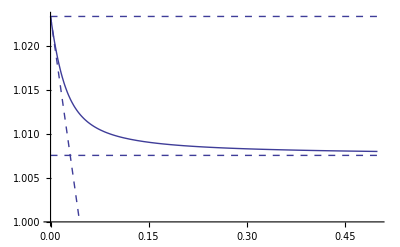

```mathematica
Show[
Plot[eigens,{R,0,1/2},PlotRange->{1,All}],
Plot[norec,{R,0,1/2},PlotRange->{1,All},PlotStyle->Dashed],
Plot[smallrec,{R,0,1/2},PlotRange->{1,All},PlotStyle->Dashed],
Plot[largerec,{R,0,1/2},PlotRange->{1,All},PlotStyle->Dashed]
]
```

```mathematica
Collect[-(Faa (-1+pAveM)^2 wa^2+pAveM wA (-2 FAa (-1+pAveM) wa+FAA pAveM wA))/(meanF ((-1+pAveM) wa-pAveM wA)),{meanF,FAA,FAa,Faa}]
```

(-(Faa (-1+pAveM)^2 wa^2)/((-1+pAveM) wa-pAveM wA)+(2 FAa (-1+pAveM) pAveM wa wA)/((-1+pAveM) wa-pAveM wA)-(FAA pAveM^2 wA^2)/((-1+pAveM) wa-pAveM wA))/meanF

#### IntStab

We check stability by perturbing the system slightly and checking that allele frequencies return. dev gives the initial deviations:

```mathematica
devXf=0.05;
devXm=-0.05;
devYm=0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=10;
```

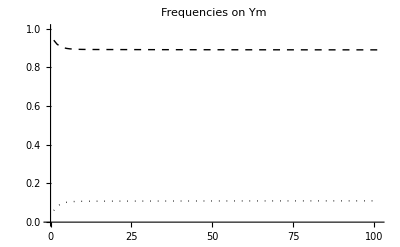

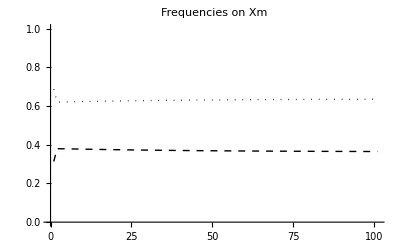

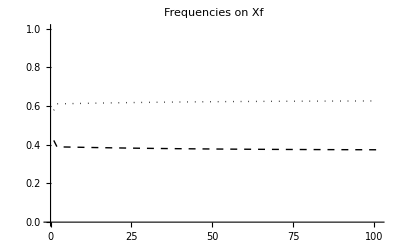

```mathematica
Show[
ListPlot[
Table[
nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Ym"]

Show[
ListPlot[
Table[
nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xm"]

Show[
ListPlot[
Table[
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xf"]
```

#### Ext Stab

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequencies.

```mathematica
pM=0.0001;

trypMXAf=pM initialpXf;
trypMXaf=pM (1-initialpXf);
trypMXAm=pM(1-tryα) initialpXm;
trypMXam=pM (1-tryα)(1-initialpXm);
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM (tryα)initialpYm;
trypMYam=pM(tryα)(1-initialpYm);
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=5000;
tinterval=100;
tplotinterval=1000;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

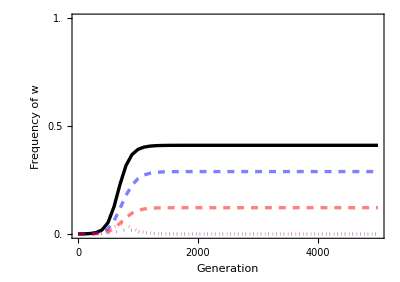

```mathematica
ListPlot[{Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of w"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

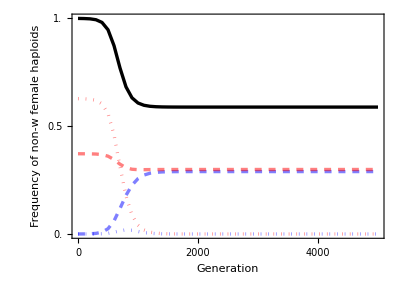

```mathematica
ListPlot[{Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

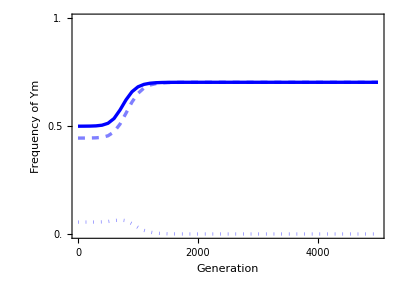

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

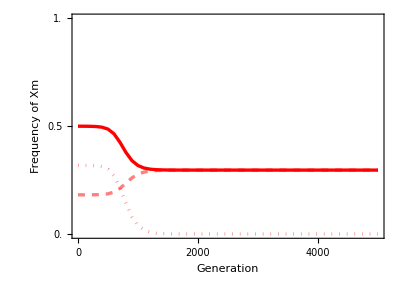

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

#### Sex ratio plot

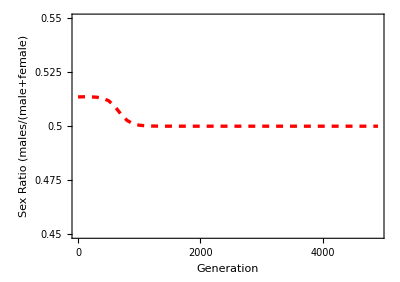

```mathematica
yplotminSexRatio=0.45;
yplotmaxSexRatio=0.55;
yplotintervalSexRatio=0.025;


ListPlot[{Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Sex Ratio (males/(male+female)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}]
```

### Iterate Recursions (W appears to reach 50% after a long time, X not yet completely lost at the end of simulation though)

#### Parameters:

```mathematica
trysAf=0.07;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.15;
tryt=-0.1;

tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
trywA=1+tryt;
trywa=1;
tryr=0.01;
tryα=0.5;
```

Our invasion analysis indicates that invasion should occur when the following is positive (which assumes that hAm=hAf)

```mathematica
((-1+2 tryr) trysAf (trysAf-trysAm) tryt^2)/(2 tryr (trysAf+trysAm)^2)
```

0.0566942

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=0.5;
```

#### Find equilibrium (equil and sieve functions) [enter]

```mathematica
initialpXf=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[1]]
initialpXm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[2]]
initialYAf=0;
initialYaf=0;
initialpYm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[3]]
```

0.770449

0.77974

0.147112

#### IntStab

We check stability by perturbing the system slightly and checking that allele frequencies return. dev gives the initial deviations:

```mathematica
devXf=0.05;
devXm=-0.05;
devYm=0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=10;
```

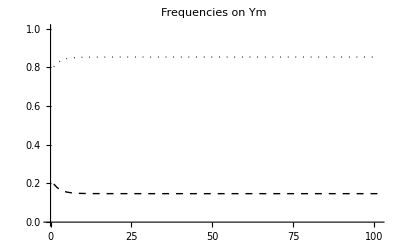

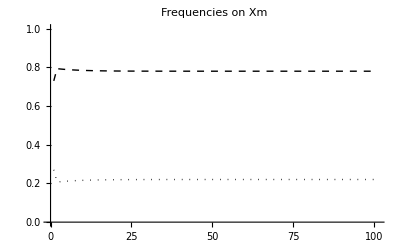

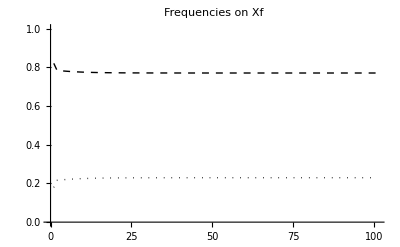

```mathematica
Show[
ListPlot[
Table[
nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Ym"]

Show[
ListPlot[
Table[
nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xm"]

Show[
ListPlot[
Table[
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xf"]
```

#### Ext Stab

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequencies.

```mathematica
pM=0.0001;

trypMXAf=pM initialpXf;
trypMXaf=pM (1-initialpXf);
trypMXAm=pM(1-tryα) initialpXm;
trypMXam=pM (1-tryα)(1-initialpXm);
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM (tryα)initialpYm;
trypMYam=pM(tryα)(1-initialpYm);
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=70000;
tinterval=100;
tplotinterval=10000;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

```mathematica
ListPlot[{Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of w"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

$Aborted

Frequency of w at the end of the simulation:

```mathematica
Total[{nextYAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]
```

0.499104

which is increasing slightly.

```mathematica
Total[{nextYAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]-
Total[{nextYAwf[69000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[69000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[69000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[69000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]
```

0.0000192522

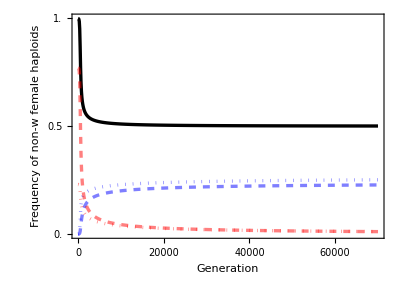

```mathematica
ListPlot[{Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

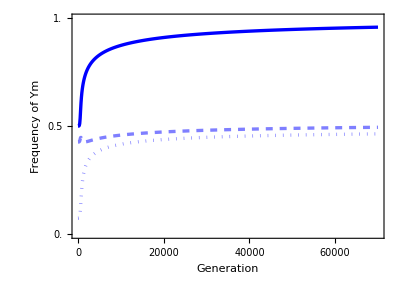

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

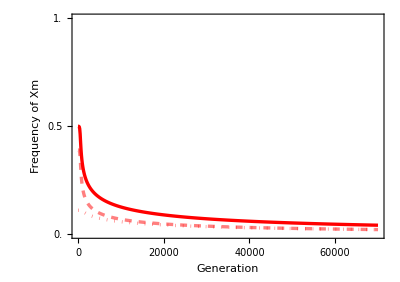

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

#### Sex ratio plot

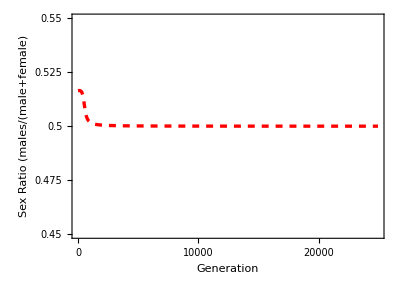

```mathematica
yplotminSexRatio=0.45;
yplotmaxSexRatio=0.55;
yplotintervalSexRatio=0.025;


ListPlot[{Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Sex Ratio (males/(male+female)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}]
```

### Iterate Recursions (W invades but does not replace XY, polymorphic sex determination maintained without loss of variation)

#### Parameters:

```mathematica
trysAf=0.1;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.15;
tryt=-0.1;

tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
trywA=1+tryt;
trywa=1;
tryr=0.01;
tryα=0.5;
```

Our invasion analysis indicates that invasion should occur when the following is positive (which assumes that hAm=hAf)

```mathematica
((-1+2 tryr) trysAf (trysAf-trysAm) tryt^2)/(2 tryr (trysAf+trysAm)^2)
```

0.0392

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=1/2;
```

#### Find equilibrium (equil and sieve functions) [enter]

```mathematica
initialpXf=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[1]]
initialpXm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[2]]
initialYAf=0;
initialYaf=0;
initialpYm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[3]]
```

0.834904

0.840045

0.15054

#### IntStab

We check stability by perturbing the system slightly and checking that allele frequencies return. dev gives the initial deviations:

```mathematica
devXf=0.05;
devXm=-0.05;
devYm=0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=10;
```

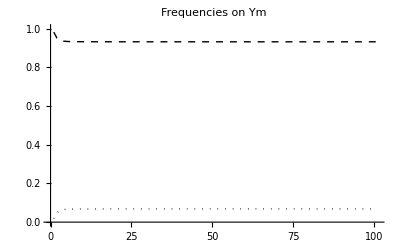

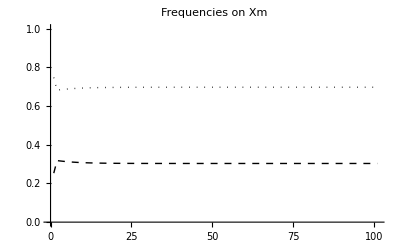

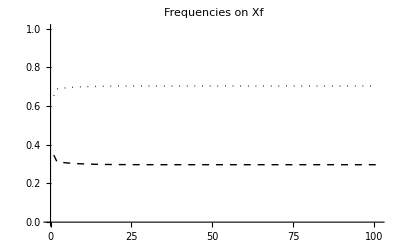

```mathematica
Show[
ListPlot[
Table[
nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Ym"]

Show[
ListPlot[
Table[
nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xm"]

Show[
ListPlot[
Table[
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xf"]
```

#### Ext Stab

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequencies.

```mathematica
pM=0.0001;

trypMXAf=pM initialpXf;
trypMXaf=pM (1-initialpXf);
trypMXAm=pM(1-tryα) initialpXm;
trypMXam=pM (1-tryα)(1-initialpXm);
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM (tryα)initialpYm;
trypMYam=pM(tryα)(1-initialpYm);
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=10000;
tinterval=100;
tplotinterval=2500;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

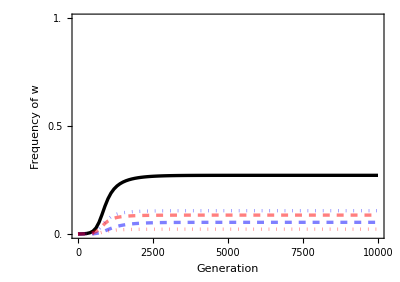

```mathematica
ListPlot[{Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of w"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

Frequency of w at the end of the simulation:

```mathematica
Total[{nextYAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]
```

0.272086

which is barely changing:

```mathematica
Total[{nextYAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]-
Total[{nextYAwf[tmax-1000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[tmax-1000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[tmax-1000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[tmax-1000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]
```

3.70147×10^-8

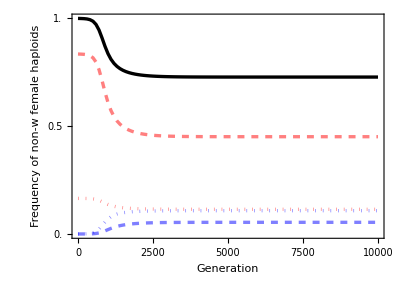

```mathematica
ListPlot[{Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

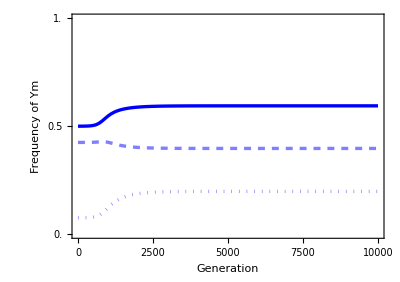

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

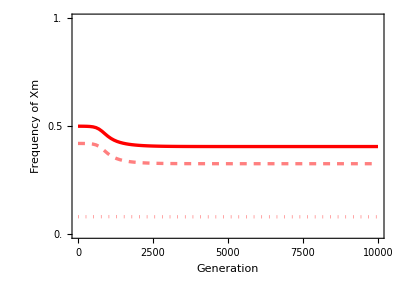

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

#### Sex ratio plot

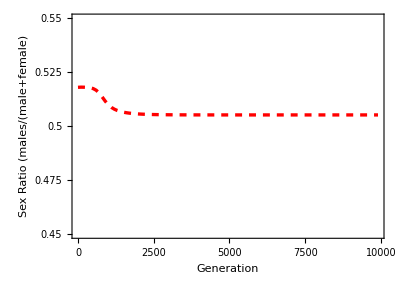

```mathematica
yplotminSexRatio=0.45;
yplotmaxSexRatio=0.55;
yplotintervalSexRatio=0.025;


ListPlot[{Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Sex Ratio (males/(male+female)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}]
```

```mathematica
sexRatioAtBirth[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
```

0.505227

# B. Maternal control (ESD invades XY)

## Life-cycle

Haploid selection

```mathematica
Subscript[wbarHap, sex_]:=Subscript[wbarHap, sex]=ParallelSum[Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex,zzPar],{x,{X,Y}},{y,{A,a}},{z,{M,m}},{zzPar,{MM,Mm,mm}}];
Subscript[fHapSel, x_,y_,z_,sex_,zzPar_]:=Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex,zzPar]/Subscript[wbarHap, sex]
```

Random mating

```mathematica
Subscript[fDip, xM_,yM_,zM_,xP_,yP_,zP_,zzM_]:=Subscript[fDip, xM,yM,zM,xP,yP,zP,zzM]=ParallelSum[Subscript[fHapSel, xM,yM,zM,female,zzM] Subscript[fHapSel, xP,yP,zP,male,zzP],{zzP,{MM,Mm,mm}}]
```

Sex determination

```mathematica
Subscript[fDipSex, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]=ParallelSum[Subscript[fDip, xM,yM,zM,xP,yP,zP,zzM] Subscript[psex, xP,zzM,sex],{zzM,{MM,Mm,mm}}]
```

where a diploid must become male or female

```mathematica
sumsex=Subscript[psex, xP_,zzM_,male]->1-Subscript[psex, xP,zzM,female];
```

We assume the invasion of a dominant modifier into an XY system

```mathematica
invXY={
Subscript[psex, Y,MM,female]->0,(*always male if mother wildtype at ESD and get Y from father*)
Subscript[psex, X,MM,female]->1,(*always female if mother wildtype at ESD and get X from father*)
Subscript[fHap, Y,y_,z_,female,MM]->0,(*no Y chromosome in eggs if mother was homozygous wildtype at ESD*)
Subscript[psex, xP_,Mm,female]->k,
Subscript[psex, xP_,mm,female]->k(*female with probability k if mother had mutation at the ESD*)
};
```

Diploid selection

```mathematica
Subscript[wbarDip, sex_]:=Subscript[wbarDip, sex]=ParallelSum[Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}];
Subscript[fDipSel, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex]=Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]/Subscript[wbarDip, sex]
```

Meiosis

```mathematica
Subscript[fHapNext, x_,y_,z_,sex_,zzPar_]:=Subscript[fHapNext, x,y,z,sex,zzPar]=ParallelSum[Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex] Subscript[pseg, xM,yM,zM,xP,yP,zP,sex,x,y,z,zzPar],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}]
```

Segregation rules

```mathematica
pseg0={
(*triple homozygote*)
Subscript[pseg, x1_,y1_,M,x1_,y1_,M,sex_,x1_,y1_,M,MM]->1,
Subscript[pseg, x1_,y1_,m,x1_,y1_,m,sex_,x1_,y1_,m,mm]->1,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z1_,sex_,x1_,y1_,z1_,Mm]->0
};
pseg1={
(*single heterozygotes*)
Subscript[pseg, x1_,y1_,M,x2_,y1_,M,sex_,x1_,y1_,M,MM]->1/2,
Subscript[pseg, x1_,y1_,M,x2_,y1_,M,sex_,x2_,y1_,M,MM]->1/2,
Subscript[pseg, x1_,y1_,M,x1_,y2_,M,sex_,x1_,y1_,M,MM]->1/2,
Subscript[pseg, x1_,y1_,M,x1_,y2_,M,sex_,x1_,y2_,M,MM]->1/2,
Subscript[pseg, x1_,y1_,m,x2_,y1_,m,sex_,x1_,y1_,M,mm]->1/2,
Subscript[pseg, x1_,y1_,m,x2_,y1_,m,sex_,x2_,y1_,M,mm]->1/2,
Subscript[pseg, x1_,y1_,m,x1_,y2_,m,sex_,x1_,y1_,M,mm]->1/2,
Subscript[pseg, x1_,y1_,m,x1_,y2_,m,sex_,x1_,y2_,M,mm]->1/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x1_,y1_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x2_,y1_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z1_,sex_,x1_,y1_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z1_,sex_,x1_,y2_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z1_,Mm]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z2_,Mm]->1/2
};
pseg2={
(*double heterozygotes*)
Subscript[pseg, x1_,y1_,M,x2_,y2_,M,sex_,x1_,y1_,M,MM]->(1-r)/2,
Subscript[pseg, x1_,y1_,M,x2_,y2_,M,sex_,x2_,y2_,M,MM]->(1-r)/2,
Subscript[pseg, x1_,y1_,M,x2_,y2_,M,sex_,x2_,y1_,M,MM]->r/2,
Subscript[pseg, x1_,y1_,M,x2_,y2_,M,sex_,x1_,y2_,M,MM]->r/2,
Subscript[pseg, x1_,y1_,m,x2_,y2_,m,sex_,x1_,y1_,m,mm]->(1-r)/2,
Subscript[pseg, x1_,y1_,m,x2_,y2_,m,sex_,x2_,y2_,m,mm]->(1-r)/2,
Subscript[pseg, x1_,y1_,m,x2_,y2_,m,sex_,x2_,y1_,m,mm]->r/2,
Subscript[pseg, x1_,y1_,m,x2_,y2_,m,sex_,x1_,y2_,m,mm]->r/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x1_,y1_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x2_,y2_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x2_,y1_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x1_,y2_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y1_,z1_,Mm]->(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y2_,z2_,Mm]->(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y2_,z1_,Mm]->R/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y1_,z2_,Mm]->R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z1_,Mm]->((1-r)(1-R)+r R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z2_,Mm]->((1-r)(1-R)+r R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z1_,Mm]->(r(1-R)+(1-r)R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z2_,Mm]->(r(1-R)+(1-r)R)/2
};
pseg3={
(*triple heterozygote*)
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y1_,z1_,Mm]->(1-r)(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y2_,z2_,Mm]->(1-r)(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y1_,z1_,Mm]->r(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y2_,z2_,Mm]->r(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y2_,z1_,Mm]->r R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y1_,z2_,Mm]->r R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y1_,z2_,Mm]->(1-r)R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y2_,z1_,Mm]->(1-r)R/2
};
pseg4=Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x_,y_,z_,zzM_]->0;
```

```mathematica
(*ParallelSum[Subscript[fHapNext, x,y,z,sex,zzM]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4,{x,{X,Y}},{y,{A,a}},{z,{M,m}},{sex,{male,female}},{zzM,{MM,Mm,mm}}]//Factor*)
```

## Resident equilibrium (weak selection)

We begin with no mutations at the modifer locus in haploids or mothers

```mathematica
subequil={
Subscript[fHap, X,A,M,female,MM]->pXf,
Subscript[fHap, X,a,M,female,MM]->1-pXf,
Subscript[fHap, X,A,M,male,MM]->(1-α) pXm,
Subscript[fHap, X,a,M,male,MM]->(1-α)(1-pXm),
Subscript[fHap, Y,A,M,male,MM]->α pYm,
Subscript[fHap, Y,a,M,male,MM]->α(1-pYm),
Subscript[fHap, x_,y_,m,sex_,zzM_]->0,
Subscript[fHap, x_,y_,z_,sex_,Mm]->0,
Subscript[fHap, x_,y_,z_,sex_,mm]->0
}/.α->1/2;
```

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following three equations are zero (this takes a minute)

```mathematica
differenceEqs={
Subscript[fHapNext, X,A,M,female,MM]-Subscript[fHap, X,A,M,female,MM],
Subscript[fHapNext, X,A,M,male,MM]-Subscript[fHap, X,A,M,male,MM],
Subscript[fHapNext, Y,A,M,male,MM]-Subscript[fHap, Y,A,M,male,MM]
}/.subequil/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
```

To simplify the analysis we assume weak selection in both haploids and diploids. In addition, we assume selection acts on the VS locus only

```mathematica
weaksel={
Subscript[wHap, A,sex_]->1,
Subscript[wHap, a,sex_]->1+Subscript[sHap, sex] ϵ,
Subscript[wDip, A,A,sex_]->1,
Subscript[wDip, A,a,sex_]->1+Subscript[h, sex] Subscript[sDip, sex] ϵ,
Subscript[wDip, a,A,sex_]->1+Subscript[h, sex] Subscript[sDip, sex] ϵ,
Subscript[wDip, a,a,sex_]->1+ Subscript[sDip, sex] ϵ
};
```

We can write the frequencies as Taylor series

```mathematica
frequenciessub={
pXf->pXf0+pXf1 ϵ,
pXm->pXm0+pXm1 ϵ,
pYm->pYm0+pYm1 ϵ
};
```

Without selection the recursions for the change in the frequencies are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weaksel/.frequenciessub,{ϵ,0,0}]]//Factor
```

{1/2 (-pXf0+pXm0),1/2 (pXf0-pXm0-pXf0 r+pYm0 r),1/2 (pXf0-pYm0) r}

And at equilibrium we have

```mathematica
sol0=Solve[differenceEqs0==0,{pYm0,pXm0}]//Flatten
```

{pYm0→pXf0,pXm0→pXf0}

So, with no selection, the equilibrium frequency of A in each gamete/pollen type is equal (and we call this pA).

Now, looking at only the first order selection terms, the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs1=Collect[Normal[Series[differenceEqs/.weaksel/.frequenciessub/.sol0,{ϵ,0,1}]],ϵ,Factor]/.pXf0->pA//Flatten
```

{1/2 ϵ (-pXf1+pXm1-2 pA sDip_female+4 pA^2 sDip_female-2 pA^3 sDip_female+2 pA h_female sDip_female-6 pA^2 h_female sDip_female+4 pA^3 h_female sDip_female-pA sHap_female+pA^2 sHap_female-pA sHap_male+pA^2 sHap_male),1/2 ϵ (pXf1-pXm1-pXf1 r+pYm1 r-pA sDip_male+2 pA^2 sDip_male-pA^3 sDip_male+pA h_male sDip_male-3 pA^2 h_male sDip_male+2 pA^3 h_male sDip_male-pA sHap_female+pA^2 sHap_female+pA r sHap_female-pA^2 r sHap_female-pA r sHap_male+pA^2 r sHap_male),1/2 ϵ (pXf1 r-pYm1 r-pA sDip_male+2 pA^2 sDip_male-pA^3 sDip_male+pA h_male sDip_male-3 pA^2 h_male sDip_male+2 pA^3 h_male sDip_male-pA r sHap_female+pA^2 r sHap_female-pA sHap_male+pA^2 sHap_male+pA r sHap_male-pA^2 r sHap_male)}

And we can solve for the two of the first order differences and the mean frequency of A

```mathematica
realsol=Solve[differenceEqs1==0/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{dpAXmXf,dpAYmXf,pA}]//Factor
```

{{dpAXmXf→0,dpAYmXf→0,pA→0},{dpAXmXf→0,dpAYmXf→0,pA→1},{dpAXmXf→-((-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male) (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male) (2 h_female sDip_female sDip_male-2 h_male sDip_female sDip_male-sDip_female sHap_female+2 h_female sDip_female sHap_female+sDip_male sHap_female-2 h_male sDip_male sHap_female-sDip_female sHap_male+2 h_female sDip_female sHap_male+sDip_male sHap_male-2 h_male sDip_male sHap_male))/(-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)^3,dpAYmXf→-((-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male) (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male) (h_female sDip_female sDip_male-h_male sDip_female sDip_male-r sDip_female sHap_female+2 r h_female sDip_female sHap_female+sDip_male sHap_female-r sDip_male sHap_female-2 h_male sDip_male sHap_female+2 r h_male sDip_male sHap_female-sDip_female sHap_male+r sDip_female sHap_male+2 h_female sDip_female sHap_male-2 r h_female sDip_female sHap_male+r sDip_male sHap_male-2 r h_male sDip_male sHap_male))/(r (-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)^3),pA→(-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male)/(-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)}}

Print this out so that we do not have to re-run all the above

```mathematica
realsol={{dpAXmXf->0,dpAYmXf->0,pA->0},{dpAXmXf->0,dpAYmXf->0,pA->1},{dpAXmXf->-((-Subscript[sDip, female]+Subscript[h, female] Subscript[sDip, female]-Subscript[sDip, male]+Subscript[h, male] Subscript[sDip, male]-Subscript[sHap, female]-Subscript[sHap, male]) (Subscript[h, female] Subscript[sDip, female]+Subscript[h, male] Subscript[sDip, male]+Subscript[sHap, female]+Subscript[sHap, male]) (2 Subscript[h, female] Subscript[sDip, female] Subscript[sDip, male]-2 Subscript[h, male] Subscript[sDip, female] Subscript[sDip, male]-Subscript[sDip, female] Subscript[sHap, female]+2 Subscript[h, female] Subscript[sDip, female] Subscript[sHap, female]+Subscript[sDip, male] Subscript[sHap, female]-2 Subscript[h, male] Subscript[sDip, male] Subscript[sHap, female]-Subscript[sDip, female] Subscript[sHap, male]+2 Subscript[h, female] Subscript[sDip, female] Subscript[sHap, male]+Subscript[sDip, male] Subscript[sHap, male]-2 Subscript[h, male] Subscript[sDip, male] Subscript[sHap, male]))/(-Subscript[sDip, female]+2 Subscript[h, female] Subscript[sDip, female]-Subscript[sDip, male]+2 Subscript[h, male] Subscript[sDip, male])^3,dpAYmXf->-((-Subscript[sDip, female]+Subscript[h, female] Subscript[sDip, female]-Subscript[sDip, male]+Subscript[h, male] Subscript[sDip, male]-Subscript[sHap, female]-Subscript[sHap, male]) (Subscript[h, female] Subscript[sDip, female]+Subscript[h, male] Subscript[sDip, male]+Subscript[sHap, female]+Subscript[sHap, male]) (Subscript[h, female] Subscript[sDip, female] Subscript[sDip, male]-Subscript[h, male] Subscript[sDip, female] Subscript[sDip, male]-r Subscript[sDip, female] Subscript[sHap, female]+2 r Subscript[h, female] Subscript[sDip, female] Subscript[sHap, female]+Subscript[sDip, male] Subscript[sHap, female]-r Subscript[sDip, male] Subscript[sHap, female]-2 Subscript[h, male] Subscript[sDip, male] Subscript[sHap, female]+2 r Subscript[h, male] Subscript[sDip, male] Subscript[sHap, female]-Subscript[sDip, female] Subscript[sHap, male]+r Subscript[sDip, female] Subscript[sHap, male]+2 Subscript[h, female] Subscript[sDip, female] Subscript[sHap, male]-2 r Subscript[h, female] Subscript[sDip, female] Subscript[sHap, male]+r Subscript[sDip, male] Subscript[sHap, male]-2 r Subscript[h, male] Subscript[sDip, male] Subscript[sHap, male]))/(r (-Subscript[sDip, female]+2 Subscript[h, female] Subscript[sDip, female]-Subscript[sDip, male]+2 Subscript[h, male] Subscript[sDip, male])^3),pA->(-Subscript[sDip, female]+Subscript[h, female] Subscript[sDip, female]-Subscript[sDip, male]+Subscript[h, male] Subscript[sDip, male]-Subscript[sHap, female]-Subscript[sHap, male])/(-Subscript[sDip, female]+2 Subscript[h, female] Subscript[sDip, female]-Subscript[sDip, male]+2 Subscript[h, male] Subscript[sDip, male])}};
```

## Resident stability (weak selection) [do not need to re-run if unchanged]

Here we use linear stability analysis to examine when the resident equilibrium (i.e., no mutants) derived above is stable.

The Jacobian for the residents is (this takes a couple minutes)

```mathematica
eqs=Join[Table[Subscript[fHapNext, X,y,M,female,MM],{y,{A,a}}],Table[Subscript[fHapNext, x,y,M,male,MM],{x,{X,Y}},{y,{A,a}}]//Flatten]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
matIntFull=Transpose[{
D[eqs,Subscript[fHap, X,A,M,female,MM]],
D[eqs,Subscript[fHap, X,a,M,female,MM]],
D[eqs,Subscript[fHap, X,A,M,male,MM]],
D[eqs,Subscript[fHap, X,a,M,male,MM]],
D[eqs,Subscript[fHap, Y,A,M,male,MM]],
D[eqs,Subscript[fHap, Y,a,M,male,MM]]
}]/.subequil//Factor;
```

From this we can derive the characteristic polynomial

```mathematica
charpolyIntFull=Det[matIntFull-IdentityMatrix[6]*λ];
```

Instead of examining when the non-trivial equilibrium (A not fixed or lost) is stable we will look for when the trivial equilibria (loss or fixation of A) are unstable.

When A is fixed the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt1=charpolyIntFull/.pXm->1/.pXf->1/.pYm->1;
Normal[Series[charpolyInt1/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Factor//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

and λ=1 is the leading eigenvalue.

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt1/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1fix=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male)}

And so the fixation of A is unstable when this expression is positive.

When A is lost the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt0=charpolyIntFull/.pXm->0/.pXf->0/.pYm->0;
Normal[Series[charpolyInt0/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt0/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1loss=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male)}

And so the loss of A is unstable when this expression is positive.

Combining the two results, the protected polymorphism (non-trivial equilibrium) requires that

```mathematica
stabconds={(δλ1/.δλ1fix)<0,(δλ1/.δλ1loss)<0};
```

## Sex chromosome turnover (weak selection) [slow, ~15 minutes]

Here we are interested in the ability of a rare mutant at the ESD locus to invade the non-mutant resident population at equilibrium.

The Jacobian for the mutants is (this takes a minute or two, or ten)

```mathematica
eqsmut=Table[Subscript[fHapNext, x,y,m,sex,Mm],{sex,{female,male}},{y,{A,a}},{x,{X,Y}}]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4//Flatten;
```

```mathematica
matExtFull=Transpose[{
D[eqsmut,Subscript[fHap, X,A,m,female,Mm]],
D[eqsmut,Subscript[fHap, Y,A,m,female,Mm]],
D[eqsmut,Subscript[fHap, X,a,m,female,Mm]],
D[eqsmut,Subscript[fHap, Y,a,m,female,Mm]],
D[eqsmut,Subscript[fHap, X,A,m,male,Mm]],
D[eqsmut,Subscript[fHap, Y,A,m,male,Mm]],
D[eqsmut,Subscript[fHap, X,a,m,male,Mm]],
D[eqsmut,Subscript[fHap, Y,a,m,male,Mm]]
}]/.subequil//Factor;
```

And the characteristic polynomial

```mathematica
charpolyExt=Det[matExtFull-IdentityMatrix[8]*λ];
```

Solving for the eigenvalues with no selection gives

```mathematica
charploy0=Normal[Series[charpolyExt/.weaksel,{ϵ,0,0}]]//Factor;
charploy0sol=Solve[%==0,λ]//Flatten//Simplify;
```

Lets plot these

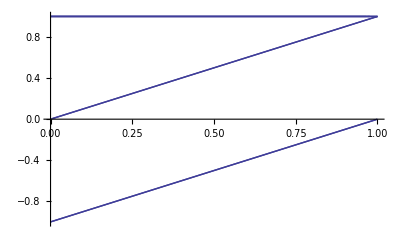
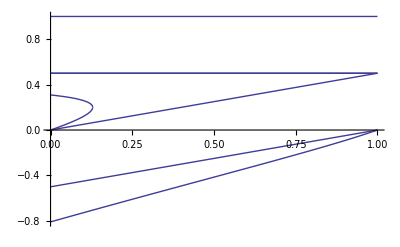
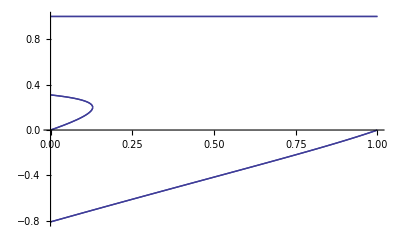
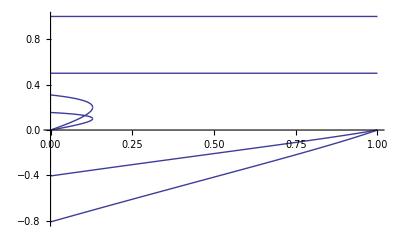

```mathematica
Table[Show[Table[Plot[λ/.charploy0sol[[i]],{k,0,1}],{i,1,Length[charploy0sol]}],PlotRange->All],{r,{0,0.5}},{R,{0,0.5}}]
```

And so it looks like on this order the leading eigenvalue is λ=1.

On the first order the eiganvalue is

```mathematica
Normal[Series[charpolyExt/.weaksel/.λ->1+δλ*ϵ/.frequenciessub/.sol0/.pXf0->pA,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ]
```

{{δλ→0}}

And on the 2nd order (this takes a few minutes)

```mathematica
Normal[Series[charpolyExt/.weaksel/.λ->1+δλ2*ϵ^2/.frequenciessub/.sol0/.pXf0->pA/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2];
lambda2diffs=Collect[δλ2/.%,{dpAXmXf,dpAYmXf},Simplify];
```

Then we can put in all the differences

```mathematica
tester=Collect[lambda2diffs/.realsol[[3]],{dpAXmXf,dpAYmXf},Simplify];
```

Print this out so that we can use without having to re-run all the above

```mathematica
tester={(((-1+Subscript[h, female]) Subscript[sDip, female]+(-1+Subscript[h, male]) Subscript[sDip, male]-Subscript[sHap, female]-Subscript[sHap, male]) (Subscript[h, female] Subscript[sDip, female]+Subscript[h, male] Subscript[sDip, male]+Subscript[sHap, female]+Subscript[sHap, male]) (-(-(Subscript[sDip, female]-Subscript[sDip, male]) (Subscript[sHap, female]+Subscript[sHap, male])-2 Subscript[h, male] Subscript[sDip, male] (Subscript[sDip, female]+Subscript[sHap, female]+Subscript[sHap, male])+2 Subscript[h, female] Subscript[sDip, female] (Subscript[sDip, male]+Subscript[sHap, female]+Subscript[sHap, male])) ((-2 (1+k (-1+R))^2 R (1+(-1+k) R)+2 k^2 r^3 (-1+R)^2 (-1+2 R) (1+(-1+k) R)-k r^2 (-1+R) (-4+11 R-8 R^2+2 k^2 R (2-6 R+5 R^2)+k (4-21 R+30 R^2-10 R^3))+r (-2 (-1+R)^2+2 k^3 (1-2 R)^2 (-1+R) R+k (4-18 R+25 R^2-11 R^3)+k^2 (-2+16 R-39 R^2+35 R^3-8 R^4))) (Subscript[sHap, female]-Subscript[sHap, male])-((-1+k) (-2 (1+k (-1+R))^2 R (3-2 R+k (-1+2 R))+2 k^2 r^3 (-1+R)^2 (-1+2 R) (3-2 R+k (-1+2 R))+r (-8+14 R-6 R^2+2 k^3 (-1+R) (-1+2 R)^3+k (17-59 R+65 R^2-22 R^3)+k^2 (-11+58 R-107 R^2+78 R^3-16 R^4))+k r^2 (-14+45 R-46 R^2+16 R^3+k^2 (-4+24 R-54 R^2+54 R^3-20 R^4)+k (17-79 R+132 R^2-90 R^3+20 R^4))) Subscript[sDip, male] (Subscript[h, female] Subscript[sDip, female]+Subscript[sHap, female]+Subscript[sHap, male]-Subscript[h, male] (Subscript[sDip, female]+2 (Subscript[sHap, female]+Subscript[sHap, male]))))/((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male])-((-1+k) (-2 (1+k (-1+R))^2 R (3-2 R+k (-1+2 R))+2 k^2 r^3 (-1+R)^2 (-1+2 R) (3-2 R+k (-1+2 R))+r (-8+14 R-6 R^2+2 k^3 (-1+R) (-1+2 R)^3+k (17-59 R+65 R^2-22 R^3)+k^2 (-11+58 R-107 R^2+78 R^3-16 R^4))+k r^2 (-14+45 R-46 R^2+16 R^3+k^2 (-4+24 R-54 R^2+54 R^3-20 R^4)+k (17-79 R+132 R^2-90 R^3+20 R^4))) Subscript[sDip, female] (-Subscript[h, male] Subscript[sDip, male]-Subscript[sHap, female]-Subscript[sHap, male]+Subscript[h, female] (Subscript[sDip, male]+2 (Subscript[sHap, female]+Subscript[sHap, male]))))/((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male]))-1/r(-r Subscript[sDip, female] Subscript[sHap, female]+Subscript[sDip, male] Subscript[sHap, female]-r Subscript[sDip, male] Subscript[sHap, female]-Subscript[sDip, female] Subscript[sHap, male]+r Subscript[sDip, female] Subscript[sHap, male]+r Subscript[sDip, male] Subscript[sHap, male]-Subscript[h, male] Subscript[sDip, male] (Subscript[sDip, female]+2 Subscript[sHap, female]-2 r Subscript[sHap, female]+2 r Subscript[sHap, male])+Subscript[h, female] Subscript[sDip, female] (Subscript[sDip, male]+2 (r Subscript[sHap, female]+Subscript[sHap, male]-r Subscript[sHap, male]))) (-2 r Subscript[sHap, female]+4 k r Subscript[sHap, female]-2 k^2 r Subscript[sHap, female]-4 k r^2 Subscript[sHap, female]+4 k^2 r^2 Subscript[sHap, female]-2 k^2 r^3 Subscript[sHap, female]+2 r R Subscript[sHap, female]-12 k r R Subscript[sHap, female]+12 k^2 r R Subscript[sHap, female]-2 k^3 r R Subscript[sHap, female]+13 k r^2 R Subscript[sHap, female]-23 k^2 r^2 R Subscript[sHap, female]+4 k^3 r^2 R Subscript[sHap, female]+10 k^2 r^3 R Subscript[sHap, female]-2 k^3 r^3 R Subscript[sHap, female]-4 k R^2 Subscript[sHap, female]+6 k^2 R^2 Subscript[sHap, female]-2 k^3 R^2 Subscript[sHap, female]+13 k r R^2 Subscript[sHap, female]-29 k^2 r R^2 Subscript[sHap, female]+10 k^3 r R^2 Subscript[sHap, female]-13 k r^2 R^2 Subscript[sHap, female]+45 k^2 r^2 R^2 Subscript[sHap, female]-16 k^3 r^2 R^2 Subscript[sHap, female]-18 k^2 r^3 R^2 Subscript[sHap, female]+8 k^3 r^3 R^2 Subscript[sHap, female]+2 k R^3 Subscript[sHap, female]-8 k^2 R^3 Subscript[sHap, female]+4 k^3 R^3 Subscript[sHap, female]-5 k r R^3 Subscript[sHap, female]+29 k^2 r R^3 Subscript[sHap, female]-16 k^3 r R^3 Subscript[sHap, female]+4 k r^2 R^3 Subscript[sHap, female]-36 k^2 r^2 R^3 Subscript[sHap, female]+22 k^3 r^2 R^3 Subscript[sHap, female]+14 k^2 r^3 R^3 Subscript[sHap, female]-10 k^3 r^3 R^3 Subscript[sHap, female]+2 k^2 R^4 Subscript[sHap, female]-2 k^3 R^4 Subscript[sHap, female]-8 k^2 r R^4 Subscript[sHap, female]+8 k^3 r R^4 Subscript[sHap, female]+10 k^2 r^2 R^4 Subscript[sHap, female]-10 k^3 r^2 R^4 Subscript[sHap, female]-4 k^2 r^3 R^4 Subscript[sHap, female]+4 k^3 r^3 R^4 Subscript[sHap, female]+7 r Subscript[sHap, male]-26 k r Subscript[sHap, male]+35 k^2 r Subscript[sHap, male]-20 k^3 r Subscript[sHap, male]+4 k^4 r Subscript[sHap, male]+8 k r^2 Subscript[sHap, male]-28 k^2 r^2 Subscript[sHap, male]+28 k^3 r^2 Subscript[sHap, male]-8 k^4 r^2 Subscript[sHap, male]+2 k^2 r^3 Subscript[sHap, male]-8 k^3 r^3 Subscript[sHap, male]+4 k^4 r^3 Subscript[sHap, male]+4 R Subscript[sHap, male]-18 k R Subscript[sHap, male]+28 k^2 R Subscript[sHap, male]-18 k^3 R Subscript[sHap, male]+4 k^4 R Subscript[sHap, male]-10 r R Subscript[sHap, male]+56 k r R Subscript[sHap, male]-114 k^2 r R Subscript[sHap, male]+92 k^3 r R Subscript[sHap, male]-24 k^4 r R Subscript[sHap, male]-23 k r^2 R Subscript[sHap, male]+95 k^2 r^2 R Subscript[sHap, male]-118 k^3 r^2 R Subscript[sHap, male]+40 k^4 r^2 R Subscript[sHap, male]-10 k^2 r^3 R Subscript[sHap, male]+38 k^3 r^3 R Subscript[sHap, male]-20 k^4 r^3 R Subscript[sHap, male]-2 R^2 Subscript[sHap, male]+18 k R^2 Subscript[sHap, male]-46 k^2 R^2 Subscript[sHap, male]+42 k^3 R^2 Subscript[sHap, male]-12 k^4 R^2 Subscript[sHap, male]+3 r R^2 Subscript[sHap, male]-39 k r R^2 Subscript[sHap, male]+132 k^2 r R^2 Subscript[sHap, male]-154 k^3 r R^2 Subscript[sHap, male]+52 k^4 r R^2 Subscript[sHap, male]+21 k r^2 R^2 Subscript[sHap, male]-113 k^2 r^2 R^2 Subscript[sHap, male]+184 k^3 r^2 R^2 Subscript[sHap, male]-76 k^4 r^2 R^2 Subscript[sHap, male]+18 k^2 r^3 R^2 Subscript[sHap, male]-64 k^3 r^3 R^2 Subscript[sHap, male]+36 k^4 r^3 R^2 Subscript[sHap, male]-4 k R^3 Subscript[sHap, male]+20 k^2 R^3 Subscript[sHap, male]-30 k^3 R^3 Subscript[sHap, male]+12 k^4 R^3 Subscript[sHap, male]+9 k r R^3 Subscript[sHap, male]-59 k^2 r R^3 Subscript[sHap, male]+106 k^3 r R^3 Subscript[sHap, male]-48 k^4 r R^3 Subscript[sHap, male]-6 k r^2 R^3 Subscript[sHap, male]+56 k^2 r^2 R^3 Subscript[sHap, male]-124 k^3 r^2 R^3 Subscript[sHap, male]+64 k^4 r^2 R^3 Subscript[sHap, male]-14 k^2 r^3 R^3 Subscript[sHap, male]+46 k^3 r^3 R^3 Subscript[sHap, male]-28 k^4 r^3 R^3 Subscript[sHap, male]-2 k^2 R^4 Subscript[sHap, male]+6 k^3 R^4 Subscript[sHap, male]-4 k^4 R^4 Subscript[sHap, male]+8 k^2 r R^4 Subscript[sHap, male]-24 k^3 r R^4 Subscript[sHap, male]+16 k^4 r R^4 Subscript[sHap, male]-10 k^2 r^2 R^4 Subscript[sHap, male]+30 k^3 r^2 R^4 Subscript[sHap, male]-20 k^4 r^2 R^4 Subscript[sHap, male]+4 k^2 r^3 R^4 Subscript[sHap, male]-12 k^3 r^3 R^4 Subscript[sHap, male]+8 k^4 r^3 R^4 Subscript[sHap, male]-((-1+k) (2 (-1+k) k^2 r^3 (-1+R)^2 (-1+2 R)-2 (-1+k) R (2+k^2 (-1+R)^2-R-k (3-4 R+R^2))+r (7+2 k^3 (1-2 R)^2 (-1+R)-8 R+3 R^2+k^2 (9-32 R+37 R^2-12 R^3)+k (-14+31 R-22 R^2+4 R^3))+k r^2 (8-19 R+12 R^2-2 R^3-2 k^2 (-2+8 R-11 R^2+5 R^3)+k (-11+35 R-36 R^2+12 R^3))) Subscript[sDip, male] (Subscript[h, female] Subscript[sDip, female]+Subscript[sHap, female]+Subscript[sHap, male]-Subscript[h, male] (Subscript[sDip, female]+2 (Subscript[sHap, female]+Subscript[sHap, male]))))/((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male])-((2 k^2 r^3 (-1+R)^2 (-1+2 R) (1-2 k (-1+R)+k^2 (-1+2 R))+2 k R (-2+R-k^3 (-1+R)^2 (-1+2 R)+k (5-9 R+3 R^2)+2 k^2 (-2+6 R-5 R^2+R^3))+r (-2+2 k^4 (-1+R) (-1+2 R)^3-k (1-5 R+R^2)+k^2 (10-39 R+44 R^2-14 R^3)+k^3 (-9+48 R-91 R^2+70 R^3-16 R^4))+k r^2 (-4+9 R-4 R^2+k (-5+18 R-20 R^2+6 R^3)+k^3 (-4+24 R-54 R^2+54 R^3-20 R^4)+k^2 (13-63 R+110 R^2-80 R^3+20 R^4))) Subscript[sDip, female] (-Subscript[h, male] Subscript[sDip, male]-Subscript[sHap, female]-Subscript[sHap, male]+Subscript[h, female] (Subscript[sDip, male]+2 (Subscript[sHap, female]+Subscript[sHap, male]))))/((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male]))+(((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male])^2 (-4 r Subscript[sHap, female]^2+8 k r Subscript[sHap, female]^2-4 k^2 r Subscript[sHap, female]^2-8 k r^2 Subscript[sHap, female]^2+8 k^2 r^2 Subscript[sHap, female]^2-4 k^2 r^3 Subscript[sHap, female]^2-4 R Subscript[sHap, female]^2+8 k R Subscript[sHap, female]^2-4 k^2 R Subscript[sHap, female]^2+8 r R Subscript[sHap, female]^2-30 k r R Subscript[sHap, female]^2+22 k^2 r R Subscript[sHap, female]^2+26 k r^2 R Subscript[sHap, female]^2-38 k^2 r^2 R Subscript[sHap, female]^2+20 k^2 r^3 R Subscript[sHap, female]^2+2 R^2 Subscript[sHap, female]^2-10 k R^2 Subscript[sHap, female]^2+8 k^2 R^2 Subscript[sHap, female]^2-6 r R^2 Subscript[sHap, female]^2+40 k r R^2 Subscript[sHap, female]^2-50 k^2 r R^2 Subscript[sHap, female]^2+4 k^3 r R^2 Subscript[sHap, female]^2-32 k r^2 R^2 Subscript[sHap, female]^2+84 k^2 r^2 R^2 Subscript[sHap, female]^2-8 k^3 r^2 R^2 Subscript[sHap, female]^2-40 k^2 r^3 R^2 Subscript[sHap, female]^2+4 k^3 r^3 R^2 Subscript[sHap, female]^2-2 R^3 Subscript[sHap, female]^2+10 k R^3 Subscript[sHap, female]^2-16 k^2 R^3 Subscript[sHap, female]^2+4 k^3 R^3 Subscript[sHap, female]^2+2 r R^3 Subscript[sHap, female]^2-24 k r R^3 Subscript[sHap, female]^2+70 k^2 r R^3 Subscript[sHap, female]^2-20 k^3 r R^3 Subscript[sHap, female]^2+22 k r^2 R^3 Subscript[sHap, female]^2-106 k^2 r^2 R^3 Subscript[sHap, female]^2+32 k^3 r^2 R^3 Subscript[sHap, female]^2+44 k^2 r^3 R^3 Subscript[sHap, female]^2-16 k^3 r^3 R^3 Subscript[sHap, female]^2-4 k R^4 Subscript[sHap, female]^2+16 k^2 R^4 Subscript[sHap, female]^2-8 k^3 R^4 Subscript[sHap, female]^2+10 k r R^4 Subscript[sHap, female]^2-58 k^2 r R^4 Subscript[sHap, female]^2+32 k^3 r R^4 Subscript[sHap, female]^2-8 k r^2 R^4 Subscript[sHap, female]^2+72 k^2 r^2 R^4 Subscript[sHap, female]^2-44 k^3 r^2 R^4 Subscript[sHap, female]^2-28 k^2 r^3 R^4 Subscript[sHap, female]^2+20 k^3 r^3 R^4 Subscript[sHap, female]^2-4 k^2 R^5 Subscript[sHap, female]^2+4 k^3 R^5 Subscript[sHap, female]^2+16 k^2 r R^5 Subscript[sHap, female]^2-16 k^3 r R^5 Subscript[sHap, female]^2-20 k^2 r^2 R^5 Subscript[sHap, female]^2+20 k^3 r^2 R^5 Subscript[sHap, female]^2+8 k^2 r^3 R^5 Subscript[sHap, female]^2-8 k^3 r^3 R^5 Subscript[sHap, female]^2-12 r Subscript[sHap, female] Subscript[sHap, male]+32 k r Subscript[sHap, female] Subscript[sHap, male]-28 k^2 r Subscript[sHap, female] Subscript[sHap, male]+8 k^3 r Subscript[sHap, female] Subscript[sHap, male]-20 k r^2 Subscript[sHap, female] Subscript[sHap, male]+36 k^2 r^2 Subscript[sHap, female] Subscript[sHap, male]-16 k^3 r^2 Subscript[sHap, female] Subscript[sHap, male]-8 k^2 r^3 Subscript[sHap, female] Subscript[sHap, male]+8 k^3 r^3 Subscript[sHap, female] Subscript[sHap, male]-8 R Subscript[sHap, female] Subscript[sHap, male]+24 k R Subscript[sHap, female] Subscript[sHap, male]-24 k^2 R Subscript[sHap, female] Subscript[sHap, male]+8 k^3 R Subscript[sHap, female] Subscript[sHap, male]+11 r R Subscript[sHap, female] Subscript[sHap, male]-64 k r R Subscript[sHap, female] Subscript[sHap, male]+85 k^2 r R Subscript[sHap, female] Subscript[sHap, male]-28 k^3 r R Subscript[sHap, female] Subscript[sHap, male]-4 k^4 r R Subscript[sHap, female] Subscript[sHap, male]+52 k r^2 R Subscript[sHap, female] Subscript[sHap, male]-112 k^2 r^2 R Subscript[sHap, female] Subscript[sHap, male]+52 k^3 r^2 R Subscript[sHap, female] Subscript[sHap, male]+8 k^4 r^2 R Subscript[sHap, female] Subscript[sHap, male]+32 k^2 r^3 R Subscript[sHap, female] Subscript[sHap, male]-32 k^3 r^3 R Subscript[sHap, female] Subscript[sHap, male]-4 k^4 r^3 R Subscript[sHap, female] Subscript[sHap, male]-16 k R^2 Subscript[sHap, female] Subscript[sHap, male]+26 k^2 R^2 Subscript[sHap, female] Subscript[sHap, male]-6 k^3 R^2 Subscript[sHap, female] Subscript[sHap, male]-4 k^4 R^2 Subscript[sHap, female] Subscript[sHap, male]+8 r R^2 Subscript[sHap, female] Subscript[sHap, male]+18 k r R^2 Subscript[sHap, female] Subscript[sHap, male]-56 k^2 r R^2 Subscript[sHap, female] Subscript[sHap, male]+6 k^3 r R^2 Subscript[sHap, female] Subscript[sHap, male]+24 k^4 r R^2 Subscript[sHap, female] Subscript[sHap, male]-22 k r^2 R^2 Subscript[sHap, female] Subscript[sHap, male]+72 k^2 r^2 R^2 Subscript[sHap, female] Subscript[sHap, male]-22 k^3 r^2 R^2 Subscript[sHap, female] Subscript[sHap, male]-40 k^4 r^2 R^2 Subscript[sHap, female] Subscript[sHap, male]-32 k^2 r^3 R^2 Subscript[sHap, female] Subscript[sHap, male]+28 k^3 r^3 R^2 Subscript[sHap, female] Subscript[sHap, male]+20 k^4 r^3 R^2 Subscript[sHap, female] Subscript[sHap, male]+6 R^3 Subscript[sHap, female] Subscript[sHap, male]-22 k R^3 Subscript[sHap, female] Subscript[sHap, male]+28 k^2 R^3 Subscript[sHap, female] Subscript[sHap, male]-24 k^3 R^3 Subscript[sHap, female] Subscript[sHap, male]+12 k^4 R^3 Subscript[sHap, female] Subscript[sHap, male]-7 r R^3 Subscript[sHap, female] Subscript[sHap, male]+44 k r R^3 Subscript[sHap, female] Subscript[sHap, male]-85 k^2 r R^3 Subscript[sHap, female] Subscript[sHap, male]+88 k^3 r R^3 Subscript[sHap, female] Subscript[sHap, male]-52 k^4 r R^3 Subscript[sHap, female] Subscript[sHap, male]-32 k r^2 R^3 Subscript[sHap, female] Subscript[sHap, male]+92 k^2 r^2 R^3 Subscript[sHap, female] Subscript[sHap, male]-104 k^3 r^2 R^3 Subscript[sHap, female] Subscript[sHap, male]+76 k^4 r^2 R^3 Subscript[sHap, female] Subscript[sHap, male]-16 k^2 r^3 R^3 Subscript[sHap, female] Subscript[sHap, male]+32 k^3 r^3 R^3 Subscript[sHap, female] Subscript[sHap, male]-36 k^4 r^3 R^3 Subscript[sHap, female] Subscript[sHap, male]+12 k R^4 Subscript[sHap, female] Subscript[sHap, male]-38 k^2 R^4 Subscript[sHap, female] Subscript[sHap, male]+34 k^3 R^4 Subscript[sHap, female] Subscript[sHap, male]-12 k^4 R^4 Subscript[sHap, female] Subscript[sHap, male]-30 k r R^4 Subscript[sHap, female] Subscript[sHap, male]+120 k^2 r R^4 Subscript[sHap, female] Subscript[sHap, male]-122 k^3 r R^4 Subscript[sHap, female] Subscript[sHap, male]+48 k^4 r R^4 Subscript[sHap, female] Subscript[sHap, male]+22 k r^2 R^4 Subscript[sHap, female] Subscript[sHap, male]-128 k^2 r^2 R^4 Subscript[sHap, female] Subscript[sHap, male]+150 k^3 r^2 R^4 Subscript[sHap, female] Subscript[sHap, male]-64 k^4 r^2 R^4 Subscript[sHap, female] Subscript[sHap, male]+40 k^2 r^3 R^4 Subscript[sHap, female] Subscript[sHap, male]-60 k^3 r^3 R^4 Subscript[sHap, female] Subscript[sHap, male]+28 k^4 r^3 R^4 Subscript[sHap, female] Subscript[sHap, male]+8 k^2 R^5 Subscript[sHap, female] Subscript[sHap, male]-12 k^3 R^5 Subscript[sHap, female] Subscript[sHap, male]+4 k^4 R^5 Subscript[sHap, female] Subscript[sHap, male]-32 k^2 r R^5 Subscript[sHap, female] Subscript[sHap, male]+48 k^3 r R^5 Subscript[sHap, female] Subscript[sHap, male]-16 k^4 r R^5 Subscript[sHap, female] Subscript[sHap, male]+40 k^2 r^2 R^5 Subscript[sHap, female] Subscript[sHap, male]-60 k^3 r^2 R^5 Subscript[sHap, female] Subscript[sHap, male]+20 k^4 r^2 R^5 Subscript[sHap, female] Subscript[sHap, male]-16 k^2 r^3 R^5 Subscript[sHap, female] Subscript[sHap, male]+24 k^3 r^3 R^5 Subscript[sHap, female] Subscript[sHap, male]-8 k^4 r^3 R^5 Subscript[sHap, female] Subscript[sHap, male]-9 r Subscript[sHap, male]^2+30 k r Subscript[sHap, male]^2-37 k^2 r Subscript[sHap, male]^2+20 k^3 r Subscript[sHap, male]^2-4 k^4 r Subscript[sHap, male]^2-12 k r^2 Subscript[sHap, male]^2+32 k^2 r^2 Subscript[sHap, male]^2-28 k^3 r^2 Subscript[sHap, male]^2+8 k^4 r^2 Subscript[sHap, male]^2-4 k^2 r^3 Subscript[sHap, male]^2+8 k^3 r^3 Subscript[sHap, male]^2-4 k^4 r^3 Subscript[sHap, male]^2-8 R Subscript[sHap, male]^2+26 k R Subscript[sHap, male]^2-32 k^2 R Subscript[sHap, male]^2+18 k^3 R Subscript[sHap, male]^2-4 k^4 R Subscript[sHap, male]^2+21 r R Subscript[sHap, male]^2-98 k r R Subscript[sHap, male]^2+159 k^2 r R Subscript[sHap, male]^2-110 k^3 r R Subscript[sHap, male]^2+28 k^4 r R Subscript[sHap, male]^2+44 k r^2 R Subscript[sHap, male]^2-138 k^2 r^2 R Subscript[sHap, male]^2+142 k^3 r^2 R Subscript[sHap, male]^2-48 k^4 r^2 R Subscript[sHap, male]^2+20 k^2 r^3 R Subscript[sHap, male]^2-44 k^3 r^3 R Subscript[sHap, male]^2+24 k^4 r^3 R Subscript[sHap, male]^2+8 R^2 Subscript[sHap, male]^2-44 k R^2 Subscript[sHap, male]^2+78 k^2 R^2 Subscript[sHap, male]^2-58 k^3 R^2 Subscript[sHap, male]^2+16 k^4 R^2 Subscript[sHap, male]^2-17 r R^2 Subscript[sHap, male]^2+120 k r R^2 Subscript[sHap, male]^2-265 k^2 r R^2 Subscript[sHap, male]^2+238 k^3 r R^2 Subscript[sHap, male]^2-76 k^4 r R^2 Subscript[sHap, male]^2-62 k r^2 R^2 Subscript[sHap, male]^2+236 k^2 r^2 R^2 Subscript[sHap, male]^2-290 k^3 r^2 R^2 Subscript[sHap, male]^2+116 k^4 r^2 R^2 Subscript[sHap, male]^2-40 k^2 r^3 R^2 Subscript[sHap, male]^2+96 k^3 r^3 R^2 Subscript[sHap, male]^2-56 k^4 r^3 R^2 Subscript[sHap, male]^2-4 R^3 Subscript[sHap, male]^2+30 k R^3 Subscript[sHap, male]^2-72 k^2 R^3 Subscript[sHap, male]^2+70 k^3 R^3 Subscript[sHap, male]^2-24 k^4 R^3 Subscript[sHap, male]^2+5 r R^3 Subscript[sHap, male]^2-68 k r R^3 Subscript[sHap, male]^2+217 k^2 r R^3 Subscript[sHap, male]^2-254 k^3 r R^3 Subscript[sHap, male]^2+100 k^4 r R^3 Subscript[sHap, male]^2+44 k r^2 R^3 Subscript[sHap, male]^2-206 k^2 r^2 R^3 Subscript[sHap, male]^2+302 k^3 r^2 R^3 Subscript[sHap, male]^2-140 k^4 r^2 R^3 Subscript[sHap, male]^2+44 k^2 r^3 R^3 Subscript[sHap, male]^2-108 k^3 r^3 R^3 Subscript[sHap, male]^2+64 k^4 r^3 R^3 Subscript[sHap, male]^2-8 k R^4 Subscript[sHap, male]^2+30 k^2 R^4 Subscript[sHap, male]^2-38 k^3 R^4 Subscript[sHap, male]^2+16 k^4 R^4 Subscript[sHap, male]^2+20 k r R^4 Subscript[sHap, male]^2-94 k^2 r R^4 Subscript[sHap, male]^2+138 k^3 r R^4 Subscript[sHap, male]^2-64 k^4 r R^4 Subscript[sHap, male]^2-14 k r^2 R^4 Subscript[sHap, male]^2+96 k^2 r^2 R^4 Subscript[sHap, male]^2-166 k^3 r^2 R^4 Subscript[sHap, male]^2+84 k^4 r^2 R^4 Subscript[sHap, male]^2-28 k^2 r^3 R^4 Subscript[sHap, male]^2+64 k^3 r^3 R^4 Subscript[sHap, male]^2-36 k^4 r^3 R^4 Subscript[sHap, male]^2-4 k^2 R^5 Subscript[sHap, male]^2+8 k^3 R^5 Subscript[sHap, male]^2-4 k^4 R^5 Subscript[sHap, male]^2+16 k^2 r R^5 Subscript[sHap, male]^2-32 k^3 r R^5 Subscript[sHap, male]^2+16 k^4 r R^5 Subscript[sHap, male]^2-20 k^2 r^2 R^5 Subscript[sHap, male]^2+40 k^3 r^2 R^5 Subscript[sHap, male]^2-20 k^4 r^2 R^5 Subscript[sHap, male]^2+8 k^2 r^3 R^5 Subscript[sHap, male]^2-16 k^3 r^3 R^5 Subscript[sHap, male]^2+8 k^4 r^3 R^5 Subscript[sHap, male]^2+((-1+k) Subscript[sDip, male] ((4 k^2 r^3 (-1+R)^2 (-1+2 R) (-2+2 R+(-1+k) R^2)-2 k r^2 (-1+R) (10-24 R+19 R^2-7 R^3+2 k^2 R^2 (2-6 R+5 R^2)+k (-8+31 R-51 R^2+39 R^3-10 R^4))+2 R (4-3 R+R^2-2 k^3 (-1+R)^2 R^2+k (-8+15 R-12 R^2+3 R^3)+k^2 (4-11 R+16 R^2-11 R^3+2 R^4))+r (12-19 R+12 R^2+4 k^3 (1-2 R)^2 (-1+R) R^2-3 R^3+k (-20+71 R-108 R^2+71 R^3-18 R^4)-2 k^2 (-4+23 R-55 R^2+67 R^3-41 R^4+8 R^5))) Subscript[sHap, female]+(-4 k^2 r^3 (-1+R)^2 (-1+2 R) (2-R^2+k (-2+2 R+R^2))+2 R (8-3 R-R^2+k (-18+22 R+R^2-3 R^3)+k^2 (14-29 R+10 R^2+7 R^3-2 R^4)+2 k^3 (-2+6 R-5 R^2+R^4))+2 k r^2 (-1+R) (-12+22 R-R^2-7 R^3+k (20-55 R+31 R^2+19 R^3-10 R^4)+2 k^2 (-4+16 R-20 R^2+4 R^3+5 R^4))+r (18-29 R+6 R^2+3 R^3-4 k^3 (1-2 R)^2 (2-4 R+R^2+R^3)+k (-42+119 R-86 R^2-13 R^3+18 R^4)+2 k^2 (16-67 R+89 R^2-23 R^3-25 R^4+8 R^5))) Subscript[sHap, male]) (Subscript[h, female] Subscript[sDip, female]+Subscript[sHap, female]+Subscript[sHap, male]-Subscript[h, male] (Subscript[sDip, female]+2 (Subscript[sHap, female]+Subscript[sHap, male]))))/((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male])-((-1+k) (4 (-1+k) k^2 r^3 (-1+R)^3 (-1+2 R)-2 R (4+2 k^3 (-1+R)^3-3 R-k^2 (-1+R)^2 (-7+2 R)+k (-9+14 R-5 R^2))-2 (-1+k) k r^2 (-1+R)^2 (-6+9 R+2 k (2-6 R+5 R^2))+r (-1+R) (9+4 k^3 (1-2 R)^2 (-1+R)-9 R+k (-21+45 R-26 R^2)-2 k^2 (-8+27 R-29 R^2+8 R^3))) Subscript[sDip, male]^2 (Subscript[h, female] Subscript[sDip, female]+Subscript[sHap, female]+Subscript[sHap, male]-Subscript[h, male] (Subscript[sDip, female]+2 (Subscript[sHap, female]+Subscript[sHap, male])))^2)/((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male])^2+(2 (2 k^2 r^3 (-1+R)^2 (-1+2 R) (1+(-1+k) R)-2 k r^2 (-1+R) (-2+5 R-3 R^2+k^2 R (2-6 R+5 R^2)+k (2-10 R+14 R^2-5 R^3))+R (2 (-1+R)-2 k^3 (-1+R)^2 R+k (4-9 R+3 R^2)+k^2 (-2+9 R-9 R^2+2 R^3))+r (-2+5 R+2 k^3 (1-2 R)^2 (-1+R) R-3 R^2+k (4-19 R+23 R^2-8 R^3)-2 k^2 (1-8 R+18 R^2-16 R^3+4 R^4))) Subscript[sDip, female]^2 (Subscript[h, male] Subscript[sDip, male]+Subscript[sHap, female]+Subscript[sHap, male]-Subscript[h, female] (Subscript[sDip, male]+2 (Subscript[sHap, female]+Subscript[sHap, male])))^2)/((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male])^2-(2 Subscript[sDip, female] (Subscript[h, male] Subscript[sDip, male]+Subscript[sHap, female]+Subscript[sHap, male]-Subscript[h, female] (Subscript[sDip, male]+2 (Subscript[sHap, female]+Subscript[sHap, male]))) (4 r Subscript[sHap, female]-8 k r Subscript[sHap, female]+4 k^2 r Subscript[sHap, female]+8 k r^2 Subscript[sHap, female]-8 k^2 r^2 Subscript[sHap, female]+4 k^2 r^3 Subscript[sHap, female]+4 R Subscript[sHap, female]-8 k R Subscript[sHap, female]+4 k^2 R Subscript[sHap, female]-4 r R Subscript[sHap, female]+17 k r R Subscript[sHap, female]-6 k^2 r R Subscript[sHap, female]-9 k^3 r R Subscript[sHap, female]+2 k^4 r R Subscript[sHap, female]-18 k r^2 R Subscript[sHap, female]+21 k^2 r^2 R Subscript[sHap, female]+13 k^3 r^2 R Subscript[sHap, female]-4 k^4 r^2 R Subscript[sHap, female]-16 k^2 r^3 R Subscript[sHap, female]-4 k^3 r^3 R Subscript[sHap, female]+2 k^4 r^3 R Subscript[sHap, female]+R^2 Subscript[sHap, female]+5 k^2 R^2 Subscript[sHap, female]-8 k^3 R^2 Subscript[sHap, female]+2 k^4 R^2 Subscript[sHap, female]-4 r R^2 Subscript[sHap, female]+11 k r R^2 Subscript[sHap, female]-31 k^2 r R^2 Subscript[sHap, female]+50 k^3 r R^2 Subscript[sHap, female]-14 k^4 r R^2 Subscript[sHap, female]+5 k^2 r^2 R^2 Subscript[sHap, female]-67 k^3 r^2 R^2 Subscript[sHap, female]+24 k^4 r^2 R^2 Subscript[sHap, female]+18 k^2 r^3 R^2 Subscript[sHap, female]+22 k^3 r^3 R^2 Subscript[sHap, female]-12 k^4 r^3 R^2 Subscript[sHap, female]-2 R^3 Subscript[sHap, female]+14 k R^3 Subscript[sHap, female]-26 k^2 R^3 Subscript[sHap, female]+26 k^3 R^3 Subscript[sHap, female]-8 k^4 R^3 Subscript[sHap, female]+3 r R^3 Subscript[sHap, female]-35 k r R^3 Subscript[sHap, female]+75 k^2 r R^3 Subscript[sHap, female]-101 k^3 r R^3 Subscript[sHap, female]+36 k^4 r R^3 Subscript[sHap, female]+20 k r^2 R^3 Subscript[sHap, female]-56 k^2 r^2 R^3 Subscript[sHap, female]+126 k^3 r^2 R^3 Subscript[sHap, female]-54 k^4 r^2 R^3 Subscript[sHap, female]-44 k^3 r^3 R^3 Subscript[sHap, female]+26 k^4 r^3 R^3 Subscript[sHap, female]-5 k R^4 Subscript[sHap, female]+17 k^2 R^4 Subscript[sHap, female]-24 k^3 R^4 Subscript[sHap, female]+10 k^4 R^4 Subscript[sHap, female]+14 k r R^4 Subscript[sHap, female]-52 k^2 r R^4 Subscript[sHap, female]+86 k^3 r R^4 Subscript[sHap, female]-40 k^4 r R^4 Subscript[sHap, female]-10 k r^2 R^4 Subscript[sHap, female]+48 k^2 r^2 R^4 Subscript[sHap, female]-102 k^3 r^2 R^4 Subscript[sHap, female]+54 k^4 r^2 R^4 Subscript[sHap, female]-10 k^2 r^3 R^4 Subscript[sHap, female]+38 k^3 r^3 R^4 Subscript[sHap, female]-24 k^4 r^3 R^4 Subscript[sHap, female]-2 k^2 R^5 Subscript[sHap, female]+6 k^3 R^5 Subscript[sHap, female]-4 k^4 R^5 Subscript[sHap, female]+8 k^2 r R^5 Subscript[sHap, female]-24 k^3 r R^5 Subscript[sHap, female]+16 k^4 r R^5 Subscript[sHap, female]-10 k^2 r^2 R^5 Subscript[sHap, female]+30 k^3 r^2 R^5 Subscript[sHap, female]-20 k^4 r^2 R^5 Subscript[sHap, female]+4 k^2 r^3 R^5 Subscript[sHap, female]-12 k^3 r^3 R^5 Subscript[sHap, female]+8 k^4 r^3 R^5 Subscript[sHap, female]+6 r Subscript[sHap, male]-16 k r Subscript[sHap, male]+14 k^2 r Subscript[sHap, male]-4 k^3 r Subscript[sHap, male]+10 k r^2 Subscript[sHap, male]-18 k^2 r^2 Subscript[sHap, male]+8 k^3 r^2 Subscript[sHap, male]+4 k^2 r^3 Subscript[sHap, male]-4 k^3 r^3 Subscript[sHap, male]+4 R Subscript[sHap, male]-12 k R Subscript[sHap, male]+12 k^2 R Subscript[sHap, male]-4 k^3 R Subscript[sHap, male]-12 r R Subscript[sHap, male]+56 k r R Subscript[sHap, male]-75 k^2 r R Subscript[sHap, male]+33 k^3 r R Subscript[sHap, male]-2 k^4 r R Subscript[sHap, male]-36 k r^2 R Subscript[sHap, male]+85 k^2 r^2 R Subscript[sHap, male]-53 k^3 r^2 R Subscript[sHap, male]+4 k^4 r^2 R Subscript[sHap, male]-20 k^2 r^3 R Subscript[sHap, male]+24 k^3 r^3 R Subscript[sHap, male]-2 k^4 r^3 R Subscript[sHap, male]-5 R^2 Subscript[sHap, male]+27 k R^2 Subscript[sHap, male]-40 k^2 R^2 Subscript[sHap, male]+20 k^3 R^2 Subscript[sHap, male]-2 k^4 R^2 Subscript[sHap, male]+10 r R^2 Subscript[sHap, male]-83 k r R^2 Subscript[sHap, male]+161 k^2 r R^2 Subscript[sHap, male]-102 k^3 r R^2 Subscript[sHap, male]+14 k^4 r R^2 Subscript[sHap, male]+50 k r^2 R^2 Subscript[sHap, male]-163 k^2 r^2 R^2 Subscript[sHap, male]+143 k^3 r^2 R^2 Subscript[sHap, male]-24 k^4 r^2 R^2 Subscript[sHap, male]+38 k^2 r^3 R^2 Subscript[sHap, male]-58 k^3 r^3 R^2 Subscript[sHap, male]+12 k^4 r^3 R^2 Subscript[sHap, male]+2 R^3 Subscript[sHap, male]-21 k R^3 Subscript[sHap, male]+49 k^2 R^3 Subscript[sHap, male]-38 k^3 R^3 Subscript[sHap, male]+8 k^4 R^3 Subscript[sHap, male]-3 r R^3 Subscript[sHap, male]+54 k r R^3 Subscript[sHap, male]-158 k^2 r R^3 Subscript[sHap, male]+149 k^3 r R^3 Subscript[sHap, male]-36 k^4 r R^3 Subscript[sHap, male]-34 k r^2 R^3 Subscript[sHap, male]+154 k^2 r^2 R^3 Subscript[sHap, male]-190 k^3 r^2 R^3 Subscript[sHap, male]+54 k^4 r^2 R^3 Subscript[sHap, male]-36 k^2 r^3 R^3 Subscript[sHap, male]+72 k^3 r^3 R^3 Subscript[sHap, male]-26 k^4 r^3 R^3 Subscript[sHap, male]+5 k R^4 Subscript[sHap, male]-21 k^2 R^4 Subscript[sHap, male]+28 k^3 R^4 Subscript[sHap, male]-10 k^4 R^4 Subscript[sHap, male]-14 k r R^4 Subscript[sHap, male]+68 k^2 r R^4 Subscript[sHap, male]-102 k^3 r R^4 Subscript[sHap, male]+40 k^4 r R^4 Subscript[sHap, male]+10 k r^2 R^4 Subscript[sHap, male]-68 k^2 r^2 R^4 Subscript[sHap, male]+122 k^3 r^2 R^4 Subscript[sHap, male]-54 k^4 r^2 R^4 Subscript[sHap, male]+18 k^2 r^3 R^4 Subscript[sHap, male]-46 k^3 r^3 R^4 Subscript[sHap, male]+24 k^4 r^3 R^4 Subscript[sHap, male]+2 k^2 R^5 Subscript[sHap, male]-6 k^3 R^5 Subscript[sHap, male]+4 k^4 R^5 Subscript[sHap, male]-8 k^2 r R^5 Subscript[sHap, male]+24 k^3 r R^5 Subscript[sHap, male]-16 k^4 r R^5 Subscript[sHap, male]+10 k^2 r^2 R^5 Subscript[sHap, male]-30 k^3 r^2 R^5 Subscript[sHap, male]+20 k^4 r^2 R^5 Subscript[sHap, male]-4 k^2 r^3 R^5 Subscript[sHap, male]+12 k^3 r^3 R^5 Subscript[sHap, male]-8 k^4 r^3 R^5 Subscript[sHap, male]+((-1+k) (4 k^2 r^3 (-1+R)^2 (-1+2 R)+R (-4-4 k^2 (-1+R)^2+k (8-9 R+R^2))-2 k r^2 (-1+R) (-5+8 R-R^2+2 k (2-6 R+5 R^2))+r (6 (-1+R)+4 k^2 (1-2 R)^2 (-1+R)+k (10-29 R+26 R^2-3 R^3))) Subscript[sDip, male] (Subscript[h, female] Subscript[sDip, female]+Subscript[sHap, female]+Subscript[sHap, male]-Subscript[h, male] (Subscript[sDip, female]+2 (Subscript[sHap, female]+Subscript[sHap, male]))))/((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male])))/((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male])))/(R ((1-2 Subscript[h, female]) Subscript[sDip, female]+(1-2 Subscript[h, male]) Subscript[sDip, male]))))/((4 (-2+k) k^2 r^3 (2+k (-1+R)-R) (-1+R)^2 (-1+2 R)-2 R (5 (-2+R)+2 k^4 (-1+R)^3-k^3 (-1+R)^2 (-13+6 R)+k (29-35 R+9 R^2)+k^2 (-30+56 R-30 R^2+4 R^3))-2 k r^2 (-1+R) (20-41 R+17 R^2+k^2 (22-75 R+85 R^2-30 R^3)+2 k^3 (-2+8 R-11 R^2+5 R^3)+2 k (-19+53 R-45 R^2+10 R^3))+r (4 k^4 (1-3 R+2 R^2)^2+5 (5-8 R+3 R^2)+2 k (-35+96 R-89 R^2+24 R^3)-2 k^3 (14-69 R+124 R^2-93 R^3+24 R^4)+k^2 (69-266 R+371 R^2-202 R^3+32 R^4))) ((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male])^3)};
```

Next define

```mathematica
sterm=(Subscript[sDip, female] Subscript[sHap, male]^2)/(r R (Subscript[sDip, female]+Subscript[sDip, male])^2);
```

Then this second order selection term reduces in some special cases:

1) masculinizer

```mathematica
D0term=tester/((pA(1-pA)))/(sterm)/.realsol[[3]]/.Subscript[h, sex_]->h/.Subscript[sHap, female]->0/.k->0;
tester/(D0term/D0)/((pA(1-pA))/VA)/(sterm/SA)/.realsol[[3]]/.Subscript[h, sex_]->h/.Subscript[sHap, female]->0/.k->0
```

{D0 SA VA}

2) feminizer

```mathematica
D1term=tester/((pA(1-pA)))/(sterm)/.realsol[[3]]/.Subscript[h, sex_]->h/.Subscript[sHap, female]->0/.k->1;
tester/(D1term/D1)/((pA(1-pA))/VA)/(sterm/SA)/.realsol[[3]]/.Subscript[h, sex_]->h/.Subscript[sHap, female]->0/.k->1
```

{D1 SA VA}

3) 1/2 females and 1/2 males

and we can simplify with another D term

```mathematica
D12term=tester/((pA(1-pA)))/(sterm)/.realsol[[3]]/.Subscript[h, sex_]->h/.Subscript[sHap, female]->0/.k->1/2;
tester/(D12term/D12)/((pA(1-pA))/VA)/(sterm/SA)/.realsol[[3]]/.Subscript[h, sex_]->h/.Subscript[sHap, female]->0/.k->1/2
```

{D12 SA VA}

Notice that the D1 term is the same as in the offspring controlled case. But the others are very different:

```mathematica
D0term//Simplify
```

{((2 (-2+R) R^2+r R (-5+16 R-7 R^2)+r^2 (1+8 R-17 R^2+8 R^3)) sDip_female-2 r (4 r (-1+R)-3 R) R (-1+2 R) sDip_male)/(5 (-2 (-2+R) R+r (5-8 R+3 R^2)))}

```mathematica
D12term//Simplify
```

{-((2 r^4 (-1+R)^2 (-1+4 R^2)+R^2 (3+8 R+3 R^2-2 R^3)+r^2 R (5-59 R+29 R^2+41 R^3-10 R^4)+r^3 R (-23+42 R+13 R^2-32 R^3+4 R^4)+r R (4+9 R-27 R^2-22 R^3+8 R^4)) sDip_female+R (R (-3-2 R+R^2)+2 r^4 (-1+R)^2 (5-14 R+8 R^2)+r^3 (15-22 R-45 R^2+88 R^3-40 R^4)+r (-4+3 R+15 R^2-2 R^3-8 R^4)+r^2 (1+25 R-21 R^2-35 R^3+32 R^4)) sDip_male)/(2 (3 r^3 (-1+R)^2 (3-7 R+2 R^2)+R (12+17 R+2 R^2-3 R^3)+r^2 (24-43 R-19 R^2+53 R^3-15 R^4)+r (16+21 R-36 R^2-25 R^3+12 R^4)))}

We care most about maternal ESD. We can simplify this when recombination is weak.

The first term is

```mathematica
fcoef=Coefficient[D12term//Simplify,Subscript[sDip, female]]
```

{-(2 r^4 (-1+R)^2 (-1+4 R^2)+R^2 (3+8 R+3 R^2-2 R^3)+r^2 R (5-59 R+29 R^2+41 R^3-10 R^4)+r^3 R (-23+42 R+13 R^2-32 R^3+4 R^4)+r R (4+9 R-27 R^2-22 R^3+8 R^4))/(2 (3 r^3 (-1+R)^2 (3-7 R+2 R^2)+R (12+17 R+2 R^2-3 R^3)+r^2 (24-43 R-19 R^2+53 R^3-15 R^4)+r (16+21 R-36 R^2-25 R^3+12 R^4)))}

and the second term is

```mathematica
mcoef=Coefficient[D12term//Simplify,Subscript[sDip, male]]
```

{-(R (R (-3-2 R+R^2)+2 r^4 (-1+R)^2 (5-14 R+8 R^2)+r^3 (15-22 R-45 R^2+88 R^3-40 R^4)+r (-4+3 R+15 R^2-2 R^3-8 R^4)+r^2 (1+25 R-21 R^2-35 R^3+32 R^4)))/(2 (3 r^3 (-1+R)^2 (3-7 R+2 R^2)+R (12+17 R+2 R^2-3 R^3)+r^2 (24-43 R-19 R^2+53 R^3-15 R^4)+r (16+21 R-36 R^2-25 R^3+12 R^4)))}

Check that this is all the terms (should equal 1)

```mathematica
(fcoef Subscript[sDip, female]+mcoef Subscript[sDip, male])/D12term//FullSimplify
```

{1}

And with weak recombination between both pairs of loci we have approximately

```mathematica
Normal[Series[(fcoef Subscript[sDip, female]+mcoef Subscript[sDip, male])/.R->R ϵ/.r->r ϵ,{ϵ,0,1}]]/.ϵ->1//FullSimplify
```

{1/8 R (-sDip_female+sDip_male)}

This is nearly the same as we had in the offspring control case with weak recombination, just without the 3 in front of female fitness.

```mathematica
selESDsimpXY/SA/VA
```

{1/8 (-1+2 r) R (3 sDip_female-sDip_male)}

And is strangely the same as one quarter of the term for a feminizer with no recombination between the ancestral SDR and the selected locus

```mathematica
Limit[(D1term)/4,r->0]
```

{-1/8 R (sDip_female-sDip_male)}

As we can see, when r becomes small this is independent of R

```mathematica
ContourPlot[pA(1-pA)sterm D12term/.realsol[[3]]/.Subscript[sHap, female]->0/.Subscript[h, sex_]->0.05/.Subscript[sHap, male]->0.1/.Subscript[sDip, female]->0.1/.Subscript[sDip, male]->0.05,{r,0,1/2},{R,0,1/2},FrameLabel->{"r","R"},PlotLegends->Automatic]
```

-Graphics-

```mathematica
ContourPlot[pA(1-pA)sterm D12term/.realsol[[3]]/.Subscript[sHap, female]->0/.Subscript[h, sex_]->0.05/.Subscript[sHap, male]->0.1/.Subscript[sDip, female]->0.05/.Subscript[sDip, male]->0.1,{r,0,1/2},{R,0,1/2},FrameLabel->{"r","R"},PlotLegends->Automatic]
```

-Graphics-

## Sex chromosome turnover (selection not assumed to be weak)

### neo-W

When the maternal ESD is a feminizer the result is the same as in the offspring controlled k=1 case (neo-W).

Characteristic polynomial

```mathematica
charpolyk1=charpolyExt/.k->1//Factor;
```

where one solution has coefficients

```mathematica
charpolyα1=Collect[charpolyk1[[4]],λ];
acoef1=Coefficient[charpolyα1,λ^2];
bcoef1=Coefficient[charpolyα1,λ];
ccoef1=charpolyα1-acoef1 λ^2-bcoef1 λ;
```

Mean resident female fitness

```mathematica
femaleMeanFit=
(1-pXf)Subscript[wHap, a,female] (1-pXm) Subscript[wHap, a,male] Subscript[wDip, a,a,female]+
pXf Subscript[wHap, A,female] (1-pXm) Subscript[wHap, a,male] Subscript[wDip, A,a,female]+
(1-pXf)Subscript[wHap, a,female] pXm Subscript[wHap, A,male] Subscript[wDip, a,A,female] +
pXf Subscript[wHap, A,female] pXm Subscript[wHap, A,male] Subscript[wDip, A,A,female];
```

Coefficient a

```mathematica
acoef1/(femaleMeanFit/meanF)^2//Simplify
```

4 meanF^2

Coefficient b

```mathematica
bcoef1/(femaleMeanFit/meanF)//Simplify
```

2 meanF (wHap_(a,female) ((-2+pXm+pYm) wHap_(a,male) wDip_(a,a,female)+(pXm+pYm) (-1+R) wHap_(A,male) wDip_(a,A,female))-wHap_(A,female) ((-2+pXm+pYm) (-1+R) wHap_(a,male) wDip_(A,a,female)+(pXm+pYm) wHap_(A,male) wDip_(A,A,female)))

Coefficient c

```mathematica
ccoef1//Simplify
```

-wHap_(a,female) wHap_(A,female) ((-2+pXm+pYm)^2 (-1+R) wHap_(a,male)^2 wDip_(a,a,female) wDip_(A,a,female)+(pXm+pYm)^2 (-1+R) wHap_(A,male)^2 wDip_(a,A,female) wDip_(A,A,female)-(pXm^2+2 pXm (-1+pYm)+(-2+pYm) pYm) wHap_(a,male) wHap_(A,male) ((-1+2 R) wDip_(a,A,female) wDip_(A,a,female)-wDip_(a,a,female) wDip_(A,A,female)))

When there is no recombination between the VS and modifier locus we have a perfect square and eigenvalues

```mathematica
noreceigens1=(λ/.Solve[0==charpolyk1[[4]]/.R->0,λ])*(femaleMeanFit/meanF)/.pXm->2pAveM-pYm//Simplify
```

{-(wHap_(a,female) ((-1+pAveM) wHap_(a,male) wDip_(a,a,female)-pAveM wHap_(A,male) wDip_(a,A,female)))/meanF,-(wHap_(A,female) ((-1+pAveM) wHap_(a,male) wDip_(A,a,female)-pAveM wHap_(A,male) wDip_(A,A,female)))/meanF}

The growth rate of the haplotypes without recombination can be used to simplify our expressions. To make use of them we will first solve for unique elements in each and then use these substitutions later.

```mathematica
gasubR0=Solve[noreceigens1[[1]]-1==gaR0,Subscript[wDip, a,a,female]]//Flatten;
gAsubR0=Solve[noreceigens1[[2]]-1==gAR0,Subscript[wDip, A,A,female]]//Simplify//Flatten;
```

Our 2a+b<0 condition is then

```mathematica
Simplify[(2acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF))<0/.pXm->-pYm+2pAveM/.gAsubR0/.gasubR0,meanF>0]
```

(gaR0+gAR0) meanF+(-1+pAveM) R wHap_(a,male) wHap_(A,female) wDip_(A,a,female)>pAveM R wHap_(a,female) wHap_(A,male) wDip_(a,A,female)

and when the fitness of diploids does not depend from which parent the A and a alleles come from, and there is no competition among eggs, we have

```mathematica
%/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]/.Subscript[wHap, y_,female]->1//FullSimplify
```

(gaR0+gAR0) meanF+R ((-1+pAveM) wHap_(a,male)-pAveM wHap_(A,male)) wDip_(A,a,female)>0

n.b., if you instead look at the growth rates of the haplotypes with recombination (where double heterozygotes are sometimes lost through recombination; we don’t have many triple heterozygotes in females when the neo-W is rare because all are XX) this condition becomes

```mathematica
gasub=Solve[ga==noreceigens1[[1]]-1/. Subscript[wDip, a,A,female]->(1-R) Subscript[wDip, a,A,female],Subscript[wDip, a,a,female]]//Simplify//Flatten;
gAsub=Solve[gA==noreceigens1[[2]]-1/. Subscript[wDip, A,a,female]->(1-R) Subscript[wDip, A,a,female],Subscript[wDip, A,A,female]]//Simplify//Flatten;
(2acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF))/meanF^2<0/.pXm->-pYm+2pAveM/.gAsub/.gasub//Simplify;
%/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]/.ga->-gA+2gmean//FullSimplify
```

gmean>0

which only requires that the mean haplotype growth rate is greater than 0.

Using the no recombination growth rate definitions, our final condition is

```mathematica
Collect[(acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF)+ccoef1)/meanF<0/.pXm->-pYm+2pAveM/.gasubR0/.gAsubR0/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]//Simplify,{meanF,R,Subscript[wDip, A,a,female]}]
```

gaR0 gAR0 meanF+R (gaR0 (-1+pAveM) wHap_(a,male) wHap_(A,female)-gAR0 pAveM wHap_(a,female) wHap_(A,male)) wDip_(A,a,female)<0

We can rearrange this into

```mathematica
R ((1-pAveM) gaR0 Subscript[wHap, a,male] Subscript[wHap, A,female]+pAveM gAR0 Subscript[wHap, a,female] Subscript[wHap, A,male]) Subscript[wDip, A,a,female]>meanF gaR0 gAR0;
```

If both gA>0 and gA>0 then 2a+b>0 and the modifier invades. If both gAR0<0 and gaR0<0 then a+b+c<0 is never true and the modifier will not invade. So the interesting part is when one gR0 is positive and one negative. If we assume, without loss of generality, that gAR0>0 and gaR0<0, the product gAR0 gaR0 is negative. Dividing through and flipping the inequality:

```mathematica
R (((1-pAveM)  Subscript[wHap, a,male] Subscript[wHap, A,female])/gAR0+(pAveM Subscript[wHap, a,female] Subscript[wHap, A,male])/gaR0) Subscript[wDip, A,a,female]< meanF;
```

# C. Meiotic drive at viability locus (in both sexes)

## Life-cycle

Haploid selection

```mathematica
Subscript[wbarHap, sex_]:=Subscript[wbarHap, sex]=ParallelSum[Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex],{x,{X,Y}},{y,{A,a}},{z,{M,m}}];
Subscript[fHapSel, x_,y_,z_,sex_]:=Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex]/Subscript[wbarHap, sex]
```

Random mating

```mathematica
Subscript[fDip, xM_,yM_,zM_,xP_,yP_,zP_]:=Subscript[fDip, xM,yM,zM,xP,yP,zP]=Subscript[fHapSel, xM,yM,zM,female] Subscript[fHapSel, xP,yP,zP,male]
```

Sex determination

```mathematica
Subscript[fDipSex, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]=Subscript[fDip, xM,yM,zM,xP,yP,zP] Subscript[psex, zM,xP,zP,sex]
```

where a diploid must become male or female

```mathematica
sumsex=Subscript[psex, zM_,xP_,zP_,male]->1-Subscript[psex, zM,xP,zP,female];
```

We assume the invasion of a dominant modifier into an XY system

```mathematica
invXY={
Subscript[psex, M,Y,M,female]->0,(*always male if ESD wildtype and have Y*)
Subscript[psex, M,X,M,female]->1,(*always female ESD wildtype and have X from father*)
Subscript[psex, m,xP_,zP_,female]->k,(*female with probability k if mutation at the ESD*)
Subscript[psex, zM_,xP_,m,female]->k
};
```

Diploid selection

```mathematica
Subscript[wbarDip, sex_]:=Subscript[wbarDip, sex]=ParallelSum[Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}];
Subscript[fDipSel, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex]=Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]/Subscript[wbarDip, sex]
```

Meiosis

```mathematica
Subscript[fHapNext, x_,y_,z_,sex_]:=Subscript[fHapNext, x,y,z,sex]=ParallelSum[Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex] Subscript[pseg, xM,yM,zM,xP,yP,zP,sex,x,y,z],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}]
```

Segregation rules with meiotic drive (heterozygotes at the viablilty locus  (y) produce α% A haploids and 1-α% a haploids before selection)

```mathematica
pseg0={
(*triple homozygote*)
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z1_,sex_,x1_,y1_,z1_]->1
};
pseg1={
(*single heterozygotes*)
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x2_,y1_,z1_]->1/2,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,sex_,x1_,A,z1_]->α ,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,sex_,x1_,a,z1_]->(1-α),
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,sex_,x1_,A,z1_]->α ,
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,sex_,x1_,a,z1_]->(1-α),
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z2_]->1/2
};
pseg2={
(*double heterozygotes*)
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x1_,A,z1_]->α(1-r),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x2_,a,z1_]->(1-α)(1-r),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x2_,A,z1_]->α r,
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x1_,a,z1_]->(1-α)r,
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,A,z1_]->α(1-R),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,a,z2_]->(1-α)(1-R),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,A,z2_]->α R,
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,a,z1_]->(1-α) R,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x1_,A,z1_]->α r,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x2_,a,z1_]->(1-α)r,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x2_,A,z1_]->α (1-r),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x1_,a,z1_]->(1-α)(1-r),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,A,z1_]->α R,
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,a,z2_]->(1-α)R,
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,A,z2_]->α (1-R),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,a,z1_]->(1-α) (1-R),
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z1_]->((1-r)(1-R)+r R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z2_]->((1-r)(1-R)+r R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z1_]->(r(1-R)+(1-r)R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z2_]->(r(1-R)+(1-r)R)/2
};
pseg3={
(*triple heterozygote*)
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,sex_,x1_,A,z1_]->α(1-r)(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,sex_,x2_,a,z2_]->(1-α)(1-r)(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,sex_,x2_,A,z1_]->α r(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,sex_,x1_,a,z2_]->(1-α)r(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,sex_,x2_,A,z2_]->α r R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,sex_,x1_,a,z1_]->(1-α) r R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,sex_,x1_,A,z2_]->α(1-r)R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,sex_,x2_,a,z1_]->(1-α)(1-r)R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,sex_,x1_,A,z1_]->α r R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,sex_,x2_,a,z2_]->(1-α)r R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,sex_,x2_,A,z1_]->α (1-r)R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,sex_,x1_,a,z2_]->(1-α)(1-r)R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,sex_,x2_,A,z2_]->α (1-r)(1- R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,sex_,x1_,a,z1_]->(1-α) (1-r)(1- R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,sex_,x1_,A,z2_]->α r(1-R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,sex_,x2_,a,z1_]->(1-α)r (1-R)
};
pseg4=Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x_,y_,z_]->0;
```

```mathematica
(*ParallelSum[Subscript[fHapNext, x,y,z,sex]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4,{x,{X,Y}},{y,{A,a}},{z,{M,m}},{sex,{male,female}}]//Factor*)
```

## Resident equilibrium (weak selection)

We begin with no mutations at the modifer locus

```mathematica
subequil={
Subscript[fHap, X,A,M,female]->pXf,
Subscript[fHap, X,a,M,female]->1-pXf,
Subscript[fHap, X,A,M,male]->pXm/2,
Subscript[fHap, X,a,M,male]->(1-pXm)/2,
Subscript[fHap, Y,A,M,male]->pYm/2,
Subscript[fHap, Y,a,M,male]->(1-pYm)/2,
Subscript[fHap, x_,y_,m,sex_]->0,
Subscript[fHap, Y,y_,M,female]->0
};
```

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following three equations are zero (this takes a minute)

```mathematica
differenceEqs={
Subscript[fHapNext, X,A,M,female]-Subscript[fHap, X,A,M,female],
Subscript[fHapNext, X,A,M,male]-Subscript[fHap, X,A,M,male],
Subscript[fHapNext, Y,A,M,male]-Subscript[fHap, Y,A,M,male]
}/.subequil/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
```

To simplify the analysis we assume weak selection in both haploids and diploids and weak meiotic drive. In addition, we assume selection acts on the VS locus only

```mathematica
weaksel={
Subscript[wHap, A,sex_]->1+Subscript[sHap, sex] ϵ,
Subscript[wHap, a,sex_]->1,
Subscript[wDip, A,A,sex_]->1+ Subscript[sDip, sex] ϵ,
Subscript[wDip, A,a,sex_]->1+Subscript[h, sex] Subscript[sDip, sex] ϵ,
Subscript[wDip, a,A,sex_]->1+Subscript[h, sex] Subscript[sDip, sex] ϵ,
Subscript[wDip, a,a,sex_]->1,
α->1/2+α1 ϵ
};
```

We can write the frequencies as Taylor series

```mathematica
frequenciessub={
pXf->pXf0+pXf1 ϵ,
pXm->pXm0+pXm1 ϵ,
pYm->pYm0+pYm1 ϵ
};
```

Without selection the recursions for the change in the frequencies are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weaksel/.frequenciessub,{ϵ,0,0}]]//Factor
```

{1/2 (-pXf0+pXm0),1/2 (pXf0-pXm0-pXf0 r+pYm0 r),1/2 (pXf0-pYm0) r}

And at equilibrium we have

```mathematica
sol0=Solve[differenceEqs0==0,{pYm0,pXm0}]//Flatten
```

{pYm0→pXf0,pXm0→pXf0}

So, with no selection or drive, the equilibrium frequency of A in each gamete/pollen type is equal (and we call this pA).

Now, looking at only the first order selection terms, the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs1=Collect[Normal[Series[differenceEqs/.weaksel/.frequenciessub/.sol0,{ϵ,0,1}]],ϵ,Factor]/.pXf0->pA//Flatten
```

{1/2 ϵ (-pXf1+pXm1+4 pA α1-4 pA^2 α1+2 pA^2 sDip_female-2 pA^3 sDip_female+2 pA h_female sDip_female-6 pA^2 h_female sDip_female+4 pA^3 h_female sDip_female+pA sHap_female-pA^2 sHap_female+pA sHap_male-pA^2 sHap_male),1/2 ϵ (pXf1-pXm1-pXf1 r+pYm1 r+2 pA α1-2 pA^2 α1+pA^2 sDip_male-pA^3 sDip_male+pA h_male sDip_male-3 pA^2 h_male sDip_male+2 pA^3 h_male sDip_male+pA sHap_female-pA^2 sHap_female-pA r sHap_female+pA^2 r sHap_female+pA r sHap_male-pA^2 r sHap_male),1/2 ϵ (pXf1 r-pYm1 r+2 pA α1-2 pA^2 α1+pA^2 sDip_male-pA^3 sDip_male+pA h_male sDip_male-3 pA^2 h_male sDip_male+2 pA^3 h_male sDip_male+pA r sHap_female-pA^2 r sHap_female+pA sHap_male-pA^2 sHap_male-pA r sHap_male+pA^2 r sHap_male)}

And from these three equations we can solve for the two of the first order differences and the mean frequency of A

```mathematica
realsol=Solve[differenceEqs1==0/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{dpAXmXf,dpAYmXf,pA}]//Factor
```

{{dpAXmXf→0,dpAYmXf→0,pA→0},{dpAXmXf→0,dpAYmXf→0,pA→1},{dpAXmXf→((-4 α1-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male) (4 α1+h_female sDip_female+h_male sDip_male+sHap_female+sHap_male) (-4 α1 sDip_female+8 α1 h_female sDip_female+4 α1 sDip_male-8 α1 h_male sDip_male+2 h_female sDip_female sDip_male-2 h_male sDip_female sDip_male-sDip_female sHap_female+2 h_female sDip_female sHap_female+sDip_male sHap_female-2 h_male sDip_male sHap_female-sDip_female sHap_male+2 h_female sDip_female sHap_male+sDip_male sHap_male-2 h_male sDip_male sHap_male))/(-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)^3,dpAYmXf→((-4 α1-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male) (4 α1+h_female sDip_female+h_male sDip_male+sHap_female+sHap_male) (-2 α1 sDip_female+4 α1 h_female sDip_female+2 α1 sDip_male-4 α1 h_male sDip_male+h_female sDip_female sDip_male-h_male sDip_female sDip_male-r sDip_female sHap_female+2 r h_female sDip_female sHap_female+sDip_male sHap_female-r sDip_male sHap_female-2 h_male sDip_male sHap_female+2 r h_male sDip_male sHap_female-sDip_female sHap_male+r sDip_female sHap_male+2 h_female sDip_female sHap_male-2 r h_female sDip_female sHap_male+r sDip_male sHap_male-2 r h_male sDip_male sHap_male))/(r (-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)^3),pA→(4 α1+h_female sDip_female+h_male sDip_male+sHap_female+sHap_male)/(-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)}}

van Doorn and Kirkpatrick 2007 (SOM, page 6) give

```mathematica
vDK07=(Subscript[h, female] Subscript[sDip, female]+Subscript[h, male] Subscript[sDip, male])/((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male]);
```

And when there is no haploid selection or drive our result reduces to theirs

```mathematica
(pA/.realsol[[3]]/.Subscript[sHap, i_]->0/.α1->0)/vDK07//FullSimplify
```

1

## Resident stability (weak selection) [do not need to re-run if unchanged]

Here we use linear stability analysis to examine when the resident equilibrium (i.e., no mutants) derived above is stable.

The Jacobian for the residents is (this takes a couple minutes)

```mathematica
eqs=Join[Table[Subscript[fHapNext, X,y,M,female],{y,{A,a}}],Table[Subscript[fHapNext, x,y,M,male],{x,{X,Y}},{y,{A,a}}]//Flatten]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
matIntFull=Transpose[{
D[eqs,Subscript[fHap, X,A,M,female]],
D[eqs,Subscript[fHap, X,a,M,female]],
D[eqs,Subscript[fHap, X,A,M,male]],
D[eqs,Subscript[fHap, X,a,M,male]],
D[eqs,Subscript[fHap, Y,A,M,male]],
D[eqs,Subscript[fHap, Y,a,M,male]]
}]/.subequil//Factor;
```

From this we can derive the characteristic polynomial

```mathematica
charpolyIntFull=Det[matIntFull-IdentityMatrix[6]*λ];
```

Instead of examining when the non-trivial equilibrium (A not fixed or lost) is stable we will look for when the trivial equilibria (loss or fixation of A) are unstable.

When A is fixed the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt1=charpolyIntFull/.pXm->1/.pXf->1/.pYm->1;
Normal[Series[charpolyInt1/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Factor//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

and λ=1 is the leading eigenvalue.

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt1/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1fix=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (-4 α1-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male)}

And so the fixation of A is unstable when this expression is positive.

When A is lost the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt0=charpolyIntFull/.pXm->0/.pXf->0/.pYm->0;
Normal[Series[charpolyInt0/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt0/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1loss=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (4 α1+h_female sDip_female+h_male sDip_male+sHap_female+sHap_male)}

And so the loss of A is unstable when this expression is positive.

Combining the two results, the protected polymorphism (non-trivial equilibrium) requires that

```mathematica
stabconds={(δλ1/.δλ1fix)<0,(δλ1/.δλ1loss)<0};
```

Note that without haploid selection or drive (i.e., van Doorn and Kirkpatrick 2007), if selection favours the same allele in both sexes there is no stable polymorphism at the A locus

```mathematica
Reduce[(stabconds[[1]]/.Subscript[sHap, i_]->0/.α1->0)&&(stabconds[[2]]/.Subscript[sHap, i_]->0/.α1->0)&&0<Subscript[h, female]<1&&0<Subscript[h, male]<1&&0<Subscript[sDip, male]&&0<Subscript[sDip, female],Reals]
```

False

```mathematica
Reduce[(stabconds[[1]]/.Subscript[sHap, i_]->0/.α1->0)&&(stabconds[[2]]/.Subscript[sHap, i_]->0/.α1->0)&&0<Subscript[h, female]<1&&0<Subscript[h, male]<1&&Subscript[sDip, male]<0&&Subscript[sDip, female]<0,Reals]
```

False

However, with drive we no longer need sexually antagonistic selection for a stable polymorphism at the A locus, e.g., if drive opposes selection in diploids we can have a polymorphism when

```mathematica
Reduce[(stabconds[[1]]/.Subscript[sHap, i_]->0)&&(stabconds[[2]]/.Subscript[sHap, i_]->0)&&0<Subscript[h, female]<1&&0<Subscript[h, male]<1&&0<Subscript[sDip, male]&&0<Subscript[sDip, female]&&α1<0,Reals]
```

sDip_female>0&&((0<sDip_male<sDip_female&&((0<h_female≤(sDip_female-sDip_male)/(2 sDip_female)&&0<h_male<1&&1/4 (-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male)<α1<1/4 (-h_female sDip_female-h_male sDip_male))||((sDip_female-sDip_male)/(2 sDip_female)<h_female<(sDip_female+sDip_male)/(2 sDip_female)&&0<h_male<(sDip_female-2 h_female sDip_female+sDip_male)/(2 sDip_male)&&1/4 (-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male)<α1<1/4 (-h_female sDip_female-h_male sDip_male))))||(sDip_male≥sDip_female&&0<h_female<1&&0<h_male<(sDip_female-2 h_female sDip_female+sDip_male)/(2 sDip_male)&&1/4 (-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male)<α1<1/4 (-h_female sDip_female-h_male sDip_male)))

Assuming equal dominance coefficients in the sexes greatly reduces these conditions and we see that we need stronger drive than the sum of selection in diploids and a sufficiently small dominance coefficient

```mathematica
Reduce[(stabconds[[1]]/.Subscript[h, i_]->h/.Subscript[sHap, i_]->0)&&(stabconds[[2]]/.Subscript[h, i_]->h/.Subscript[sHap, i_]->0)0<h<1&&0<Subscript[sDip, male]&&0<Subscript[sDip, female],Reals]
```

sDip_female>0&&sDip_male>0&&0<h<1&&α1>1/4 (-sDip_female+h sDip_female-sDip_male+h sDip_male)

## Sex chromosome turnover (weak selection) [slow, ~15 minutes]

Here we are interested in the ability of a rare mutation at the modifier locus to invade the non-mutant resident population at equilibrium.

The Jacobian for the mutants is

```mathematica
eqsmut=ParallelTable[Subscript[fHapNext, x,y,m,sex],{sex,{male,female}},{y,{A,a}},{x,{X,Y}}]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4//Flatten;
matExtFull=Transpose[Flatten[ParallelTable[D[eqsmut,Subscript[fHap, x,y,m,sex]],{sex,{male,female}},{y,{A,a}},{x,{X,Y}}],2]]/.subequil//Factor;
```

Giving characteristic polynomial

```mathematica
charpolyExt=Det[matExtFull-IdentityMatrix[8]*λ];
```

Solving for the eigenvalues with no selection or drive gives

```mathematica
Normal[Series[charpolyExt/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→0,λ→1,λ→1-R,λ→(-1+r) (-1+R),λ→1-r-R+2 r R}

On this order the leading eigenvalue is λ=1.

On the first order the eiganvalue is

```mathematica
Normal[Series[charpolyExt/.weaksel/.λ->1+δλ*ϵ/.frequenciessub/.sol0/.pXf0->pA,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ]
```

{{δλ→0}}

On the second order of ϵ we have

```mathematica
Normal[Series[charpolyExt/.weaksel/.λ->1+δλ2*ϵ^2/.frequenciessub/.sol0/.pXf0->pA/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2];
lambda2diffs=Collect[δλ2/.%,{dpAXmXf,dpAYmXf},Simplify]
```

{-1/2 dpAXmXf k (2 (-1+k) (-pA+(-1+2 pA) h_female) sDip_female-2 (-1+k) (-pA+(-1+2 pA) h_male) sDip_male+k (-sHap_female+sHap_male))+dpAYmXf (k^2 (pA+(1-2 pA) h_female) sDip_female+1/2 (2 (-1+k)^2 (-pA+(-1+2 pA) h_male) sDip_male+k^2 sHap_female-2 sHap_male+4 k sHap_male-k^2 sHap_male))-1/R(-1+pA) pA (4 α1^2-8 R α1^2+k^2 (pA+(1-2 pA) h_female)^2 sDip_female^2+(-1+k)^2 (pA+(1-2 pA) h_male)^2 sDip_male^2+4 k α1 sHap_female-4 k R α1 sHap_female+k^2 sHap_female^2+k R sHap_female^2-2 k^2 R sHap_female^2+4 α1 sHap_male-4 k α1 sHap_male-4 R α1 sHap_male+4 k R α1 sHap_male+2 k sHap_female sHap_male-2 k^2 sHap_female sHap_male+R sHap_female sHap_male-4 k R sHap_female sHap_male+4 k^2 R sHap_female sHap_male+sHap_male^2-2 k sHap_male^2+k^2 sHap_male^2-R sHap_male^2+3 k R sHap_male^2-2 k^2 R sHap_male^2-k (-pA+(-1+2 pA) h_female) sDip_female (4 α1-4 R α1+2 (-1+k) (-pA+(-1+2 pA) h_male) sDip_male+(2 k+2 R-3 k R) sHap_female+2 sHap_male-2 k sHap_male-2 R sHap_male+3 k R sHap_male)-(-1+k) (-pA+(-1+2 pA) h_male) sDip_male (4 (-1+R) α1+(-R+k (-2+3 R)) sHap_female+(-2+2 k+R-3 k R) sHap_male))}

Then we can put in all the differences

```mathematica
tester=Collect[Normal[Series[lambda2diffs/.realsol[[3]],{ϵ,0,2}]],{dpAXmXf,dpAYmXf},Simplify]
```

{((4 α1-(-1+h_female) sDip_female-(-1+h_male) sDip_male+sHap_female+sHap_male) (4 α1+h_female sDip_female+h_male sDip_male+sHap_female+sHap_male) (-(-1+2 h_male) sDip_male (2 α1+sHap_female)+sDip_female (-2 α1-h_male sDip_male-sHap_male+h_female (4 α1+sDip_male+2 sHap_male))) (-(-1+2 h_male) sDip_male (4 (r (-1+4 k+4 k^2 (-1+R)-2 R)+2 (-1+k)^2 R) α1+((2-4 k+3 k^2) R+2 r (-1-4 k (-1+R)+k^2 (-4+5 R))) sHap_female+k^2 (1-2 r) R sHap_male)+sDip_female (4 r α1-16 k r α1+16 k^2 r α1-8 k^2 R α1-8 r R α1+32 k r R α1-16 k^2 r R α1+2 (r (1+4 k (-1+R)-4 k^2 (-1+R))+(-1+2 k-2 k^2) R) h_male sDip_male-k^2 R sHap_female+2 k^2 r R sHap_female+2 r sHap_male-8 k r sHap_male+8 k^2 r sHap_male-2 R sHap_male+4 k R sHap_male-3 k^2 R sHap_male+8 k r R sHap_male-10 k^2 r R sHap_male+2 h_female (-4 r α1+16 k r α1-16 k^2 r α1+8 k^2 R α1+8 r R α1-32 k r R α1+16 k^2 r R α1+(r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) sDip_male+k^2 (1-2 r) R sHap_female-2 r sHap_male+8 k r sHap_male-8 k^2 r sHap_male+2 R sHap_male-4 k R sHap_male+3 k^2 R sHap_male-8 k r R sHap_male+10 k^2 r R sHap_male))))/(2 r R ((1-2 h_female) sDip_female+(1-2 h_male) sDip_male)^4)}

Print to avoid re-running all the above:

```mathematica
tester={((4 α1-(-1+Subscript[h, female]) Subscript[sDip, female]-(-1+Subscript[h, male]) Subscript[sDip, male]+Subscript[sHap, female]+Subscript[sHap, male]) (4 α1+Subscript[h, female] Subscript[sDip, female]+Subscript[h, male] Subscript[sDip, male]+Subscript[sHap, female]+Subscript[sHap, male]) (-(-1+2 Subscript[h, male]) Subscript[sDip, male] (2 α1+Subscript[sHap, female])+Subscript[sDip, female] (-2 α1-Subscript[h, male] Subscript[sDip, male]-Subscript[sHap, male]+Subscript[h, female] (4 α1+Subscript[sDip, male]+2 Subscript[sHap, male]))) (-(-1+2 Subscript[h, male]) Subscript[sDip, male] (4 (r (-1+4 k+4 k^2 (-1+R)-2 R)+2 (-1+k)^2 R) α1+((2-4 k+3 k^2) R+2 r (-1-4 k (-1+R)+k^2 (-4+5 R))) Subscript[sHap, female]+k^2 (1-2 r) R Subscript[sHap, male])+Subscript[sDip, female] (4 r α1-16 k r α1+16 k^2 r α1-8 k^2 R α1-8 r R α1+32 k r R α1-16 k^2 r R α1+2 (r (1+4 k (-1+R)-4 k^2 (-1+R))+(-1+2 k-2 k^2) R) Subscript[h, male] Subscript[sDip, male]-k^2 R Subscript[sHap, female]+2 k^2 r R Subscript[sHap, female]+2 r Subscript[sHap, male]-8 k r Subscript[sHap, male]+8 k^2 r Subscript[sHap, male]-2 R Subscript[sHap, male]+4 k R Subscript[sHap, male]-3 k^2 R Subscript[sHap, male]+8 k r R Subscript[sHap, male]-10 k^2 r R Subscript[sHap, male]+2 Subscript[h, female] (-4 r α1+16 k r α1-16 k^2 r α1+8 k^2 R α1+8 r R α1-32 k r R α1+16 k^2 r R α1+(r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) Subscript[sDip, male]+k^2 (1-2 r) R Subscript[sHap, female]-2 r Subscript[sHap, male]+8 k r Subscript[sHap, male]-8 k^2 r Subscript[sHap, male]+2 R Subscript[sHap, male]-4 k R Subscript[sHap, male]+3 k^2 R Subscript[sHap, male]-8 k r R Subscript[sHap, male]+10 k^2 r R Subscript[sHap, male]))))/(2 r R ((1-2 Subscript[h, female]) Subscript[sDip, female]+(1-2 Subscript[h, male]) Subscript[sDip, male])^4)};
```

1) Dominant masculinizer (neo-Y)

a) invading an XY system

```mathematica
selMasculinizerXY=Collect[tester/(pA(1-pA))*VA/.realsol[[3]]/.Subscript[h, sex_]->h/.k->0/.Subscript[sHap, sex_]->0,{α1},FullSimplify]//Factor
```

{-(4 VA α1^2 (sDip_female-sDip_male) (-r sDip_female+2 r R sDip_female+r sDip_male-2 R sDip_male+2 r R sDip_male))/(r R (sDip_female+sDip_male)^2)}

b) invading a ZW system

```mathematica
Collect[tester/(pA(1-pA))*VA/.realsol[[3]]/.Subscript[h, sex_]->h/.k->0/.Subscript[sHap, sex_]->0,{α1},FullSimplify]/.female->temp/.male->female/.temp->male;
selMasculinizerZW=%//Factor
```

{(4 VA α1^2 (sDip_female-sDip_male) (r sDip_female-2 R sDip_female+2 r R sDip_female-r sDip_male+2 r R sDip_male))/(r R (sDip_female+sDip_male)^2)}

2) Dominant feminizer (neo-W)

a) invading an XY system

```mathematica
selFeminizerXY=Collect[tester/(pA(1-pA))*VA/.realsol[[3]]/.Subscript[h, sex_]->h/.k->1/.Subscript[sHap, sex_]->0,{α1},FullSimplify]//Factor
```

{(4 VA α1^2 (sDip_female-sDip_male) (r sDip_female-2 R sDip_female+2 r R sDip_female-r sDip_male+2 r R sDip_male))/(r R (sDip_female+sDip_male)^2)}

b) invading a ZW system

```mathematica
Collect[tester/(pA(1-pA))*VA/.realsol[[3]]/.Subscript[h, sex_]->h/.k->1/.Subscript[sHap, sex_]->0,{α1},FullSimplify]/.female->temp/.male->female/.temp->male;
selFeminizerZW=%//Factor
```

{-(4 VA α1^2 (sDip_female-sDip_male) (-r sDip_female+2 r R sDip_female+r sDip_male-2 R sDip_male+2 r R sDip_male))/(r R (sDip_female+sDip_male)^2)}

3) Pefect ESD (half males half females)

a) invading an XY system

```mathematica
selESDsimpXY=Collect[tester/(pA(1-pA))*VA/.realsol[[3]]/.Subscript[h, sex_]->h/.k->1/2/.Subscript[sHap, sex_]->0,{α1},FullSimplify]//Factor
```

{(2 (-1+2 r) VA α1^2 (sDip_female-sDip_male)^2)/(r (sDip_female+sDip_male)^2)}

b) invading a ZW system

```mathematica
selESDsimpZW=Collect[tester/(pA(1-pA))*VA/.realsol[[3]]/.Subscript[h, sex_]->h/.k->1/2/.Subscript[sHap, sex_]->0,{α1},FullSimplify]/.female->temp/.male->female/.temp->male//Factor
```

{(2 (-1+2 r) VA α1^2 (sDip_female-sDip_male)^2)/(r (sDip_female+sDip_male)^2)}

This is R times the average of the feminizer and masculinizer with free recombination R=1/2

```mathematica
Factor[R/2*(selFeminizerXY+selMasculinizerXY)];
0==(%-selESDsimpXY/.R->1/2)[[1]]//FullSimplify
```

True

Note that all three XY invasions have the same “selection” term

```mathematica
Sterm=(α1^2 (Subscript[sDip, female]-Subscript[sDip, male]))/(r R (Subscript[sDip, female]+Subscript[sDip, male])^2);
```

Calling this SA the three invasion criteria reduce to

```mathematica
Collect[selMasculinizerXY/(Sterm/SA),{SA,VA,Subscript[sDip, female],Subscript[sDip, male]},Factor]
```

{SA VA (-4 r (-1+2 R) sDip_female-4 (r-2 R+2 r R) sDip_male)}

```mathematica
Collect[selFeminizerXY/(Sterm/SA),{SA,VA,Subscript[sDip, female],Subscript[sDip, male]},Factor]
```

{SA VA (4 (r-2 R+2 r R) sDip_female+4 r (-1+2 R) sDip_male)}

```mathematica
Collect[selESDsimpXY/(Sterm/SA),{SA,VA,Subscript[sDip, female],Subscript[sDip, male]},Factor]
```

{SA VA (2 (-1+2 r) R sDip_female-2 (-1+2 r) R sDip_male)}

Compare this to the haploid selection case, where the common selection term was

```mathematica
(Subscript[sDip, female] Subscript[sHap, male]^2)/(r R (Subscript[sDip, female]+Subscript[sDip, male])^2);
```

and the three criteria:

```mathematica
{(r-R) SA VA Subscript[sDip, female]}
```

```mathematica
{-1/2 SA VA ((2 r (-1+R)+R) Subscript[sDip, female]+(-1+2 r) R Subscript[sDip, male])}
```

```mathematica
{1/8 (-1+2 r) R SA VA (3 Subscript[sDip, female]-Subscript[sDip, male])}
```

## Sex chromosome turnover (selection not assumed to be weak)

### Characteristic polynomial

In this section we do not assume weak selection.

We first define the mean fitness of non-mutant females over the entire life-cycle

```mathematica
femaleMeanFit=
(1-pXf)Subscript[wHap, a,female] (1-pXm) Subscript[wHap, a,male] Subscript[wDip, a,a,female]+
pXf Subscript[wHap, A,female] (1-pXm) Subscript[wHap, a,male] Subscript[wDip, A,a,female]+
(1-pXf)Subscript[wHap, a,female] pXm Subscript[wHap, A,male] Subscript[wDip, a,A,female] +
pXf Subscript[wHap, A,female] pXm Subscript[wHap, A,male] Subscript[wDip, A,A,female];
```

and the mean fitness of non-mutant males over the entire life-cycle

```mathematica
maleMeanFit=
(1-pXf)Subscript[wHap, a,female] (1-pYm) Subscript[wHap, a,male] Subscript[wDip, a,a,male]+
pXf Subscript[wHap, A,female] (1-pYm) Subscript[wHap, a,male] Subscript[wDip, A,a,male]+
(1-pXf)Subscript[wHap, a,female] pYm Subscript[wHap, A,male] Subscript[wDip, a,A,male] +
pXf Subscript[wHap, A,female] pYm Subscript[wHap, A,male] Subscript[wDip, A,A,male];
```

#### neo-Y

When the mutation masculinizes, the characteristic polynomial is

```mathematica
charpolyk0=charpolyExt/.k->0//Factor;
```

The coefficients of our characteristic polynomial are

```mathematica
charpolyα0=Collect[charpolyk0[[4]],λ];
acoef0=Coefficient[charpolyα0,λ^2];
bcoef0=Coefficient[charpolyα0,λ];
ccoef0=charpolyα0-acoef0 λ^2-bcoef0 λ;
```

```mathematica
charpolyα0=Collect[charpolyk0[[3]],λ];
acoef0=Coefficient[charpolyα0,λ^2];
bcoef0=Coefficient[charpolyα0,λ];
ccoef0=charpolyα0-acoef0 λ^2-bcoef0 λ;
```

The a coefficient is

```mathematica
acoef0/(maleMeanFit/meanM)^2//Simplify
```

meanM^2

The b coefficient is

```mathematica
bcoef0/(maleMeanFit/meanM)//Simplify
```

meanM ((-1+pXf) wHap_(a,female) (wHap_(a,male) wDip_(a,a,male)-2 (-1+R) α wHap_(A,male) wDip_(a,A,male))-pXf wHap_(A,female) (2 (-1+R) (-1+α) wHap_(a,male) wDip_(A,a,male)+wHap_(A,male) wDip_(A,A,male)))

The c coefficient is

```mathematica
ccoef0//Simplify
```

wHap_(a,male) wHap_(A,male) (-2 (-1+pXf)^2 (-1+R) α wHap_(a,female)^2 wDip_(a,a,male) wDip_(a,A,male)+2 pXf^2 (-1+R) (-1+α) wHap_(A,female)^2 wDip_(A,a,male) wDip_(A,A,male)-(-1+pXf) pXf wHap_(a,female) wHap_(A,female) (4 (-1+2 R) (-1+α) α wDip_(a,A,male) wDip_(A,a,male)+wDip_(a,a,male) wDip_(A,A,male)))

#### neo-W

When the mutation feminizes the characteristic polynomial is

```mathematica
charpolyk1=charpolyExt/.k->1//Factor;
```

and the coefficients are

```mathematica
charpolyα1=Collect[charpolyk1[[4]],λ];
acoef1=Coefficient[charpolyα1,λ^2];
bcoef1=Coefficient[charpolyα1,λ];
ccoef1=charpolyα1-acoef1 λ^2-bcoef1 λ;
```

The a coefficient is

```mathematica
acoef1/(femaleMeanFit/meanF)^2//Simplify
```

4 meanF^2

the b coefficient is

```mathematica
bcoef1/(femaleMeanFit/meanF)/.pXm->2pAveM-pYm//Simplify
```

4 meanF (wHap_(a,female) ((-1+pAveM) wHap_(a,male) wDip_(a,a,female)+2 pAveM (-1+R+α-R α) wHap_(A,male) wDip_(a,A,female))-wHap_(A,female) (2 (-1+pAveM) (-1+R) α wHap_(a,male) wDip_(A,a,female)+pAveM wHap_(A,male) wDip_(A,A,female)))

where pAveM is the mean frequency of A in gametes from males,

and the c coefficient is

```mathematica
ccoef1/.pXm->2pAveM-pYm//Simplify
```

-4 wHap_(a,female) wHap_(A,female) (2 (-1+pAveM)^2 (-1+R) α wHap_(a,male)^2 wDip_(a,a,female) wDip_(A,a,female)+2 pAveM^2 (-1+R+α-R α) wHap_(A,male)^2 wDip_(a,A,female) wDip_(A,A,female)+(-1+pAveM) pAveM wHap_(a,male) wHap_(A,male) (4 (-1+2 R) (-1+α) α wDip_(a,A,female) wDip_(A,a,female)+wDip_(a,a,female) wDip_(A,A,female)))

### Turnover criteria

#### neo-Y

When there is no recombination at all the eigenvalues are

```mathematica
noreceigens0=(λ/.Solve[0==charpolyk0[[3]]/.r->0/.R->0,λ])*(maleMeanFit/meanM)//Simplify
```

{-(wHap_(A,male) (2 (-1+pXf) α wHap_(a,female) wDip_(a,A,male)-pXf wHap_(A,female) wDip_(A,A,male)))/meanM,-(wHap_(a,male) ((-1+pXf) wHap_(a,female) wDip_(a,a,male)+2 pXf (-1+α) wHap_(A,female) wDip_(A,a,male)))/meanM}

The growth rates of the haplotypes (where mA and ma haplotypes are lost due to recombination R in double heterozygotes) can be used to reduce the 2a+b<0 condition to

```mathematica
gAsub=Solve[gA==noreceigens0[[1]]-1/.Subscript[wDip, a,A,male]->(1-R) Subscript[wDip, a,A,male],Subscript[wDip, A,A,male]]//Simplify//Flatten;
gasub=Solve[ga==noreceigens0[[2]]-1/.Subscript[wDip, A,a,male]->(1-R) Subscript[wDip, A,a,male],Subscript[wDip, a,a,male]]//Simplify//Flatten;
(2acoef0/(maleMeanFit/meanM)^2+bcoef0/(maleMeanFit/meanM))<0/.gasub/.gAsub//Simplify;
Simplify[%/.Subscript[wDip, a,A,male]->Subscript[wDip, A,a,male],{meanM>0}];
%/.gA->2gmean-ga//Simplify
```

gmean>0

And when we ignore the break up due to recombination then the growth rates are

```mathematica
gAssub=Solve[gAs==noreceigens0[[1]]-1,Subscript[wDip, A,A,male]]//Simplify//Flatten;
gassub=Solve[gas==noreceigens0[[2]]-1,Subscript[wDip, a,a,male]]//Simplify//Flatten;
```

and our final condition a+b+c<0 is

```mathematica
Collect[(acoef0/(maleMeanFit/meanM)^2+bcoef0/(maleMeanFit/meanM)+ccoef0)<0/.gassub/.gAssub/.Subscript[wDip, a,A,male]->Subscript[wDip, A,a,male]//Simplify,{meanM,Subscript[wDip, A,a,male]},Simplify]
```

gas gAs meanM^2+2 meanM R (gAs pXf (-1+α) wHap_(a,male) wHap_(A,female)+gas (-1+pXf) α wHap_(a,female) wHap_(A,male)) wDip_(A,a,male)<0

which can be rearranged into

```mathematica
2 R (gAs pXf (1-α) Subscript[wHap, a,male] Subscript[wHap, A,female]+gas (1-pXf) α Subscript[wHap, a,female] Subscript[wHap, A,male]) Subscript[wDip, A,a,male]>gas gAs meanM;
```

If both ga>0 and gA>0 then 2a+b>0 and the neo-Y invades. If both gas<0 and gAs<0 then a+b+c<0 is never true and the neo-Y will not invade. So the interesting part is when one gs is positive and one negative. If we assume, without loss of generality, that gAs>0 and gas<0, the product gas gAs is negative. Dividing through and flipping the inequality:

```mathematica
2 R ((pXf (1-α) Subscript[wHap, a,male] Subscript[wHap, A,female])/gas+((1-pXf) α Subscript[wHap, a,female] Subscript[wHap, A,male])/gAs) Subscript[wDip, A,a,male]< meanM;
```

If α=1/2 we recover the no drive case. If, instead, there is no haploid selection then we have

```mathematica
2 R ((pXf (1-α) Subscript[wHap, a,male] Subscript[wHap, A,female])/gas+((1-pXf) α Subscript[wHap, a,female] Subscript[wHap, A,male])/gAs) Subscript[wDip, A,a,male]< meanM/.Subscript[wHap, i_,j_]->1
```

2 R ((pXf (1-α))/gas+((1-pXf) α)/gAs) wDip_(A,a,male)<meanM

and so α acts very much like haploid selection in males. In fact, with no haploid selection in females and wHap_(A,male) = 2 α  and wHap_(a,male)= 2(1 - α) the haploid selection result for neo-Y invasion into an XY system converges on the drive (in both sexes) result

```mathematica
R( (pXf Subscript[wHap, a,male] Subscript[wHap, A,female])/gas+((1-pXf) Subscript[wHap, a,female] Subscript[wHap, A,male])/gAs) Subscript[wDip, A,a,male]<meanM/.Subscript[wHap, x_,female]->1/.Subscript[wHap, A,male]->2α/.Subscript[wHap, a,male]->2(1-α)
```

R ((2 pXf (1-α))/gas+(2 (1-pXf) α)/gAs) wDip_(A,a,male)<meanM

i.e., drive (in both sexes; although here with a neo-Y we need only concern ourselves with males) in favour of the A allele, α>1/2, is a lot like haploid selection in males in favour of the A allele, wHap_(A,male)>1.

#### neo-W

When there is no recombination between the VS and modifier locus we have a perfect square and eigenvalues

```mathematica
noreceigens1=(λ/.Solve[0==charpolyk1[[4]]/.R->0,λ])*(femaleMeanFit/meanF)/.pXm->2pAveM-pYm//Simplify
```

{-(wHap_(a,female) ((-1+pAveM) wHap_(a,male) wDip_(a,a,female)+2 pAveM (-1+α) wHap_(A,male) wDip_(a,A,female)))/meanF,-(wHap_(A,female) (2 (-1+pAveM) α wHap_(a,male) wDip_(A,a,female)-pAveM wHap_(A,male) wDip_(A,A,female)))/meanF}

The first describes the invasion fitness of w-a haplotypes and the second the growth rate of w-A haplotypes (these haplotypes are never broken up because R=0, and they always appear in the homorphic sex and so r has no affect).

The growth rate of the haplotypes without recombination can be used to simplify our expressions. To make use of them we will first solve for unique elements in each and then use these substitutions later.

```mathematica
gasubR0=Solve[noreceigens1[[1]]-1==gaR0,Subscript[wDip, a,a,female]]//Flatten;
gAsubR0=Solve[noreceigens1[[2]]-1==gAR0,Subscript[wDip, A,A,female]]//Simplify//Flatten;
```

Our 2a+b<0 condition is then

```mathematica
Simplify[(2acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF))<0/.pXm->-pYm+2pAveM/.gAsubR0/.gasubR0,meanF>0]
```

(gaR0+gAR0) meanF+2 pAveM R (-1+α) wHap_(a,female) wHap_(A,male) wDip_(a,A,female)+2 (-1+pAveM) R α wHap_(a,male) wHap_(A,female) wDip_(A,a,female)>0

and when the fitness of diploids does not depend from which parent the A and a alleles come from, and there is no competition among eggs, we have

```mathematica
%/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]/.Subscript[wHap, y_,female]->1//FullSimplify
```

(gaR0+gAR0) meanF+2 R ((-1+pAveM) α wHap_(a,male)+pAveM (-1+α) wHap_(A,male)) wDip_(A,a,female)>0

n.b., if you instead look at the growth rates of the haplotypes with recombination (where double heterozygotes are sometimes lost through recombination; we don’t have many triple heterozygotes in females when the neo-W is rare because all are XX) this condition becomes

```mathematica
gasub=Solve[ga==noreceigens1[[1]]-1/. Subscript[wDip, a,A,female]->(1-R) Subscript[wDip, a,A,female],Subscript[wDip, a,a,female]]//Simplify//Flatten;
gAsub=Solve[gA==noreceigens1[[2]]-1/. Subscript[wDip, A,a,female]->(1-R) Subscript[wDip, A,a,female],Subscript[wDip, A,A,female]]//Simplify//Flatten;
(2acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF))/meanF^2<0/.pXm->-pYm+2pAveM/.gAsub/.gasub//Simplify;
%/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]/.ga->-gA+2gmean//FullSimplify
```

gmean>0

which only requires that the mean haplotype growth rate is greater than 0.

Using the no recombination growth rate definitions, our final condition is

```mathematica
Collect[(acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF)+ccoef1)/meanF<0/.pXm->-pYm+2pAveM/.gasubR0/.gAsubR0/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]//Simplify,{meanF,R,Subscript[wDip, A,a,female]}]
```

gaR0 gAR0 meanF+R (2 gaR0 (-1+pAveM) α wHap_(a,male) wHap_(A,female)+2 gAR0 pAveM (-1+α) wHap_(a,female) wHap_(A,male)) wDip_(A,a,female)<0

We can rearrange this into

```mathematica
R (2 gaR0 (1-pAveM) α Subscript[wHap, a,male] Subscript[wHap, A,female]+2 gAR0 pAveM (1-α) Subscript[wHap, a,female] Subscript[wHap, A,male]) Subscript[wDip, A,a,female]>gaR0 gAR0 meanF;
```

If both gA>0 and gA>0 then 2a+b>0 and the modifier invades. If both gAR0<0 and gaR0<0 then a+b+c<0 is never true and the modifier will not invade. So the interesting part is when one gR0 is positive and one negative. If we assume, without loss of generality, that gAR0>0 and gaR0<0, the product gAR0 gaR0 is negative. Dividing through and flipping the inequality:

```mathematica
R ((2 (1-pAveM) α Subscript[wHap, a,male] Subscript[wHap, A,female])/gAR0+(2 pAveM (1-α) Subscript[wHap, a,female] Subscript[wHap, A,male])/gaR0) Subscript[wDip, A,a,female]< meanF;
```

and with the neo-W invasion drive and haploid selection are equivalent when drive acts like haploid selection in females (wHap_(A,female)=2α), or if we assume there is only haploid selection in males then drive must act oppositely, ie in favour the allele not favoured in males (wHap_(A,male)=2(1-α)). Thus drive is affecting invasion by changing the transmission of W-a and W-A haplotypes from females. It will also affect the value of pAveM however, affecting the probability of recombining onto a different A locus background.

### Comparison to Kozielska et al 2010 PROBLEM IS OVER HERE!

Kozielska et al 2010 found that feminizing mutations invade, apparently to equalize the sex ratio.

We also see the same result as Kozielska et al 2010 (Heredity 104:100), where, without diploid or haploid selection, the W invades if the Y is ‘driving’ (allele a is driving and Y linked with allele a) and the resident equilibrium is A fixed on the X and lost on the Y

```mathematica
tryKozi={pXf->1,pXm->1,pYm->0};
Collect[Simplify[Solve[0==charpolyα1/.tryKozi,λ]/.Subscript[wDip, yM_,yP_,female]->1/.Subscript[wHap, y_,sex_]->1,{0≤R≤1/2,0≤α≤1}],α][[1]]
```

{λ→1/2 (2-R+√(R^2+(1-2 α)^2-2 R (1-2 α)^2))}

so for λ>1 we need

```mathematica
R^2+(1-2 α)^2-2 R (1-2 α)^2>R^2;
(1-2 α)^2-2 R (1-2 α)^2>0;
(1-2R)(1-2 α)^2>0;
```

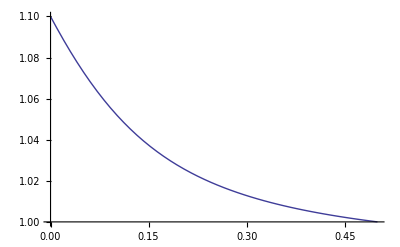

```mathematica
Plot[1/2 (2-R+√(R^2+(1-2 α)^2-2 R (1-2 α)^2))/.α->0.6,{R,0,1/2}]
```

which happens when R≠1/2 and α≠1/2, imlpying that any drive at all, in favour of either a or A leads to neo-W invasion. 

WHY IS THIS HAPPENING? MY RAMBLINGS:

1.When the neo-W arises on an X then it is linked with A. It pairs with male gametes, which are either Ya or XA. There is only drive when it pairs with Ya, and is only favoured when this drive favours A. When the neo-W arises on a Y then it is linked with a. There is then only drive when it pairs with an XA, and is only favoured when this drive favours a. Thus things seem rather neutral by symmetry. However, the symmetry is broken when we realize that there is drive in non-mutant males, biasing their gametes towards the driving haplotype. Thus the neo-W pairs more often with the driving type. If it itself is already with the driving allele, then this is good and spreading should happen. But if it is with the non-driving allele it should suffer extra because it pairs more often with the driving allele. This should really hinder invasion. Unless of course it could recombine off onto the driving background, but the expression above gets smaller with increasing R.

2. What we need to think about is WA and Wa haplotypes vs XA haplotypes in females. The W haplotypes can pair with Ya or XA while the XA only pair with XA. The W pairs with Ya or XA with equal probability when there is no selection or drive. With drive in males (or haploid selection in males) in favour of a then W haplotypes pair more often with Ya and with drive in males in favour of A, W haplotypes pair more often with A. Meanwhile the XA haplotypes that remain in females always pair with another XA and thus do not experience drive.

3. XA haplotypes end up in males sometimes, where they experience drive since they pair with Ya. Otherwise they are in homozygous females and hence experience no drive. W haplotypes never end up in males, but they also experience drive when arising on a Ya and pairing with an XA or arising on an XA and pairing with a Ya. They are more likely to pair with the driving allele...

4. Maybe we don’t need to think about the drive in both sexes case because it is less common in nature, and too hard...

For the neo-Y we have

```mathematica
Collect[Simplify[Solve[0==charpolyα0/.tryKozi,λ]/.Subscript[wDip, yM_,yP_,female]->1/.Subscript[wHap, y_,sex_]->1,{0≤R≤1/2,0≤α≤1}],α][[1]]//Factor
```

{λ→2 (-1+R) (-1+α)}

which implies that a neo-Y invades when

```mathematica
Reduce[1<2 (-1+R) (-1+α)&&0≤R≤1/2&&0≤α≤1,α,Reals]
```

0≤R<1/2&&0≤α<(-1+2 R)/(-2+2 R)

which can be written

```mathematica
α<(1/2- R)/(1- R);
```

and, as a function of R, looks like

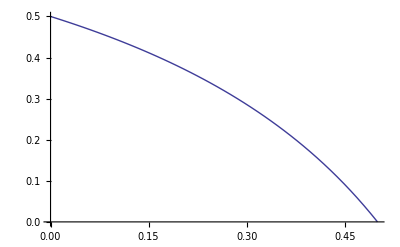

```mathematica
Plot[(1/2- R)/(1- R),{R,0,1/2}]
```

When a neo-Y arises it is linked with an A or an a, depending on whether is arose on an X (A) or a Y (a). If it arose on an X and is therefore linked with A, then it never experiences drive because it is always pairing with eggs, which also have allele A. But if it arises on a Y then it is linked with an a and always experiences drive and can be brought along by drive for a. If it gets lost from a by recombination then the drive in favour of a needs to be stronger to make up for this.

# D. Meiotic drive at viability locus (only in males)

## Life-cycle

Haploid selection

```mathematica
Subscript[wbarHap, sex_]:=Subscript[wbarHap, sex]=ParallelSum[Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex],{x,{X,Y}},{y,{A,a}},{z,{M,m}}];
Subscript[fHapSel, x_,y_,z_,sex_]:=Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex]/Subscript[wbarHap, sex]
```

Random mating

```mathematica
Subscript[fDip, xM_,yM_,zM_,xP_,yP_,zP_]:=Subscript[fDip, xM,yM,zM,xP,yP,zP]=Subscript[fHapSel, xM,yM,zM,female] Subscript[fHapSel, xP,yP,zP,male]
```

Sex determination

```mathematica
Subscript[fDipSex, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]=Subscript[fDip, xM,yM,zM,xP,yP,zP] Subscript[psex, zM,xP,zP,sex]
```

where a diploid must become male or female

```mathematica
sumsex=Subscript[psex, zM_,xP_,zP_,male]->1-Subscript[psex, zM,xP,zP,female];
```

We assume the invasion of a dominant modifier into an XY system

```mathematica
invXY={
Subscript[psex, M,Y,M,female]->0,(*always male if ESD wildtype and have Y*)
Subscript[psex, M,X,M,female]->1,(*always female ESD wildtype and have X from father*)
Subscript[psex, m,xP_,zP_,female]->k,(*female with probability k if mutation at the ESD*)
Subscript[psex, zM_,xP_,m,female]->k
};
```

Diploid selection

```mathematica
Subscript[wbarDip, sex_]:=Subscript[wbarDip, sex]=ParallelSum[Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}];
Subscript[fDipSel, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex]=Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]/Subscript[wbarDip, sex]
```

Meiosis

```mathematica
Subscript[fHapNext, x_,y_,z_,sex_]:=Subscript[fHapNext, x,y,z,sex]=ParallelSum[Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex] Subscript[pseg, xM,yM,zM,xP,yP,zP,sex,x,y,z],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}]
```

Segregation rules with male-specific meiotic drive (males who are heterozygous at the viablilty locus produce α% A haplotypes and 1-α% a haplotypes before selection)

```mathematica
pseg0={
(*triple homozygote*)
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z1_,sex_,x1_,y1_,z1_]->1
};
pseg1={
(*single heterozygotes*)
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x2_,y1_,z1_]->1/2,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,male,x1_,A,z1_]->α ,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,male,x1_,a,z1_]->(1-α),
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,male,x1_,A,z1_]->α ,
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,male,x1_,a,z1_]->(1-α),
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z1_,female,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z1_,female,x1_,y2_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z2_]->1/2
};
pseg2={
(*double heterozygotes*)
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x1_,A,z1_]->α(1-r),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x2_,a,z1_]->(1-α)(1-r),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x2_,A,z1_]->α r,
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x1_,a,z1_]->(1-α)r,
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,A,z1_]->α(1-R),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,a,z2_]->(1-α)(1-R),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,A,z2_]->α R,
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,a,z1_]->(1-α) R,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x1_,A,z1_]->α r,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x2_,a,z1_]->(1-α)r,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x2_,A,z1_]->α (1-r),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x1_,a,z1_]->(1-α)(1-r),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,A,z1_]->α R,
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,a,z2_]->(1-α)R,
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,A,z2_]->α (1-R),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,a,z1_]->(1-α) (1-R),
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,female,x1_,y1_,z1_]->(1-r)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,female,x2_,y2_,z1_]->(1-r)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,female,x2_,y1_,z1_]->r/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,female,x1_,y2_,z1_]->r/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,female,x1_,y1_,z1_]->(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,female,x1_,y2_,z2_]->(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,female,x1_,y2_,z1_]->R/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,female,x1_,y1_,z2_]->R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z1_]->((1-r)(1-R)+r R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z2_]->((1-r)(1-R)+r R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z1_]->(r(1-R)+(1-r)R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z2_]->(r(1-R)+(1-r)R)/2
};
pseg3={
(*triple heterozygote*)
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,A,z1_]->α(1-r)(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,a,z2_]->(1-α)(1-r)(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,A,z1_]->α r(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,a,z2_]->(1-α)r(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,A,z2_]->α r R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,a,z1_]->(1-α) r R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,A,z2_]->α(1-r)R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,a,z1_]->(1-α)(1-r)R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,A,z1_]->α r R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,a,z2_]->(1-α)r R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,A,z1_]->α (1-r)R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,a,z2_]->(1-α)(1-r)R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,A,z2_]->α (1-r)(1- R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,a,z1_]->(1-α) (1-r)(1- R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,A,z2_]->α r(1-R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,a,z1_]->(1-α)r (1-R),
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,female,x1_,y1_,z1_]->(1-r)(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,female,x2_,y2_,z2_]->(1-r)(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,female,x2_,y1_,z1_]->r(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,female,x1_,y2_,z2_]->r(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,female,x1_,y2_,z1_]->r R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,female,x2_,y1_,z2_]->r R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,female,x1_,y1_,z2_]->(1-r)R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,female,x2_,y2_,z1_]->(1-r)R/2
};
pseg4=Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x_,y_,z_]->0;
```

```mathematica
(*ParallelSum[Subscript[fHapNext, x,y,z,sex]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4,{x,{X,Y}},{y,{A,a}},{z,{M,m}},{sex,{male,female}}]//Factor*)
```

## Resident equilibrium (weak selection)

We begin with no mutations at the modifer locus

```mathematica
subequil={
Subscript[fHap, X,A,M,female]->pXf,
Subscript[fHap, X,a,M,female]->1-pXf,
Subscript[fHap, X,A,M,male]->pXm *(1-freqYm),
Subscript[fHap, X,a,M,male]->(1-pXm)(1-freqYm),
Subscript[fHap, Y,A,M,male]->pYm freqYm,
Subscript[fHap, Y,a,M,male]->(1-pYm)freqYm,
Subscript[fHap, x_,y_,m,sex_]->0,
Subscript[fHap, Y,y_,M,female]->0
};
```

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following three equations are zero (this takes a minute)

```mathematica
differenceEqs={
Subscript[fHapNext, X,A,M,female]-Subscript[fHap, X,A,M,female],
Subscript[fHapNext, X,A,M,male]-Subscript[fHap, X,A,M,male],
Subscript[fHapNext, Y,A,M,male]-Subscript[fHap, Y,A,M,male],
(Subscript[fHapNext, Y,A,M,male]+Subscript[fHapNext, Y,a,M,male])-(Subscript[fHap, Y,A,M,male]+Subscript[fHap, Y,a,M,male])
}/.subequil/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
```

To simplify the analysis we assume weak selection in both haploids and diploids and weak meiotic drive. In addition, we assume selection acts on the VS locus only

```mathematica
weaksel={
Subscript[wHap, A,sex_]->1+Subscript[sHap, sex] ϵ,
Subscript[wHap, a,sex_]->1,
Subscript[wDip, A,A,sex_]->1+ Subscript[sDip, sex] ϵ,
Subscript[wDip, A,a,sex_]->1+Subscript[h, sex] Subscript[sDip, sex] ϵ,
Subscript[wDip, a,A,sex_]->1+Subscript[h, sex] Subscript[sDip, sex] ϵ,
Subscript[wDip, a,a,sex_]->1,
α->1/2+α1 ϵ
};
```

We can write the frequencies as Taylor series

```mathematica
frequenciessub={
pXf->pXf0+pXf1 ϵ,
pXm->pXm0+pXm1 ϵ,
pYm->pYm0+pYm1 ϵ,
freqYm->freqYm0+freqYm1 ϵ+freqYm2 ϵ^2
};
```

Without selection the recursions for the change in the frequencies are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weaksel/.frequenciessub,{ϵ,0,0}]]//Factor
```

{1/2 (-pXf0+pXm0),1/2 (pXf0-2 pXm0+2 freqYm0 pXm0-pXf0 r+pYm0 r),1/2 (pYm0-2 freqYm0 pYm0+pXf0 r-pYm0 r),1/2 (1-2 freqYm0)}

And at equilibrium we have

```mathematica
sol0=Solve[differenceEqs0==0,{pYm0,pXm0,freqYm0}]//Flatten
```

{pYm0→pXf0,pXm0→pXf0,freqYm0→1/2}

So, with no selection or drive, the equilibrium frequency of A in each gamete/pollen type is equal (and we call this pA).

Now, looking at only the first order selection terms, the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs1=Collect[Normal[Series[differenceEqs/.weaksel/.frequenciessub/.sol0,{ϵ,0,1}]],ϵ,Factor]/.pXf0->pA//Flatten
```

{1/2 ϵ (-pXf1+pXm1+2 pA^2 sDip_female-2 pA^3 sDip_female+2 pA h_female sDip_female-6 pA^2 h_female sDip_female+4 pA^3 h_female sDip_female+pA sHap_female-pA^2 sHap_female+pA sHap_male-pA^2 sHap_male),1/2 ϵ (2 freqYm1 pA+pXf1-pXm1-pXf1 r+pYm1 r+2 pA α1-2 pA^2 α1+pA^2 sDip_male-pA^3 sDip_male+pA h_male sDip_male-3 pA^2 h_male sDip_male+2 pA^3 h_male sDip_male+pA sHap_female-pA^2 sHap_female-pA r sHap_female+pA^2 r sHap_female+pA r sHap_male-pA^2 r sHap_male),1/2 ϵ (-2 freqYm1 pA+pXf1 r-pYm1 r+2 pA α1-2 pA^2 α1+pA^2 sDip_male-pA^3 sDip_male+pA h_male sDip_male-3 pA^2 h_male sDip_male+2 pA^3 h_male sDip_male+pA r sHap_female-pA^2 r sHap_female+pA sHap_male-pA^2 sHap_male-pA r sHap_male+pA^2 r sHap_male),-freqYm1 ϵ}

And from these three equations we can solve for the two of the first order differences and the mean frequency of A

```mathematica
realsol=Solve[differenceEqs1==0/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{dpAXmXf,dpAYmXf,pA,freqYm1}]//Factor
```

{{dpAXmXf→0,dpAYmXf→0,pA→0,freqYm1→0},{dpAXmXf→0,dpAYmXf→0,pA→1,freqYm1→0},{dpAXmXf→((-2 α1-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male) (2 α1+h_female sDip_female+h_male sDip_male+sHap_female+sHap_male) (-4 α1 sDip_female+8 α1 h_female sDip_female+2 h_female sDip_female sDip_male-2 h_male sDip_female sDip_male-sDip_female sHap_female+2 h_female sDip_female sHap_female+sDip_male sHap_female-2 h_male sDip_male sHap_female-sDip_female sHap_male+2 h_female sDip_female sHap_male+sDip_male sHap_male-2 h_male sDip_male sHap_male))/(-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)^3,dpAYmXf→((-2 α1-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male) (2 α1+h_female sDip_female+h_male sDip_male+sHap_female+sHap_male) (-2 α1 sDip_female+4 α1 h_female sDip_female+h_female sDip_female sDip_male-h_male sDip_female sDip_male-r sDip_female sHap_female+2 r h_female sDip_female sHap_female+sDip_male sHap_female-r sDip_male sHap_female-2 h_male sDip_male sHap_female+2 r h_male sDip_male sHap_female-sDip_female sHap_male+r sDip_female sHap_male+2 h_female sDip_female sHap_male-2 r h_female sDip_female sHap_male+r sDip_male sHap_male-2 r h_male sDip_male sHap_male))/(r (-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)^3),pA→(2 α1+h_female sDip_female+h_male sDip_male+sHap_female+sHap_male)/(-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male),freqYm1→0}}

van Doorn and Kirkpatrick 2007 (SOM, page 6) give

```mathematica
vDK07=(Subscript[h, female] Subscript[sDip, female]+Subscript[h, male] Subscript[sDip, male])/((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male]);
```

And when there is no haploid selection or drive our result reduces to theirs

```mathematica
(pA/.realsol[[3]]/.Subscript[sHap, i_]->0/.α1->0)/vDK07//FullSimplify
```

1

## Resident stability (weak selection) [do not need to re-run if unchanged]

Here we use linear stability analysis to examine when the resident equilibrium (i.e., no mutants) derived above is stable.

The Jacobian for the residents is (this takes a couple minutes)

```mathematica
eqs=Join[Table[Subscript[fHapNext, X,y,M,female],{y,{A,a}}],Table[Subscript[fHapNext, x,y,M,male],{x,{X,Y}},{y,{A,a}}]//Flatten]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
matIntFull=Transpose[{
D[eqs,Subscript[fHap, X,A,M,female]],
D[eqs,Subscript[fHap, X,a,M,female]],
D[eqs,Subscript[fHap, X,A,M,male]],
D[eqs,Subscript[fHap, X,a,M,male]],
D[eqs,Subscript[fHap, Y,A,M,male]],
D[eqs,Subscript[fHap, Y,a,M,male]]
}]/.subequil//Factor;
```

From this we can derive the characteristic polynomial

```mathematica
charpolyIntFull=Det[matIntFull-IdentityMatrix[6]*λ];
```

Instead of examining when the non-trivial equilibrium (A not fixed or lost) is stable we will look for when the trivial equilibria (loss or fixation of A) are unstable.

When A is fixed the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt1=charpolyIntFull/.pXm->1/.pXf->1/.pYm->1;
Normal[Series[charpolyInt1/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Factor//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

and λ=1 is the leading eigenvalue.

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt1/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1fix=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (-2 α1-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male)}

And so the fixation of A is unstable when this expression is positive.

When A is lost the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt0=charpolyIntFull/.pXm->0/.pXf->0/.pYm->0;
Normal[Series[charpolyInt0/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt0/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1loss=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (2 α1+h_female sDip_female+h_male sDip_male+sHap_female+sHap_male)}

And so the loss of A is unstable when this expression is positive.

Combining the two results, the protected polymorphism (non-trivial equilibrium) requires that

```mathematica
stabconds={(δλ1/.δλ1fix)<0,(δλ1/.δλ1loss)<0};
```

Note that without haploid selection or drive (i.e., van Doorn and Kirkpatrick 2007), if selection favours the same allele in both sexes there is no stable polymorphism at the A locus

```mathematica
Reduce[(stabconds[[1]]/.Subscript[sHap, i_]->0/.α1->0)&&(stabconds[[2]]/.Subscript[sHap, i_]->0/.α1->0)&&0<Subscript[h, female]<1&&0<Subscript[h, male]<1&&0<Subscript[sDip, male]&&0<Subscript[sDip, female],Reals]
```

False

```mathematica
Reduce[(stabconds[[1]]/.Subscript[sHap, i_]->0/.α1->0)&&(stabconds[[2]]/.Subscript[sHap, i_]->0/.α1->0)&&0<Subscript[h, female]<1&&0<Subscript[h, male]<1&&Subscript[sDip, male]<0&&Subscript[sDip, female]<0,Reals]
```

False

However, with drive we no longer need sexually antagonistic selection for a stable polymorphism at the A locus, e.g., if drive in males opposes selection in diploids we can have a polymorphism when

```mathematica
Reduce[(stabconds[[1]]/.Subscript[sHap, i_]->0)&&(stabconds[[2]]/.Subscript[sHap, i_]->0)&&0<Subscript[h, female]<1&&0<Subscript[h, male]<1&&0<Subscript[sDip, male]&&0<Subscript[sDip, female]&&α1<0,Reals]
```

sDip_female>0&&((0<sDip_male<sDip_female&&((0<h_female≤(sDip_female-sDip_male)/(2 sDip_female)&&0<h_male<1&&1/2 (-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male)<α1<1/2 (-h_female sDip_female-h_male sDip_male))||((sDip_female-sDip_male)/(2 sDip_female)<h_female<(sDip_female+sDip_male)/(2 sDip_female)&&0<h_male<(sDip_female-2 h_female sDip_female+sDip_male)/(2 sDip_male)&&1/2 (-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male)<α1<1/2 (-h_female sDip_female-h_male sDip_male))))||(sDip_male≥sDip_female&&0<h_female<1&&0<h_male<(sDip_female-2 h_female sDip_female+sDip_male)/(2 sDip_male)&&1/2 (-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male)<α1<1/2 (-h_female sDip_female-h_male sDip_male)))

Assuming equal dominance coefficients in the sexes greatly reduces these conditions and we see that we need stronger drive in males than the sum of selection in diploids and a sufficiently small dominance coefficient

```mathematica
Reduce[(stabconds[[1]]/.Subscript[h, i_]->h/.Subscript[sHap, i_]->0)&&(stabconds[[2]]/.Subscript[h, i_]->h/.Subscript[sHap, i_]->0)0<h<1&&0<Subscript[sDip, male]&&0<Subscript[sDip, female]&&Subscript[sHap, female]==0&&Subscript[sHap, male]<0&&α1<0,α1,Reals]
```

sHap_female==0&&sHap_male<0&&sDip_female>0&&sDip_male>0&&0<h<1&&1/2 (-sDip_female+h sDip_female-sDip_male+h sDip_male)<α1<0

## Sex chromosome turnover (weak selection) [slow, ~15 minutes]

Here we are interested in the ability of a rare mutation at the modifier locus to invade the non-mutant resident population at equilibrium.

The Jacobian for the mutants is

```mathematica
eqsmut=ParallelTable[Subscript[fHapNext, x,y,m,sex],{sex,{male,female}},{y,{A,a}},{x,{X,Y}}]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4//Flatten;
matExtFull=Transpose[Flatten[ParallelTable[D[eqsmut,Subscript[fHap, x,y,m,sex]],{sex,{male,female}},{y,{A,a}},{x,{X,Y}}],2]]/.subequil//Factor;
```

Giving characteristic polynomial

```mathematica
charpolyExt=Det[matExtFull-IdentityMatrix[8]*λ];
```

Solving for the eigenvalues with no selection or drive gives

```mathematica
Normal[Series[charpolyExt/.weaksel/.freqYm->1/2+freqYm1 ϵ,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→0,λ→1,λ→1-R,λ→(-1+r) (-1+R),λ→1-r-R+2 r R}

On this order the leading eigenvalue is λ=1.

On the first order the eiganvalue is

```mathematica
Normal[Series[charpolyExt/.weaksel/.λ->1+δλ*ϵ/.frequenciessub/.sol0/.pXf0->pA,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ];
Collect[(δλ/.%)/((1-pA) pA /VA),α1,Simplify]
```

{0}

and on second order we have

```mathematica
Normal[Series[charpolyExt/.weaksel/.λ->1+δλ2*ϵ^2/.frequenciessub/.freqYm1->0/.sol0/.pXf0->pA/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2];
lambda2diffs=Collect[δλ2/.%,{dpAXmXf,dpAYmXf},Simplify]
```

{-1/2 dpAXmXf k (2 (-1+k) (-pA+(-1+2 pA) h_female) sDip_female-2 (-1+k) (-pA+(-1+2 pA) h_male) sDip_male+k (-sHap_female+sHap_male))+dpAYmXf (k^2 (pA+(1-2 pA) h_female) sDip_female+1/2 (2 (-1+k)^2 (-pA+(-1+2 pA) h_male) sDip_male+k^2 sHap_female-2 sHap_male+4 k sHap_male-k^2 sHap_male))-1/R(-1+pA) pA (4 α1^2-8 k α1^2+4 k^2 α1^2-8 R α1^2+16 k R α1^2-8 k^2 R α1^2+k^2 (pA+(1-2 pA) h_female)^2 sDip_female^2+(-1+k)^2 (pA+(1-2 pA) h_male)^2 sDip_male^2+4 k α1 sHap_female-4 k^2 α1 sHap_female-6 k R α1 sHap_female+6 k^2 R α1 sHap_female+k^2 sHap_female^2+k R sHap_female^2-2 k^2 R sHap_female^2+4 α1 sHap_male-8 k α1 sHap_male+4 k^2 α1 sHap_male-4 R α1 sHap_male+10 k R α1 sHap_male-6 k^2 R α1 sHap_male+2 k sHap_female sHap_male-2 k^2 sHap_female sHap_male+R sHap_female sHap_male-4 k R sHap_female sHap_male+4 k^2 R sHap_female sHap_male+sHap_male^2-2 k sHap_male^2+k^2 sHap_male^2-R sHap_male^2+3 k R sHap_male^2-2 k^2 R sHap_male^2-k (-pA+(-1+2 pA) h_female) sDip_female (4 α1-4 k α1-4 R α1+4 k R α1+2 (-1+k) (-pA+(-1+2 pA) h_male) sDip_male+(2 k+2 R-3 k R) sHap_female+2 sHap_male-2 k sHap_male-2 R sHap_male+3 k R sHap_male)+(-1+k) (-pA+(-1+2 pA) h_male) sDip_male (4 (-1+k) (-1+R) α1+(k (2-3 R)+R) sHap_female+(2-2 k-R+3 k R) sHap_male))}

Then we can put in all the differences

```mathematica
tester=Collect[Normal[Series[lambda2diffs/.realsol[[3]],{ϵ,0,2}]],{dpAXmXf,dpAYmXf},Simplify]
```

{((2 α1-(-1+h_female) sDip_female-(-1+h_male) sDip_male+sHap_female+sHap_male) (2 α1+h_female sDip_female+h_male sDip_male+sHap_female+sHap_male) ((1-2 h_male) sDip_male sHap_female+sDip_female (-2 α1-h_male sDip_male-sHap_male+h_female (4 α1+sDip_male+2 sHap_male))) ((-1+2 h_male) sDip_male ((r (2+k^2 (8-10 R)+8 k (-1+R))+(-2+4 k-3 k^2) R) sHap_female+(-1+2 r) R (4 (-1+k)^2 α1+k^2 sHap_male))+sDip_female (4 r α1-16 k r α1+16 k^2 r α1-4 k^2 R α1-8 r R α1+32 k r R α1-24 k^2 r R α1+2 (r (1+4 k (-1+R)-4 k^2 (-1+R))+(-1+2 k-2 k^2) R) h_male sDip_male-k^2 R sHap_female+2 k^2 r R sHap_female+2 r sHap_male-8 k r sHap_male+8 k^2 r sHap_male-2 R sHap_male+4 k R sHap_male-3 k^2 R sHap_male+8 k r R sHap_male-10 k^2 r R sHap_male+2 h_female (-4 r α1+16 k r α1-16 k^2 r α1+4 k^2 R α1+8 r R α1-32 k r R α1+24 k^2 r R α1+(r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) sDip_male+k^2 (1-2 r) R sHap_female-2 r sHap_male+8 k r sHap_male-8 k^2 r sHap_male+2 R sHap_male-4 k R sHap_male+3 k^2 R sHap_male-8 k r R sHap_male+10 k^2 r R sHap_male))))/(2 r R ((1-2 h_female) sDip_female+(1-2 h_male) sDip_male)^4)}

Print to avoid re-running all the above:

```mathematica
tester={((2 α1-(-1+Subscript[h, female]) Subscript[sDip, female]-(-1+Subscript[h, male]) Subscript[sDip, male]+Subscript[sHap, female]+Subscript[sHap, male]) (2 α1+Subscript[h, female] Subscript[sDip, female]+Subscript[h, male] Subscript[sDip, male]+Subscript[sHap, female]+Subscript[sHap, male]) ((1-2 Subscript[h, male]) Subscript[sDip, male] Subscript[sHap, female]+Subscript[sDip, female] (-2 α1-Subscript[h, male] Subscript[sDip, male]-Subscript[sHap, male]+Subscript[h, female] (4 α1+Subscript[sDip, male]+2 Subscript[sHap, male]))) ((-1+2 Subscript[h, male]) Subscript[sDip, male] ((r (2+k^2 (8-10 R)+8 k (-1+R))+(-2+4 k-3 k^2) R) Subscript[sHap, female]+(-1+2 r) R (4 (-1+k)^2 α1+k^2 Subscript[sHap, male]))+Subscript[sDip, female] (4 r α1-16 k r α1+16 k^2 r α1-4 k^2 R α1-8 r R α1+32 k r R α1-24 k^2 r R α1+2 (r (1+4 k (-1+R)-4 k^2 (-1+R))+(-1+2 k-2 k^2) R) Subscript[h, male] Subscript[sDip, male]-k^2 R Subscript[sHap, female]+2 k^2 r R Subscript[sHap, female]+2 r Subscript[sHap, male]-8 k r Subscript[sHap, male]+8 k^2 r Subscript[sHap, male]-2 R Subscript[sHap, male]+4 k R Subscript[sHap, male]-3 k^2 R Subscript[sHap, male]+8 k r R Subscript[sHap, male]-10 k^2 r R Subscript[sHap, male]+2 Subscript[h, female] (-4 r α1+16 k r α1-16 k^2 r α1+4 k^2 R α1+8 r R α1-32 k r R α1+24 k^2 r R α1+(r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) Subscript[sDip, male]+k^2 (1-2 r) R Subscript[sHap, female]-2 r Subscript[sHap, male]+8 k r Subscript[sHap, male]-8 k^2 r Subscript[sHap, male]+2 R Subscript[sHap, male]-4 k R Subscript[sHap, male]+3 k^2 R Subscript[sHap, male]-8 k r R Subscript[sHap, male]+10 k^2 r R Subscript[sHap, male]))))/(2 r R ((1-2 Subscript[h, female]) Subscript[sDip, female]+(1-2 Subscript[h, male]) Subscript[sDip, male])^4)};
```

1) Dominant masculinizer (neo-Y)

a) invading an XY system

```mathematica
selMasculinizerXY=Collect[tester/(pA(1-pA))*VA/.realsol[[3]]/.Subscript[h, sex_]->h/.k->0/.Subscript[sHap, sex_]->0,{α1},FullSimplify]//Factor
```

{-(4 VA α1^2 sDip_female (-r sDip_female+2 r R sDip_female-R sDip_male+2 r R sDip_male))/(r R (sDip_female+sDip_male)^2)}

b) invading a ZW system

```mathematica
Collect[tester/(pA(1-pA))*VA/.realsol[[3]]/.Subscript[h, sex_]->h/.k->0/.Subscript[sHap, sex_]->0,{α1},FullSimplify]/.female->temp/.male->female/.temp->male/.Subscript[sHap, female]->0;
selMasculinizerZW=%//Factor
```

{-(4 VA α1^2 sDip_male (-R sDip_female+2 r R sDip_female-r sDip_male+2 r R sDip_male))/(r R (sDip_female+sDip_male)^2)}

these are somehow just the same as the case where α1 was order ϵ and k=0

2) Dominant feminizer (neo-W)

a) invading an XY system

```mathematica
selFeminizerXY=Collect[tester/(pA(1-pA))*VA/.realsol[[3]]/.Subscript[h, sex_]->h/.k->1/.Subscript[sHap, sex_]->0,{α1},FullSimplify]//Factor
```

{(4 (r-R) VA α1^2 sDip_female^2)/(r R (sDip_female+sDip_male)^2)}

b) invading a ZW system

```mathematica
Collect[tester/(pA(1-pA))*VA/.realsol[[3]]/.Subscript[h, sex_]->h/.k->1/.Subscript[sHap, sex_]->0,{α1},FullSimplify]/.female->temp/.male->female/.temp->male/.Subscript[sHap, female]->0;
selFeminizerZW=%//Factor
```

{(4 (r-R) VA α1^2 sDip_male^2)/(r R (sDip_female+sDip_male)^2)}

3) Perfect ESD (half females, half males)

a) invading an XY system

```mathematica
selESDsimpXY=Collect[tester/(pA(1-pA))*VA/.realsol[[3]]/.Subscript[h, sex_]->h/.k->1/2/.Subscript[sHap, sex_]->0,{α1},Simplify]//Factor
```

{((-1+2 r) VA α1^2 sDip_female (sDip_female-sDip_male))/(r (sDip_female+sDip_male)^2)}

b) invading a ZW system

```mathematica
Collect[tester/(pA(1-pA))*VA/.realsol[[3]]/.Subscript[h, sex_]->h/.k->1/2/.Subscript[sHap, sex_]->0,{α1},Simplify]/.female->temp/.male->female/.temp->male/.Subscript[sHap, female]->0;
selESDsimpZW=%//Factor
```

{-((-1+2 r) VA α1^2 (sDip_female-sDip_male) sDip_male)/(r (sDip_female+sDip_male)^2)}

Now the common “selection” term during XY invasion is

```mathematica
StermXY=(α1^2  Subscript[sDip, female])/(r R(Subscript[sDip, female]+Subscript[sDip, male])^2);
```

making the conditions

```mathematica
Collect[selMasculinizerXY/(StermXY/SA),{SA,VA,Subscript[sDip, female],Subscript[sDip, male]},Factor]
```

{SA VA (-4 r (-1+2 R) sDip_female-4 (-1+2 r) R sDip_male)}

```mathematica
selFeminizerXY/(StermXY/SA)
```

{4 (r-R) SA VA sDip_female}

```mathematica
selESDsimpXY/(StermXY/SA)
```

{(-1+2 r) R SA VA (sDip_female-sDip_male)}

During ZW invasions we have “selection” term

```mathematica
StermZW=(α1^2  Subscript[sDip, male])/(r R(Subscript[sDip, female]+Subscript[sDip, male])^2);
```

making the conditions

```mathematica
Collect[selMasculinizerZW/(StermZW/SA),{SA,VA,Subscript[sDip, female],Subscript[sDip, male]},Factor]
```

{SA VA (-4 (-1+2 r) R sDip_female-4 r (-1+2 R) sDip_male)}

```mathematica
selFeminizerZW/(StermZW/SA)
```

{4 (r-R) SA VA sDip_male}

```mathematica
selESDsimpZW/(StermZW/SA)
```

{-(-1+2 r) R SA VA (sDip_female-sDip_male)}

## Sex chromosome turnover (selection not assumed to be weak)

### Characteristic polynomial

In this section we do not assume weak selection.

#### Mean fitness of residents

We first define the mean fitness of non-mutant females over the entire life-cycle

```mathematica
femaleMeanFit=
(1-pXf)Subscript[wHap, a,female] (1-pXm)(1-freqYm) Subscript[wHap, a,male] Subscript[wDip, a,a,female]+
pXf Subscript[wHap, A,female] (1-pXm)(1-freqYm) Subscript[wHap, a,male] Subscript[wDip, A,a,female]+
(1-pXf)Subscript[wHap, a,female] pXm(1-freqYm) Subscript[wHap, A,male] Subscript[wDip, a,A,female] +
pXf Subscript[wHap, A,female] pXm (1-freqYm)Subscript[wHap, A,male] Subscript[wDip, A,A,female];
```

and the mean fitness of non-mutant males over the entire life-cycle

```mathematica
maleMeanFit=
(1-pXf)Subscript[wHap, a,female] (1-pYm)freqYm  Subscript[wHap, a,male] Subscript[wDip, a,a,male]+
pXf Subscript[wHap, A,female] (1-pYm)freqYm  Subscript[wHap, a,male] Subscript[wDip, A,a,male]+
(1-pXf)Subscript[wHap, a,female] pYm freqYm  Subscript[wHap, A,male] Subscript[wDip, a,A,male] +
pXf Subscript[wHap, A,female] pYm freqYm  Subscript[wHap, A,male] Subscript[wDip, A,A,male];
```

#### neo-Y

When the mutation masculinizes, the characteristic polynomial is

```mathematica
charpolyk0=charpolyExt/.k->0//Factor;
```

The coefficients of our characteristic polynomial are

```mathematica
charpolyα0=Collect[charpolyk0[[4]],λ];
acoef0=Coefficient[charpolyα0,λ^2];
bcoef0=Coefficient[charpolyα0,λ];
ccoef0=charpolyα0-acoef0 λ^2-bcoef0 λ;
```

```mathematica
charpolyα0=Collect[charpolyk0[[3]],λ];
acoef0=Coefficient[charpolyα0,λ^2];
bcoef0=Coefficient[charpolyα0,λ];
ccoef0=charpolyα0-acoef0 λ^2-bcoef0 λ;
```

The a coefficient is

```mathematica
acoef0/(maleMeanFit/meanM)^2//Simplify
```

meanM^2

The b coefficient is

```mathematica
bcoef0/(maleMeanFit/meanM)//Simplify
```

meanM ((-1+pXf) wHap_(a,female) (wHap_(a,male) wDip_(a,a,male)-2 (-1+R) α wHap_(A,male) wDip_(a,A,male))-pXf wHap_(A,female) (2 (-1+R) (-1+α) wHap_(a,male) wDip_(A,a,male)+wHap_(A,male) wDip_(A,A,male)))

The c coefficient is

```mathematica
ccoef0//Simplify
```

wHap_(a,male) wHap_(A,male) (-2 (-1+pXf)^2 (-1+R) α wHap_(a,female)^2 wDip_(a,a,male) wDip_(a,A,male)+2 pXf^2 (-1+R) (-1+α) wHap_(A,female)^2 wDip_(A,a,male) wDip_(A,A,male)-(-1+pXf) pXf wHap_(a,female) wHap_(A,female) (4 (-1+2 R) (-1+α) α wDip_(a,A,male) wDip_(A,a,male)+wDip_(a,a,male) wDip_(A,A,male)))

#### neo-W

When the mutation feminizes the characteristic polynomial is

```mathematica
charpolyk1=charpolyExt/.k->1//Factor;
```

and the coefficients are

```mathematica
charpolyα1=Collect[charpolyk1[[5]],λ];
acoef1=Coefficient[charpolyα1,λ^2];
bcoef1=Coefficient[charpolyα1,λ];
ccoef1=charpolyα1-acoef1 λ^2-bcoef1 λ;
```

The a coefficient is

```mathematica
acoef1/(femaleMeanFit/meanF)^2//Simplify
```

4 meanF^2

the b coefficient is

```mathematica
bcoef1/(femaleMeanFit/meanF)/.pXm->2pAveM-pYm//Simplify
```

-2 meanF (wHap_(a,female) ((1+2 (-1+freqYm) pAveM+pYm-2 freqYm pYm) wHap_(a,male) wDip_(a,a,female)+(2 (-1+freqYm) pAveM+pYm-2 freqYm pYm) (-1+R) wHap_(A,male) wDip_(a,A,female))+wHap_(A,female) (-(1+2 (-1+freqYm) pAveM+pYm-2 freqYm pYm) (-1+R) wHap_(a,male) wDip_(A,a,female)-(2 (-1+freqYm) pAveM+pYm-2 freqYm pYm) wHap_(A,male) wDip_(A,A,female)))

where pAveM is the mean frequency of A in gametes from males,

and the c coefficient is

```mathematica
ccoef1/.pXm->2pAveM-pYm//Simplify
```

wHap_(a,female) wHap_(A,female) (-(1+2 (-1+freqYm) pAveM+pYm-2 freqYm pYm)^2 (-1+R) wHap_(a,male)^2 wDip_(a,a,female) wDip_(A,a,female)-(2 (-1+freqYm) pAveM+pYm-2 freqYm pYm)^2 (-1+R) wHap_(A,male)^2 wDip_(a,A,female) wDip_(A,A,female)+(4 (-1+freqYm)^2 pAveM^2+(-1+2 freqYm) pYm (-1+(-1+2 freqYm) pYm)-2 (-1+freqYm) pAveM (-1+(-2+4 freqYm) pYm)) wHap_(a,male) wHap_(A,male) ((-1+2 R) wDip_(a,A,female) wDip_(A,a,female)-wDip_(a,a,female) wDip_(A,A,female)))

### Turnover criteria

#### neo-Y

When there is no recombination at all the eigenvalues are

```mathematica
noreceigens0=(λ/.Solve[0==charpolyk0[[3]]/.r->0/.R->0,λ])*(maleMeanFit/meanM)//Simplify
```

{-(wHap_(A,male) (2 (-1+pXf) α wHap_(a,female) wDip_(a,A,male)-pXf wHap_(A,female) wDip_(A,A,male)))/meanM,-(wHap_(a,male) ((-1+pXf) wHap_(a,female) wDip_(a,a,male)+2 pXf (-1+α) wHap_(A,female) wDip_(A,a,male)))/meanM}

The growth rates of the haplotypes (where mA and ma haplotypes are lost due to recombination R in double heterozygotes) can be used to reduce the 2a+b<0 condition to

```mathematica
gAsub=Solve[gA==noreceigens0[[1]]-1/.Subscript[wDip, a,A,male]->(1-R) Subscript[wDip, a,A,male],Subscript[wDip, A,A,male]]//Simplify//Flatten;
gasub=Solve[ga==noreceigens0[[2]]-1/.Subscript[wDip, A,a,male]->(1-R) Subscript[wDip, A,a,male],Subscript[wDip, a,a,male]]//Simplify//Flatten;
(2acoef0/(maleMeanFit/meanM)^2+bcoef0/(maleMeanFit/meanM))<0/.gasub/.gAsub//Simplify;
Simplify[%/.Subscript[wDip, a,A,male]->Subscript[wDip, A,a,male],{meanM>0}];
%/.gA->2gmean-ga//Simplify
```

gmean>0

And when we ignore the break up due to recombination then the growth rates are

```mathematica
gAssub=Solve[gAs==noreceigens0[[1]]-1,Subscript[wDip, A,A,male]]//Simplify//Flatten;
gassub=Solve[gas==noreceigens0[[2]]-1,Subscript[wDip, a,a,male]]//Simplify//Flatten;
```

and our final condition a+b+c<0 is

```mathematica
Collect[(acoef0/(maleMeanFit/meanM)^2+bcoef0/(maleMeanFit/meanM)+ccoef0)<0/.gassub/.gAssub/.Subscript[wDip, a,A,male]->Subscript[wDip, A,a,male]//Simplify,{meanM,Subscript[wDip, A,a,male]},Simplify]
```

gas gAs meanM^2+2 meanM R (gAs pXf (-1+α) wHap_(a,male) wHap_(A,female)+gas (-1+pXf) α wHap_(a,female) wHap_(A,male)) wDip_(A,a,male)<0

which can be rearranged into

```mathematica
gas gAs meanM^2+2 meanM R (gAs pXf (-1+α) Subscript[wHap, a,male] Subscript[wHap, A,female]+gas (-1+pXf) α Subscript[wHap, a,female] Subscript[wHap, A,male]) Subscript[wDip, A,a,male]<0;
```

If both ga>0 and gA>0 then 2a+b>0 and the neo-Y invades. If both gas<0 and gAs<0 then a+b+c<0 is never true and the neo-Y will not invade. So the interesting part is when one gs is positive and one negative. If we assume, without loss of generality, that gAs>0 and gas<0, the product gas gAs is negative. Dividing through and flipping the inequality:

```mathematica
2 R ((pXf (1-α) Subscript[wHap, a,male] Subscript[wHap, A,female])/gas+((1-pXf) α Subscript[wHap, a,female] Subscript[wHap, A,male])/gAs) Subscript[wDip, A,a,male]<meanM;
```

If α=1/2 we recover the no drive case

```mathematica
2 R ((pXf (1-α) Subscript[wHap, a,male] Subscript[wHap, A,female])/gas+((1-pXf) α Subscript[wHap, a,female] Subscript[wHap, A,male])/gAs) Subscript[wDip, A,a,male]<meanM/.α->1/2
```

2 R ((pXf wHap_(a,male) wHap_(A,female))/(2 gas)+((1-pXf) wHap_(a,female) wHap_(A,male))/(2 gAs)) wDip_(A,a,male)<meanM

If, instead, there is no haploid selection then we have

```mathematica
2 R ((pXf (1-α) Subscript[wHap, a,male] Subscript[wHap, A,female])/gas+((1-pXf) α Subscript[wHap, a,female] Subscript[wHap, A,male])/gAs) Subscript[wDip, A,a,male]<meanM/.Subscript[wHap, i_,j_]->1
```

2 R ((pXf (1-α))/gas+((1-pXf) α)/gAs) wDip_(A,a,male)<meanM

With no haploid selection in females, the haploid selection case reduces to the drive case when we replace wHap_(a,male) with 1-α and wHap_(A,male) with α.

#### neo-W

When there is no recombination between the VS and modifier locus we have a perfect square and eigenvalues

```mathematica
noreceigens1=(λ/.Solve[0==charpolyk1[[5]]/.R->0,λ])*(femaleMeanFit/meanF)/.pXm->2pAveM-pYm//Simplify
```

{(wHap_(a,female) ((1+2 (-1+freqYm) pAveM+pYm-2 freqYm pYm) wHap_(a,male) wDip_(a,a,female)-(2 (-1+freqYm) pAveM+pYm-2 freqYm pYm) wHap_(A,male) wDip_(a,A,female)))/(2 meanF),(wHap_(A,female) ((1+2 (-1+freqYm) pAveM+pYm-2 freqYm pYm) wHap_(a,male) wDip_(A,a,female)-(2 (-1+freqYm) pAveM+pYm-2 freqYm pYm) wHap_(A,male) wDip_(A,A,female)))/(2 meanF)}

```mathematica
noreceigens1=(λ/.Solve[0==charpolyk1[[5]]/.R->0,λ])*(femaleMeanFit/meanF)//Simplify
```

{(wHap_(a,female) ((1+(-1+freqYm) pXm-freqYm pYm) wHap_(a,male) wDip_(a,a,female)+(pXm-freqYm pXm+freqYm pYm) wHap_(A,male) wDip_(a,A,female)))/(2 meanF),(wHap_(A,female) ((1+(-1+freqYm) pXm-freqYm pYm) wHap_(a,male) wDip_(A,a,female)+(pXm-freqYm pXm+freqYm pYm) wHap_(A,male) wDip_(A,A,female)))/(2 meanF)}

```mathematica
noreceigens1/.Subscript[wHap, y_,sex_]->1/.pXm->(pAveM-freqYm pYm)/(1-freqYm)//Simplify
```

{(-(-1+pAveM) wDip_(a,a,female)+pAveM wDip_(a,A,female))/(2 meanF),(-(-1+pAveM) wDip_(A,a,female)+pAveM wDip_(A,A,female))/(2 meanF)}

The first describes the invasion fitness of w-a haplotypes and the second the growth rate of w-A haplotypes (these haplotypes are never broken up because R=0, and they always appear in the homorphic sex and so r has no affect).

The growth rate of the haplotypes without recombination can be used to simplify our expressions. To make use of them we will first solve for unique elements in each and then use these substitutions later.

```mathematica
gasubR0=Solve[noreceigens1[[1]]-1==gaR0,Subscript[wDip, a,a,female]]//Flatten;
gAsubR0=Solve[noreceigens1[[2]]-1==gAR0,Subscript[wDip, A,A,female]]//Simplify//Flatten;
```

Our 2a+b<0 condition is then

```mathematica
Simplify[(2acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF))<0/.pXm->-pYm+2pAveM/.gAsubR0/.gasubR0,meanF>0]
```

((-1+freqYm) pXm-freqYm pYm) (1+(-1+freqYm) pXm-freqYm pYm) (-2 meanF (-2 (-1+freqYm)^2 pXm^2+2 (-1+freqYm) pAveM (1+(-1+freqYm) (2+gaR0) pXm-2 freqYm pYm-freqYm gaR0 pYm+gAR0 (1+(-1+freqYm) pXm-freqYm pYm))-(-1+freqYm) pXm (1+(-2-gAR0+2 freqYm gAR0) pYm+gaR0 (-1+(-1+2 freqYm) pYm))+pYm (1+gAR0+2 freqYm^2 (1+gaR0+gAR0) pYm-freqYm (1+gaR0+2 gAR0+2 pYm+gaR0 pYm+gAR0 pYm)))+((-1+freqYm) pXm-freqYm pYm) ((-1+freqYm) pXm (-1+(-1+2 freqYm) pYm R)-2 (-1+freqYm) pAveM (-1+(1+(-1+freqYm) pXm-freqYm pYm) R)-pYm (-1+R+2 freqYm^2 pYm R-freqYm (-1+(2+pYm) R))) wHap_(a,female) wHap_(A,male) wDip_(a,A,female)-(1+(-1+freqYm) pXm-freqYm pYm) (-2 (-1+freqYm) pAveM (1+(-1+freqYm) pXm R-freqYm pYm R)+(-1+freqYm) pXm (1+(-1-pYm+2 freqYm pYm) R)+pYm (-1-2 freqYm^2 pYm R+freqYm (1+R+pYm R))) wHap_(a,male) wHap_(A,female) wDip_(A,a,female))<0

and when the fitness of diploids does not depend from which parent the A and a alleles come from, and there is no competition among eggs, we have

```mathematica
%/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]/.Subscript[wHap, y_,female]->1//FullSimplify
```

R ((1+2 (-1+freqYm) pAveM+pYm-2 freqYm pYm) wHap_(a,male)-(2 (-1+freqYm) pAveM+pYm-2 freqYm pYm) wHap_(A,male)) wDip_(A,a,female)<2 (gaR0+gAR0) meanF

n.b., if you instead look at the growth rates of the haplotypes with recombination (where double heterozygotes are sometimes lost through recombination; we don’t have many triple heterozygotes in females when the neo-W is rare because all are XX) this condition becomes

```mathematica
gasub=Solve[ga==noreceigens1[[1]]-1/. Subscript[wDip, a,A,female]->(1-R) Subscript[wDip, a,A,female],Subscript[wDip, a,a,female]]//Simplify//Flatten;
gAsub=Solve[gA==noreceigens1[[2]]-1/. Subscript[wDip, A,a,female]->(1-R) Subscript[wDip, A,a,female],Subscript[wDip, A,A,female]]//Simplify//Flatten;
(2acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF))/meanF^2<0/.pXm->-pYm+2pAveM/.gAsub/.gasub//Simplify;
%/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]/.ga->-gA+2gmean//FullSimplify
```

gmean>0

which only requires that the mean haplotype growth rate is greater than 0.

Using the no recombination growth rate definitions, our final condition is

```mathematica
Collect[(acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF)+ccoef1)/meanF<0/.pXm->-pYm+2pAveM/.gasubR0/.gAsubR0/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]//Simplify,{meanF,R,Subscript[wDip, A,a,female]}]
```

2 gaR0 gAR0 meanF+gAR0 (2 (-1+freqYm) pAveM+pYm-2 freqYm pYm) R wHap_(a,female) wHap_(A,male) wDip_(A,a,female)<gaR0 (1+2 (-1+freqYm) pAveM+pYm-2 freqYm pYm) R wHap_(a,male) wHap_(A,female) wDip_(A,a,female)

-2 gaR0 gAR0 meanF+R (gaR0 (1+(-1+freqYm) pXm-freqYm pYm) wHap_(a,male) wHap_(A,female)+gAR0 (pXm-freqYm pXm+freqYm pYm) wHap_(a,female) wHap_(A,male)) wDip_(A,a,female)>0

```mathematica
Collect[(acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF)+ccoef1)/meanF<0/.gasubR0/.gAsubR0/.pXm->(pAveM-freqYm pYm)/(1-freqYm)/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]//Simplify,{meanF,R,Subscript[wDip, A,a,female]},Simplify]
```

4 gaR0 gAR0 meanF+2 gaR0 (-1+pAveM) R wHap_(a,male) wHap_(A,female) wDip_(A,a,female)<2 gAR0 pAveM R wHap_(a,female) wHap_(A,male) wDip_(A,a,female)

### Comparison to Kozielska et al 2010 AND OVER HERE

Kozielska et al 2010 found that feminizing mutations invade, apparently to equalize the sex ratio.

Kozielska et al 2010 (Heredity 104:100) found that, without diploid or haploid selection, the W invades if the Y is ‘driving’ and the resident equilibrium is A fixed on the X and lost on the Y

```mathematica
tryKozi={pXf->1,pXm->1,pYm->0};
Simplify[Solve[0==charpolyα1/.tryKozi,λ]/.Subscript[wDip, yM_,yP_,sex_]->1/.Subscript[wHap, y_,sex_]->1,{R>0,0≤α≤1}]
```

{{λ→1},{λ→1-R}}

We don’t find this here where the a is driving in males (so that the Y might also be said to be driving, since it is linked to the a allele and always pairs with an X that is linked with an A). In fact, there is no drive in charpolyα1 at all. Why not? We found that haploid selection in males could cause the neo-W to invade. And drive should be much like haploid selection (as shown above), so I am confused.

But drive in males can cause a neo-Y to invade

```mathematica
Simplify[Solve[0==charpolyα0/.tryKozi,λ]/.Subscript[wDip, yM_,yP_,sex_]->1/.Subscript[wHap, y_,sex_]->1,{R>0,0≤α≤1}]//Flatten
```

{λ→2 (-1+R) (-1+α),λ→1}

when

```mathematica
Reduce[1<(λ/.%)&&0≤R≤1/2,α]
```

0≤R≤1/2&&α<(-1+2 R)/(-2+2 R)

```mathematica
Plot[(-1+2 R)/(-2+2 R),{R,0,1/2}]
```

-Graphics-

So that with complete linkage between the neo-Y and the A locus (R=0) any drive in favour of the little a allele will allow a neo-Y to invade. As the linkage becomes weaker the strength of drive must increase to compensate for loss of the haplotype by recombination.  This is the same as the case with drive in both sexes.